Last modified:  20, May 36

# O(ϵ) m-mode (Teukolsky) Effective-Source Generator

Builds the first order effective source from a λ^4 puncture in m-modes for a circular orbit 
Key features:
- Newman Penrose formalism
- uses comoving coordinates and frame for a circular orbit in Kerr: \omega= m\Omega_0
- Imports m-mode decomposed (T^m)_ab(X,Y) 
- compute the Teukolsky effective source _s T^m(X,Y) 
- performs ell mode projection_s T^ml(X,Y)

Computes the m-mode effective source from the 4th order puncture 
 for a particle on a circular orbit using comoving coordinates X^μ= (T,X,Y,Z) centered on the particle 
 X_p^μ = (T,0,0,0).  These are related to BL (t,r,θ,ϕ) coordinates by 

 T=((α+ρ_0-2)t-M √ρ_0(α^2-2α+ρ_0)ϕ)/(𝒟 ρ_0)=((a √M+√r_0 (-2 M+r_0)) t 𝒟-√M (a^2+r_0^2-2 a √(M r_0)) 𝒟 ϕ)/(2 a √M+√r0 (-3 M+r0)),

X= (r-M ρ_0)/ℬ=(r-r0)/ℬ,

Y=-Mρ_0 Cos[θ]=-r_0 Cos[θ],

Z= z_c Sin[(ϕ-Ω_p t)/2]=z_c Sin[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]
where 
ρ_0=r_0/M, α=a/(√(M r_0))
and
z_c=2 √(M/r_0)ℬ/(Ω_p 𝒟), ℬ=√((α^2+ρ_0-2)/ρ_0,), 𝒟=√((2α+ρ_0-3)/ρ_0,), Ω_p=1/(√((M α +M ρ_0)ρ_0,))

Note that in the projection we define 
y := cosθ, which is different from y_paper = cos^2 θ
For a=0  the m-modes of the NP components are symmetric under Y->-Y and change imaginary part under m->-m

 (Adapted and truncated from  Patrick’s PunctureInCoordinates)

## Setup

## Globals

```mathematica
ClearAll["Global`*"]
```

```mathematica
HP = 64; (* high precision *)
GP = 16; (* global precision *)
WP = 32; (* working precision *)
MP = 15; (* machine double *)
N64[f_]:=N[f,HP]
N32[f_]:=N[f,WP]
N15[f_]:=N[f,MP]
aKerr = 33/100;
MKerr= 1;
massval = N64@MKerr;
spinval = N64@aKerr;
mModeval = 2;
ellMax=15;
```

2

#### Configurations (from Patrick)

##### Palettes and docked buttons

Below is the full docked buttons code. In the following sections, we explain each part.

Correcting alignment

This docked button will go through the notebook and correctly align all the text.

```mathematica
buttonalignment = With[{styles={"Section","Subsection","Subsubsection"}},
	ToBoxes@Button["align",Map[Set[CurrentValue[#,{CellMargins,1,1}],
CurrentValue[PreviousCell[#,CellStyle->styles],{CellMargins,1,1}]]&,Cells[CellStyle->"Text"]]]];
```

Correctly re-enable evaluation property

This part of the above code creates a docked button that easily allows to deactivate cell evaluation and re - enable it,
	while keeping the texts, outputs,etc default (not evaluable).  Specifically, “re-enable” in fact just sets properties back to default.

```mathematica
buttonevaluable = ToBoxes@Column[Button[StringForm["Evaluable -> ``",#], 
CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}];
```

The below code does the same thing, but it creates a palette instead. Kept it for archive purposes.

```mathematica
CreatePalette@Column[Button[StringForm["Evaluatable -> ``",#],
	CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}]
```

Full docked buttons

Implementation of each part as a docked cell. For adding new features, simply create new data as shown for the above two buttons, i.e. ToBoxes[stuff] and then put it inside the BoxData.
				The next lines shoul not be touched and their purpose is to make the toolbar expand/collapse upon clicking of the bottom panel.

```mathematica
fullDockedCellsWithCollapseToolbar=Cell[BoxData[{buttonalignment,buttonevaluable}], 
					CellFrameLabelMargins->0,CellFrameLabels->{{None,None},{ButtonBox["",
				ButtonFunction:>Function[With[{pc=ParentCell@EvaluationCell[]},SetOptions[pc,If[CurrentValue[pc,CellSize]===0,{CellSize->Inherited,CellElementSpacings->{},
				CellFrameMargins->Inherited},{CellSize->0,CellElementSpacings->{"CellMinHeight"->0},CellFrameMargins->0}]]]], ImageSize->{Scaled[2],15},Evaluator->Automatic],None}}];
				SetOptions[EvaluationNotebook[],DockedCells->fullDockedCellsWithCollapseToolbar]
				Clear[buttonalignment,buttonevaluable]
```

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions:>{"WindowClose":>Module[{dy,mn,yr},{dy,mn,yr}=
	   Map[(LinkWrite[First[$FrontEnd],FrontEnd`Value[#]];
     LinkRead[First[$FrontEnd]])&,{"Day","MonthName","Second"}];NotebookLocate["LastModified"];
	     NotebookWrite[InputNotebook[],Cell[TextData[{"Last modified:  ",dy,", ",mn," ",yr}],"Text",CellTags->"LastModified"]]]}]
```

## Preamble

```mathematica
<<xAct`xCoba`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$DefInfoQ=False;
$CVVerbose=False;
$PrePrint = ScreenDollarIndices;
$CovDFormat="Postfix";
```

```mathematica
SetOptions[ToCanonical,UseMetricOnVBundle->None]
```

{Verbose→False,UseMetricOnVBundle→None,Method→{ChangeCovD,ExpandChristoffel→False},MathLink:>$xpermQ,TimeVerbose→False}

```mathematica
SetOptions[Parallelize,Method->"FinestGrained"]
```

{DistributedContexts:>$Context,Method→FinestGrained,ProgressReporting:>$ProgressReporting}

```mathematica
SetOptions[ParallelMap,Method->"FinestGrained"]
```

{DistributedContexts:>$DistributedContexts,Method→FinestGrained,ProgressReporting:>$ProgressReporting}

```mathematica
org[expr_]:=ToCanonical[ContractMetric[expr,OverDerivatives->True]//CheckZeroDerivative,UseMetricOnVBundle->All]
```

## Manifolds, Coordinates, Metrics

```mathematica
DefManifold[M4,4,{α2,β2,γ2,μ2,ν2,ρ2,υ2,ι2,σ2,ζ2,ξ2,χ2}]
```

#### Constants

```mathematica
DefConstantSymbol[λ]
DefConstantSymbol[m] (* mode number *)
DefConstantSymbol[{a,M}] (* Kerr Mass *)
DefConstantSymbol[r0] (* constant particle radius *)
DefConstantSymbol[{ℬ,𝒟,zc,α,ρ0,Ω}] (* quantities eval'd at the particle *)
```

#### Coordinate Chart

```mathematica
DefChart[CM,M4,{0,1,2,3},{T[],X[],Y[],Z[]},ChartColor->Red] (* local coordinates centered  to the particle *)
```

```mathematica
DefChart[BL,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor->Blue] (* local coordinates centered on the Kerr BH *)
```

```mathematica
OnPart={X[]->0,Y[]->0,Z[]->0}; (* limit to the particle *)
```

```mathematica
(* aux  quantities in the coordinate transformation between X and x *)
myzc = 2(√M)/(√r0)ℬ/(Ω 𝒟)/.r0->ρ0 M//PowerExpand;
𝒟expr  =(√(2α+ρ0-3))/(√ρ0);
ℬexpr = (√(α^2+ρ0-2))/(√ρ0);
Ωexpr=1/(√ρ0 M(α+ρ0));
```

```mathematica
BDzcRules={zc->myzc,ℬ->ℬexpr,𝒟->𝒟expr,Ω->Ωexpr};
```

```mathematica
SchWLimit={α->0,a->0};
BDzcRules$SchWLimit=BDzcRules//.SchWLimit//Simplify;
```

```mathematica
ToVars={r0->M ρ0,a->α √M √r0};
```

```mathematica
$Assumptions={r0,M,a,α,Ω,ℬ,𝒟,zc,R[],X[],Y[],Z[]}∈Reals&&zc>0&&𝒟>0&&ℬ>0&&Ω>0&&ρ0>0&&M>0&&0<a<1&&0<α<1&&R[]>0&&-zc<=Z[]<=zc&&X[]!=0&&-M ρ0<=Y[]<=M ρ0 && X[] ∈ Reals && X ∈ Reals;
```

```mathematica
(* α and ρ0 are dimensionless *)
αρ0Toar0$Rule = {α -> a r0^(-1/2) M^(-1/2) ,ρ0 -> r0/M};
𝒳𝒴𝒵ToXYZ$Rule = {𝒳 ->( ℬ/r0) X[]+1 ,  𝒴 ->Y[]/r0 , 𝒵 -> (ℬ*ρ0^(5/2)*Sqrt[zc^2-Z[]^2])/zc}/.ToVars;
```

```mathematica
zc//.BDzcRules//.αρ0Toar0$Rule
```

(2 M √(-2+a^2/(M r0)+r0/M) (a/(√M √r0)+r0/M))/(√(-3+(2 a)/(√M √r0)+r0/M))

```mathematica
αρToℬ={-2+α^2+ρ0->ℬ^2 ρ0};
αρTo𝒟={(-3+2 α+ρ0)->𝒟^2 ρ0};
apToBD=Join[αρToℬ,αρTo𝒟,{(α+ρ0)->(zc 𝒟)/(2 M ℬ)}];
```

#### Metric functions

```mathematica
metric$InTXYZCoordinates = ({{-(𝒴^4 α^4+𝒳^4 (-1+𝒴^2) ρ0^2+𝒴^2 α^2 ρ0 (2 α+ρ0)-2 𝒳 (𝒴^2 α+ρ0)^2+𝒳^2 ρ0 (𝒴^4 α^2+ρ0 (2 α+ρ0)))/(ρ0 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0)), 0, 0, (ρ0 (-𝒳^4 (-1+𝒴^2) ρ0^2 (-2+α+ρ0)+2 𝒳 (𝒴^2 α+ρ0) (ρ0-α ρ0+𝒴^2 α (-2+α+ρ0))-𝒴^2 α^2 (ρ0 (-α+ρ0)+𝒴^2 α^2 (-2+α+ρ0))-𝒳^2 ρ0 (ρ0 (-α+ρ0)+𝒴^4 α^2 (-2+α+ρ0))))/(𝒵 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0))}, {0, ((-2+α^2+ρ0) (𝒴^2 α^2+𝒳^2 ρ0))/(ρ0 (α^2+𝒳 (-2+𝒳 ρ0))), 0, 0}, {0, 0, (𝒴^2 α^2+𝒳^2 ρ0)/(ρ0-𝒴^2 ρ0), 0}, {(ρ0 (-𝒳^4 (-1+𝒴^2) ρ0^2 (-2+α+ρ0)+2 𝒳 (𝒴^2 α+ρ0) (ρ0-α ρ0+𝒴^2 α (-2+α+ρ0))-𝒴^2 α^2 (ρ0 (-α+ρ0)+𝒴^2 α^2 (-2+α+ρ0))-𝒳^2 ρ0 (ρ0 (-α+ρ0)+𝒴^4 α^2 (-2+α+ρ0))))/(𝒵 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0)), 0, 0, (ρ0^3 (-𝒴^4 α^4 (-2+α+ρ0)^2-𝒳^4 (-1+𝒴^2) ρ0^2 (-2+α+ρ0)^2+2 𝒳 (ρ0-α ρ0+𝒴^2 α (-2+α+ρ0))^2+𝒴^2 (-1+α) α^2 ρ0 (ρ0+α (-4+2 α+ρ0))+𝒳^2 ρ0 (-𝒴^4 α^2 (-2+α+ρ0)^2+(-1+α) ρ0 (ρ0+α (-4+2 α+ρ0)))))/(𝒵^2 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0))}})//.{α^2+ρ0-2->ℬ^2 ρ0,2α+ρ0-3->𝒟^2 ρ0};
```

```mathematica
metricSimp=((metric$InTXYZCoordinates/.𝒳𝒴𝒵ToXYZ$Rule/.ToVars//Simplify//PowerExpand)/.(1-Z[]^2/zc^2)^(n_.):>((zc^2-Z[]^2)^n)/((zc^2)^n)//PowerExpand)//.apToBD//Simplify;
```

```mathematica
metricCM=CTensor[metricSimp,{-CM,-CM}];
```

```mathematica
SetCMetric[metricCM,CM,SignatureOfMetric->{3,1,0}]
```

```mathematica
CDCM=CovDOfMetric[metricCM];
```

#### Chart conversion

```mathematica
TXYZCoordinates = {T[]->((a √M+√r0 (-2 M+r0)) t[] 𝒟-√M (a^2+r0^2-2 a √(M r0)) 𝒟 ϕ[])/(2 a √M+√r0 (-3 M+r0)),X[]->(r[]-r0)/ℬ,Y[]->-r0 Cos[θ[]],Z[]->zc Sin[1/2 (-(√M t[])/(a √M+r0^(3/2))+ϕ[])]};
```

```mathematica
MixedCoordinatesTransform={R[]->√(X[]^2+Y[]^2+Z[]^2),X[]->ℬ^-1(r[]-M ρ0),Y[]->-M ρ0 Cos[θ[]],Zp[]->zc Sin[ϕ[]],Z[]->zc Sin[ϕ[]/2],ℛ[]->√(zc^2+ϱ[]^2),ϱ[]->√(X[]^2+Y[]^2),z[]->(ϱ[]^2+zc^2/2)/(ϱ[] √(ϱ[]^2+zc^2))};
```

```mathematica
ϱℛzToXY={ℛ[]->√(zc^2+ϱ[]^2),ϱ[]->√(X[]^2+Y[]^2),z[]->(X[]^2+Y[]^2+zc^2/2)/(√(X[]^2+Y[]^2)√(X[]^2+Y[]^2+zc^2))};
ϱℛzToXθ={ℛ[]->√(zc^2+ϱ[]^2),ϱ[]->√(X[]^2+Y[]^2),z[]->(X[]^2+Y[]^2+zc^2/2)/(√(X[]^2+Y[]^2)√(X[]^2+Y[]^2+zc^2))}//.Y[]->-r0 Cos[θ[]];
XYtoBL={X[]->(r[]-r0)/ℬ,Y[]->-r0 Cos[θ[]]};
XtoBL=X[]->(r[]-r0)/ℬ;
YtoBL=Y[]->-r0 Cos[θ[]];
ZtoBL=Z[]->zc Sin[1/2 (-(√M t[])/(a √M+r0^(3/2))+ϕ[])];
ztoBL=z[]->(X[]^2+Y[]^2+zc^2/2)/(√(X[]^2+Y[]^2)√(X[]^2+Y[]^2+zc^2))/.XYtoBL;
```

#### Comoving Tetrad Basis

```mathematica
Map[PDCM[-α2],TXYZCoordinates,{2}]
```

{e |   | 0
α2 |  →((a √M+√r0 (-2 M+r0)) 𝒟 e |   | 0
α2 |  -√M (a^2+r0^2-2 a √(M r0)) 𝒟 e |   | 3
α2 |)/(2 a √M+√r0 (-3 M+r0)),e |   | 1
α2 |  →(e |   | 1
α2 |)/ℬ,e |   | 2
α2 |  →r0 e |   | 2
α2 |   Sin[θ],e |   | 3
α2 |  →1/2 zc (-(√M e |   | 0
α2 |)/(a √M+r0^(3/2))+e |   | 3
α2 |  ) Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]}

```mathematica
Map[ToBasis[BL],%,{2}]
```

{e |   | 0
α2 |  →(a √M 𝒟 e |   | 0
α2 |)/(2 a √M+√r0 (-3 M+r0))-(2 M √r0 𝒟 e |   | 0
α2 |)/(2 a √M+√r0 (-3 M+r0))+(r0^(3/2) 𝒟 e |   | 0
α2 |)/(2 a √M+√r0 (-3 M+r0))-(a^2 √M 𝒟 e |   | 3
α2 |)/(2 a √M+√r0 (-3 M+r0))-(√M r0^2 𝒟 e |   | 3
α2 |)/(2 a √M+√r0 (-3 M+r0))+(2 a √M √(M r0) 𝒟 e |   | 3
α2 |)/(2 a √M+√r0 (-3 M+r0)),e |   | 1
α2 |  →(e |   | 1
α2 |)/ℬ,e |   | 2
α2 |  →r0 e |   | 2
α2 |   Sin[θ],e |   | 3
α2 |  →-(√M zc e |   | 0
α2 |   Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])/(2 (a √M+r0^(3/2)))+1/2 zc e |   | 3
α2 |   Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]}

```mathematica
%//ComponentArray//Simplify
```

{{e |   | 0
0 |  →((a √M+√r0 (-2 M+r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)),e |   | 0
1 |  →0,e |   | 0
2 |  →0,e |   | 0
3 |  →-(√M (a^2+r0^2-2 a √(M r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0))},{e |   | 1
0 |  →0,e |   | 1
1 |  →1/ℬ,e |   | 1
2 |  →0,e |   | 1
3 |  →0},{e |   | 2
0 |  →0,e |   | 2
1 |  →0,e |   | 2
2 |  →r0 Sin[θ],e |   | 2
3 |  →0},{e |   | 3
0 |  →-(√M zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])/(2 (a √M+r0^(3/2))),e |   | 3
1 |  →0,e |   | 3
2 |  →0,e |   | 3
3 |  →1/2 zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]}}

```mathematica
%/.Rule->ComponentValue;
```

#### Coordinate Jacobian

```mathematica
jacobianmatrix=ToValues@ComponentArray@Basis[-{α2,BL},{β2,CM}]
```

{{((a √M+√r0 (-2 M+r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)),0,0,-(√M zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])/(2 (a √M+r0^(3/2)))},{0,1/ℬ,0,0},{0,0,r0 Sin[θ],0},{-(√M (a^2+r0^2-2 a √(M r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)),0,0,1/2 zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]}}

```mathematica
jacobianmatrix//MatrixForm
```

(((a √M+√r0 (-2 M+r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)) | 0 | 0 | -(√M zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])/(2 (a √M+r0^(3/2)))
0 | 1/ℬ | 0 | 0
0 | 0 | r0 Sin[θ] | 0
-(√M (a^2+r0^2-2 a √(M r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)) | 0 | 0 | 1/2 zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])

```mathematica
?SetBasisChange
```

```mathematica
SetBasisChange[CTensor[jacobianmatrix,{-BL,CM}],BL]; (* (∂X)/(∂x) indices?? how does this transform from CM to BL, for instance does it transform covariant or contravariant indices? *)
```

```mathematica
TrigArgToZ=1/2 (-(√M t[])/(a √M+r0^(3/2))+ϕ[])->ArcSin[Z[]/zc];
```

## Kinnersley tetrad

#### Transformation and definitions

```mathematica
KerrVals={Σ->r[]^2+a^2 Cos[θ[]]^2,Δ->r[]^2-2M r[]+a^2,ζ->r[]-I a Cos[θ[]],ζb->r[]+I a Cos[θ[]]};
```

```mathematica
BLtoCM={r[]->ℬ X[]+r0,Cos[θ[]]->Y[]/-r0,Sin[θ[]]->PowerExpand[Together[Sin[ArcCos[Y[]/-r0]]]],Csc[θ[]]->1/PowerExpand[Together[Sin[ArcCos[Y[]/-r0]]]],Cos[1/2 (-(√M t)/(a √M+Subscript[r, 0]^(3/2))+ϕ)]->PowerExpand[Together[Cos[ArcSin[Z[]/zc]]]],Cos[1/2 ((√M t)/(a √M+r0^(3/2))-ϕ)]->PowerExpand[Together[Cos[ArcSin[Z[]/zc]]]]};
```

#### BL tetrad legs

```mathematica
lBL=CTensor[(PowerExpand[√((2Σ)/Δ)1/(√(2Δ Σ))]{r[]^2+a^2,Δ,0,a}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
nBL=CTensor[(PowerExpand[(√Δ)/(√(2Σ))1/(√(2Δ Σ))]{r[]^2+a^2,-Δ,0,a}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
mBL=CTensor[((√Σ)/ζb 1/(√(2Σ)){I a Sin[θ[]],0,1,I/Sin[θ[]]}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
mBarBL=CTensor[((√Σ)/ζ 1/(√(2Σ)){-I a Sin[θ[]],0,1,-I/Sin[θ[]]}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
```

```mathematica
BLtoCM
```

{r→r0+ℬ X,Cos[θ]→-Y/r0,Sin[θ]→(√(r0^2-Y^2))/r0,Csc[θ]→r0/(√(r0^2-Y^2)),Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]→(√(zc^2-Z^2))/zc,Cos[1/2 ((√M t)/(a √M+r0^(3/2))-ϕ)]→(√(zc^2-Z^2))/zc}

#### Comoving tetrad Legs

```mathematica
lCM=(ToCTensor[lBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
nCM=(ToCTensor[nBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
mCM=(ToCTensor[mBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
mBarCM=(ToCTensor[mBarBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
```

## h^S1 puncture and Teff

### Define Tetrad components

#### Define coefficients

Label indices: (R power, X power, Y power, Z power)

```mathematica
(* coefficients are constant! set the upvalues of the derivatives to zero *)
DefTensor[hS1llc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"ll"]
hS1llc/:PD[___][hS1llc[___]]:=0
hS1llc/:PDCM[___][hS1llc[___]]:=0
DefTensor[hS1lnc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"ln"]
hS1lnc/:PD[___][hS1lnc[___]]:=0
hS1lnc/:PDCM[___][hS1lnc[___]]:=0
DefTensor[hS1nnc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"nn"]
hS1nnc/:PD[___][hS1nnc[___]]:=0
hS1nnc/:PDCM[___][hS1nnc[___]]:=0
DefTensor[hS1lmc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"lm"]
hS1lmc/:PD[___][hS1lmc[___]]:=0
hS1lmc/:PDCM[___][hS1lmc[___]]:=0
DefTensor[hS1lmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"lm†"]
hS1lmbc/:PD[___][hS1lmbc[___]]:=0
hS1lmbc/:PDCM[___][hS1lmbc[___]]:=0
DefTensor[hS1nmc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"nm"]
hS1nmc/:PD[___][hS1nmc[___]]:=0
hS1nmc/:PDCM[___][hS1nmc[___]]:=0
DefTensor[hS1nmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"nm†"]
hS1nmbc/:PD[___][hS1nmbc[___]]:=0
hS1nmbc/:PDCM[___][hS1nmbc[___]]:=0
DefTensor[hS1mmc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"mm"]
hS1mmc/:PD[___][hS1mmc[___]]:=0
hS1mmc/:PDCM[___][hS1mmc[___]]:=0
DefTensor[hS1mmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"mm†"]
hS1mmbc/:PD[___][hS1mmbc[___]]:=0
hS1mmbc/:PDCM[___][hS1mmbc[___]]:=0
DefTensor[hS1mbmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"m†m†"]
hS1mbmbc/:PD[___][hS1mbmbc[___]]:=0
hS1mbmbc/:PDCM[___][hS1mbmbc[___]]:=0
```

### Import Metric Data and EFE operator

```mathematica
(*  hS1data contains the coefficients of rational functions  Subscript[c, npqr] R^n X^p Y^q Z^r   
Label indices:(Rpower,Xpower,Ypower,Zpower) but we've integrated over ϕ to get the m-modes so the Z powers are r=0 *)
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/hs_puncture/hS1data.mx"]
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/hs_puncture/hS1Pdata.mx"]
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/hs_puncture/hS1TetradRules.mx"]
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/hS_puncture/windowed/Ybump/EFEsbumpWindowY.mx"]
```

```mathematica
(* define the Schw.  limit polynomial coefficients *)
tmp=Normal[hS1FinalRules]//.BDzcRules/.SchWLimit;
hS1FinalRules$SchwLimit=Dispatch[tmp];
Clear@tmp;
```

```mathematica
hS1FinalRules$SchwLimit
```

Dispatch[…]

```mathematica
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules$SchwLimit
```

-(5 (α^2-ρ0)^3)/(4 M^3 ℬ^3 𝒟^2 ρ0^6)

5/(4 M^3 (-3+ρ0) (-2+ρ0)^(3/2) √ρ0)

```mathematica
tmp=Normal[hS1FinalRules]//.BDzcRules;
hS1FinalRules$Kerr=Dispatch[tmp];
Clear@tmp;
```

```mathematica
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules$Kerr
```

-(5 (α^2-ρ0)^3)/(4 M^3 ℬ^3 𝒟^2 ρ0^6)

-(5 (α^2-ρ0)^3)/(4 M^3 ρ0^(7/2) (-3+2 α+ρ0) (-2+α^2+ρ0)^(3/2))

## First order m-mode effective source in mixed coordinates

#### Act with EFE_m on a hS1_ab mode

```mathematica
Iconize[EFEmhS1MMode[[1]],"E_ll^m[h^S1]"]
Iconize[EFEmhS1MMode[[2]],"E_ln^m[h^S1]"]
Iconize[EFEmhS1MMode[[3]],"E_lm^m[h^S1]"]
Iconize[EFEmhS1MMode[[4]],"E_(lm†)^m[h^S1]"]
Iconize[EFEmhS1MMode[[5]],"E_nn^m[h^S1]"]
Iconize[EFEmhS1MMode[[6]],"E_nm^m[h^S1]"]
Iconize[EFEmhS1MMode[[7]],"E_(nm†)^m[h^S1]"]
Iconize[EFEmhS1MMode[[8]],"E_mm^m[h^S1]"]
Iconize[EFEmhS1MMode[[9]],"E_(mm†)^m[h^S1]"]
Iconize[EFEmhS1MMode[[10]],"E_(m†m†)^m[h^S1]"]
```

#### T^R Definition and Rules

```mathematica
Clear[Teffll$MMode,Teffln$MMode,Tefflm$MMode,Tefflmb$MMode,Teffnn$MMode,Teffnm$MMode,Teffnmb$MMode,Teffmm$MMode,
Teffmmb$MMode,Teffmbmb$MMode]
```

```mathematica
DefTensor[Teffll$MMode[],M4,PrintAs->"T_ll^(R, m)"]
DefTensor[Teffln$MMode[],M4,PrintAs->"T_ln^(R, m)"]
DefTensor[Tefflm$MMode[],M4,PrintAs->"T_lm^(R, m)"]
DefTensor[Tefflmb$MMode[],M4,PrintAs->"T_(l OverscriptBox[m, _])^(R, m)"]
DefTensor[Teffnn$MMode[],M4,PrintAs->"T_nn^(R, m)"]
DefTensor[Teffnm$MMode[],M4,PrintAs->"T_nm^(R, m)"]
DefTensor[Teffnmb$MMode[],M4,PrintAs->"T_(n OverscriptBox[m, _])^(R, m)"]
DefTensor[Teffmm$MMode[],M4,PrintAs->"T_mm^(R, m)"]
DefTensor[Teffmmb$MMode[],M4,PrintAs->"T_(m OverscriptBox[m, _])^(R, m)"]
DefTensor[Teffmbmb$MMode[],M4,PrintAs->"T_(m̄)^(R, m)"]
```

```mathematica
Teffll$MMode$RuleXYz=MakeRule[{Teffll$MMode[], EFEmhS1MMode[[1]]}];
Teffln$MMode$RuleXYz=MakeRule[{Teffln$MMode[], EFEmhS1MMode[[2]]}];
Tefflm$MMode$RuleXYz=MakeRule[{Tefflm$MMode[], EFEmhS1MMode[[3]]}];
Tefflmb$MMode$RuleXYz=MakeRule[{Tefflmb$MMode[], EFEmhS1MMode[[4]]}];
Teffnn$MMode$RuleXYz=MakeRule[{Teffnn$MMode[], EFEmhS1MMode[[5]]}];
Teffnm$MMode$RuleXYz=MakeRule[{Teffnm$MMode[], EFEmhS1MMode[[6]]}];
Teffnmb$MMode$RuleXYz=MakeRule[{Teffnmb$MMode[], EFEmhS1MMode[[7]]}];
Teffmm$MMode$RuleXYz=MakeRule[{Teffmm$MMode[], EFEmhS1MMode[[8]]}];
Teffmmb$MMode$RuleXYz=MakeRule[{Teffmmb$MMode[], EFEmhS1MMode[[9]]}];
Teffmbmb$MMode$RuleXYz=MakeRule[{Teffmbmb$MMode[], EFEmhS1MMode[[10]]}];
```

```mathematica
Clear[Teffll$MMode$XY,Teffln$MMode$XY,Tefflm$MMode$XY,Tefflmb$MMode$XY,Teffnn$MMode$XY,Teffnm$MMode$XY,Teffnmb$MMode$XY,Teffmm$MMode$XY,Teffmmb$MMode$XY,Teffmbmb$MMode$XY]

Teffll$MMode$XY[m_][X_,Y_]=Teffll$MMode[]/.Teffll$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffln$MMode$XY[m_][X_,Y_]=Teffln$MMode[]/.Teffln$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Tefflm$MMode$XY[m_][X_,Y_]=Tefflm$MMode[]/.Tefflm$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Tefflmb$MMode$XY[m_][X_,Y_]=Tefflmb$MMode[]/.Tefflmb$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffnn$MMode$XY[m_][X_,Y_]=Teffnn$MMode[]/.Teffnn$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffnm$MMode$XY[m_][X_,Y_]=Teffnm$MMode[]/.Teffnm$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffnmb$MMode$XY[m_][X_,Y_]=Teffnmb$MMode[]/.Teffnmb$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffmm$MMode$XY[m_][X_,Y_]=Teffmm$MMode[]/.Teffmm$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffmmb$MMode$XY[m_][X_,Y_]=Teffmmb$MMode[]/.Teffmmb$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffmbmb$MMode$XY[m_][X_,Y_]=Teffmbmb$MMode[]/.Teffmbmb$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;

Teff$XYToBL[T_]:= T//.XYtoBL
```

## Effective source (T^(eff,(m)))_αβ(X,Y) tetrad components

## Import _s Y_lm (if needed)

```mathematica
Needs["SpinWeightedSpheroidalHarmonics`"]
```

```mathematica
sYlm[s_][l_,m_][θ_,ϕ_]:=SpinWeightedSphericalHarmonicY[s,l,m,θ,ϕ]
```

## Mixed coordinate (t,X,Y,ϕ) NP definitions for computing Teuk source

#### Mixed tetrad legs

```mathematica
Clear[r0, ℬ, a, M]
```

```mathematica
(* ============================================================*)
(*BL->mixed (t,X,Y,phi) Kinnersley tetrad*)
(* ============================================================*)ClearAll[rMix,yMix,sinThetaMix,SigmaMix,DeltaMix,denMix,lVecMix,nVecMix,mVecMix,mbVecMix];

rMix:=r0+ℬ X;
yMix:=-Y/r0;

sinThetaMix:=Sqrt[1-yMix^2];
SigmaMix:=rMix^2+a^2 yMix^2;
DeltaMix:=rMix^2-2 M rMix+a^2;

(*Standard Kinnersley m-vector denominator.*)
denMix:=rMix+I a yMix;
denBarMix := rMix - I a yMix;
(* 
(* l^μ *)
lVecMix=<|
"t"->(rMix^2+a^2)/DeltaMix,
"X"->1/ℬ,
"Y"->0,
"phi"->a/DeltaMix
|>;
 (* n^μ *)
nVecMix=<|
"t"->(rMix^2+a^2)/(2 SigmaMix),
"X"->-DeltaMix/(2 SigmaMix ℬ),
"Y"->0,
"phi"->a/(2 SigmaMix)
|>; 
 (* m^μ *)
mVecMix=<|
"t"->I a sinThetaMix/(Sqrt[2] denMix),
"X"->0,
"Y"->r0 sinThetaMix/(Sqrt[2] denMix),
"phi"->I/(Sqrt[2] denMix sinThetaMix)
|>;
(* (m̄)^μ *)
mbVecMix =<|
  "t" -> -I a sinThetaMix/(Sqrt[2] denBarMix),
  "X" -> 0,
  "Y" -> r0 sinThetaMix/(Sqrt[2] denBarMix),
  "phi" -> -I/(Sqrt[2] denBarMix sinThetaMix)
  |>; *)
```

```mathematica
ClearAll[lVecMix,nVecMix,mVecMix,mbVecMix];

lVecMix:=<|"t"->(rMix^2+a^2)/DeltaMix,"X"->1/ℬ,"Y"->0,"phi"->a/DeltaMix|>;

nVecMix:=<|"t"->(rMix^2+a^2)/(2 SigmaMix),"X"->-DeltaMix/(2 SigmaMix ℬ),"Y"->0,"phi"->a/(2 SigmaMix)|>;

mVecMix:=<|"t"->I a sinThetaMix/(Sqrt[2] denMix),"X"->0,"Y"->r0 sinThetaMix/(Sqrt[2] denMix),"phi"->I/(Sqrt[2] denMix sinThetaMix)|>;

mbVecMix:=<|"t"->-I a sinThetaMix/(Sqrt[2] denBarMix),"X"->0,"Y"->r0 sinThetaMix/(Sqrt[2] denBarMix),"phi"->-I/(Sqrt[2] denBarMix sinThetaMix)|>;
```

```mathematica
mbVecMix
```

<|t→-(ⅈ a √(1-Y^2/r0^2))/(√2 (r0+(ⅈ a Y)/r0+X ℬ)),X→0,Y→(r0 √(1-Y^2/r0^2))/(√2 (r0+(ⅈ a Y)/r0+X ℬ)),phi→-ⅈ/(√2 √(1-Y^2/r0^2) (r0+(ⅈ a Y)/r0+X ℬ))|>

#### Define Mixed Metric and Check NP basis orthonormality relations

```mathematica
(*Mostly-plus Kerr metric in BL coordinates*)
(*ClearAll[gBLMostlyPlus,gMixMostlyPlus,jacBLToMixInv];

Aexpr=(rMix^2+a^2)^2-a^2 DeltaMix sinThetaMix^2;

jacBLToMixInv={{1,0,0,0},{0,Bval,0,0},{0,0,1/(r0 sinThetaMix),0},{0,0,0,1}};gMixMostlyPlus=Simplify[Transpose[jacBLToMixInv].gBLMostlyPlus.jacBLToMixInv];

gBLMostlyPlus={
{-(1-2 M rMix/SigmaMix),0,0,-2 M a rMix sinThetaMix^2/SigmaMix},
{0,SigmaMix/DeltaMix,0,0},
{0,0,SigmaMix,0},
{-2 M a rMix sinThetaMix^2/SigmaMix,0,0,Aexpr sinThetaMix^2/SigmaMix}
};*)
```

```mathematica
ClearAll[s2Mix,Aexpr,gBLMostlyPlus,gMixMostlyPlus,jacBLFromMix,gMixExpected,mixAssumptions];

s2Mix:=1-yMix^2;

Aexpr:=(rMix^2+a^2)^2-a^2 DeltaMix s2Mix;

gBLMostlyPlus:={{-(1-2 M rMix/SigmaMix),0,0,-2 M a rMix s2Mix/SigmaMix},{0,SigmaMix/DeltaMix,0,0},{0,0,SigmaMix,0},{-2 M a rMix s2Mix/SigmaMix,0,0,Aexpr s2Mix/SigmaMix}};

jacBLFromMix:={{1,0,0,0},{0,ℬ,0,0},{0,0,1/(r0 sinThetaMix),0},{0,0,0,1}};

gMixMostlyPlus:=Simplify[Transpose[jacBLFromMix].gBLMostlyPlus.jacBLFromMix];

gMixExpected:={{-(1-2 M rMix/SigmaMix),0,0,-2 M a rMix s2Mix/SigmaMix},{0,ℬ^2 SigmaMix/DeltaMix,0,0},{0,0,SigmaMix/(r0^2 s2Mix),0},{-2 M a rMix s2Mix/SigmaMix,0,0,Aexpr s2Mix/SigmaMix}};

mixAssumptions=Element[{X,Y},Reals]&&r0>0&&ℬ>0&&M>0&&-r0<Y<r0&&DeltaMix!=0&&SigmaMix!=0&&s2Mix>0;

metricResidual=FullSimplify[Together[gMixMostlyPlus-gMixExpected],Assumptions->mixAssumptions];

metricResidual//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
detMetricCheck=FullSimplify[Together[Det[gMixMostlyPlus]+ℬ^2 SigmaMix^2/r0^2],Assumptions->mixAssumptions]
```

0

```mathematica
ClearAll[vecListMix,dotMix];

vecListMix[v_Association]:={v["t"],v["X"],v["Y"],v["phi"]};

dotMix[u_Association,v_Association]:=Simplify[vecListMix[u].gMixMostlyPlus.vecListMix[v],Assumptions->{r0>0,ℬ>0,M>0,-1<yMix<1}];
```

```mathematica
basisResiduals={dotMix[lVecMix,lVecMix],dotMix[nVecMix,nVecMix],dotMix[mVecMix,mVecMix],dotMix[mbVecMix,mbVecMix],dotMix[lVecMix,nVecMix],dotMix[mVecMix,mbVecMix]};

basisResidualsSafe=FullSimplify[Together/@basisResiduals,Assumptions->mixAssumptions&&denMix!=0&&denBarMix!=0]
```

{0,0,0,0,-1,1}

```mathematica
basisCheckRaw={dotMix[lVecMix,lVecMix],dotMix[nVecMix,nVecMix],dotMix[mVecMix,mVecMix],dotMix[mbVecMix,mbVecMix],dotMix[lVecMix,nVecMix],dotMix[mVecMix,mbVecMix]};

basisCheckNum=Chop[N[basisCheckRaw,50],10^-20]
```

{0,0,0,0,-1.,1.}

```mathematica
basisTargets={0,0,0,0,-1,1};

basisResidualsNum=Chop[N64[basisCheckRaw-basisTargets],10^-20]
```

{0,0,0,0,0,0}

```mathematica
ClearAll[basisTargets,basisResidualsSafe,basisResiduals,detMetricCheck,basisCheckRaw,basisCheckNum,dotMix, vecListMix]
```

```mathematica
Clear[gMixExpected,TorsionPDBL,TrigArgToZ,jacBLFromMix,metricSimp,metricResidual,metricCM]
```

```mathematica
ClearAll[CDCM,ChristoffelPDBL,ChristoffelPDBLPDCM,ChristoffelPDCM]
```

```mathematica
Names["Global`*"]
```

{a,Aexpr,aKerr,apToBD,basisCheckNum,basisCheckRaw,basisResiduals,basisResidualsNum,basisResidualsSafe,basisTargets,BDzcRules,BDzcRules$SchWLimit,BL,BLa,BLb,BLc,BLd,BLtoCM,buttonalignment,buttonevaluable,Bval,c,CDCM,ChristoffelPDBL,ChristoffelPDBLPDCM,ChristoffelPDCM,CM,CMa,CMb,CMc,CMd,d,dBL,dCM,DeltaMix,denBarMix,denMix,detMetricCheck,diBL,diCM,dotMix,dy,e,EFE,EFEm,EFEmhS1MMode,EFEmTrace,EFETrace,ellMax,etaDownBL,etaDownCM,etaUpBL,etaUpCM,expr,f,fullDockedCellsWithCollapseToolbar,gBLMostlyPlus,gMixExpected,gMixMostlyPlus,GP,H,HP,hS1FinalRules,hS1FinalRules$Kerr,hS1FinalRules$SchwLimit,hS1llc,hS1llFinal,hS1llFinalRules,hS1llZp,hS1lmbc,hS1lmbFinal,hS1lmbFinalRules,hS1lmbZp,hS1lmc,hS1lmFinal,hS1lmFinalRules,hS1lmZp,hS1lnc,hS1lnFinal,hS1lnFinalRules,hS1lnZp,hS1mbmbc,hS1mbmbFinal,hS1mbmbFinalRules,hS1mbmbZp,hS1mmbc,hS1mmbFinal,hS1mmbFinalRules,hS1mmbZp,hS1mmc,hS1mmFinal,hS1mmFinalRules,hS1mmZp,hS1nmbc,hS1nmbFinal,hS1nmbFinalRules,hS1nmbZp,hS1nmc,hS1nmFinal,hS1nmFinalRules,hS1nmZp,hS1nnc,hS1nnFinal,hS1nnFinalRules,hS1nnZp,iBL,iBLα2,iBLβ2,iBLγ2,iBLζ2,iBLι2,iBLμ2,iBLν2,iBLξ2,iBLρ2,iBLσ2,iBLυ2,iBLχ2,iCM,iCMα2,iCMβ2,iCMγ2,iCMζ2,iCMι2,iCMμ2,iCMν2,iCMξ2,iCMρ2,iCMσ2,iCMυ2,iCMχ2,jacBLFromMix,JacobianBLCM,JacobianCM,jacobianmatrix,KerrVals,lBL,lCM,lVecMix,m,M,M4,massval,mBarBL,mBarCM,mBL,mbVecMix,mCM,metricCM,metricResidual,metricSimp,metric$InTXYZCoordinates,mixAssumptions,MixedCoordinatesTransform,MKerr,mn,MP,mVecMix,myzc,n,N15,N32,N64,Name,nBL,nCM,NP,nVecMix,OnPart,org,pc,PDBL,PDCM,r,R,r0,r0val,RicciPDBL,RicciPDCM,RiemannPDBL,RiemannPDCM,rMix,s2Mix,SchWLimit,SigmaMix,sinThetaMix,spinval,styles,t,T,TangentM4,Teffll$MMode,Teffll$MMode$RuleXYz,Teffll$MMode$XY,Tefflmb$MMode,Tefflmb$MMode$RuleXYz,Tefflmb$MMode$XY,Tefflm$MMode,Tefflm$MMode$RuleXYz,Tefflm$MMode$XY,Teffln$MMode,Teffln$MMode$RuleXYz,Teffln$MMode$XY,Teffmbmb$MMode,Teffmbmb$MMode$RuleXYz,Teffmbmb$MMode$XY,Teffmmb$MMode,Teffmmb$MMode$RuleXYz,Teffmmb$MMode$XY,Teffmm$MMode,Teffmm$MMode$RuleXYz,Teffmm$MMode$XY,Teffnmb$MMode,Teffnmb$MMode$RuleXYz,Teffnmb$MMode$XY,Teffnm$MMode,Teffnm$MMode$RuleXYz,Teffnm$MMode$XY,Teffnn$MMode,Teffnn$MMode$RuleXYz,Teffnn$MMode$XY,Teff$XYToBL,tmp,TorsionPDBL,TorsionPDCM,ToVars,TrigArgToZ,TXYZCoordinates,u,v,vecListMix,WP,X,XtoBL,XYtoBL,Y,yMix,yr,YtoBL,z,Z,zc,zMix,Zp,ztoBL,ZtoBL,ℬ,ℬexpr,𝒟,𝒟expr,ℛ,𝒳,𝒳𝒴𝒵ToXYZ$Rule,𝒴,𝒵,α,α2,αρ0Toar0$Rule,αρToℬ,αρTo𝒟,β2,γ2,Δ,ζ,ζ2,ζb,θ,ι2,λ,μ2,ν2,ξ2,ϱ,ρ0,ρ2,ϱℛzToXY,ϱℛzToXθ,Σ,σ2,υ2,ϕ,χ2,χ2$3843,χ2$3858,χ2$3861,χ2$3864,χ2$3867,χ2$3870,χ2$3873,χ2$3876,χ2$3881,χ2$3883,χ2$3885,χ2$3887,χ2$3968,χ2$3969,Ω,Ωexpr}

#### Mixed NP spin coeffs

```mathematica
(* ============================================================*)
(* Kinnersley spin coefficients rewritten in mixed CM/BL coordinates (t,X,Y,ϕ) *)
(* ============================================================*)ClearAll[rhoNP,rhobNP,muNP,mubNP,tauNP,taubNP,piNP,pibNP,betaNP,betabNP,alphaNP,alphabNP,gammaNP,gammabNP,epsNP];

rhoNP:=-1/(rMix-I a yMix);
rhobNP:=-1/(rMix+I a yMix);

muNP:=DeltaMix rhoNP^2 rhobNP/2;
mubNP:=DeltaMix rhobNP^2 rhoNP/2;

tauNP:=-I a sinThetaMix rhoNP rhobNP/Sqrt[2];
taubNP:=I a sinThetaMix rhoNP rhobNP/Sqrt[2];

piNP:=I a sinThetaMix rhoNP^2/Sqrt[2];
pibNP:=-I a sinThetaMix rhobNP^2/Sqrt[2];

betaNP:=-rhobNP yMix/(2 Sqrt[2] sinThetaMix);
betabNP:=-rhoNP yMix/(2 Sqrt[2] sinThetaMix);

alphaNP:=piNP-betabNP;
alphabNP:=pibNP-betaNP;

gammaNP:=muNP+rhoNP rhobNP (rMix-M)/2;
gammabNP:=mubNP+rhoNP rhobNP (rMix-M)/2;

epsNP:=0;
epsbNP:=0;
```

## Configuration for numerical eval: orbit parameters and grid

```mathematica
(* ============================================================*)
(*Angular variable conventions*)
(* ============================================================*)
(*WARNING:
Here  we use y:=Cos[theta] as the spheroidal-projection variable.
This is NOT the same as the local variable Subscript[y, paper] in  https://arxiv.org/pdf/2404.10082 
or z[] appearing in the X,Y,z construction, e.g. z[]=(X[]^2+Y[]^2+zc^2/2)/(Sqrt[X[]^2+Y[]^2] Sqrt[X[]^2+Y[]^2+zc^2]) 
That z[] is a prolate-type variable and should not be used as Cos[theta] in the spheroidal harmonics.

The mixed coordinate Y is Y=-r0 Cos[theta]=-r0 y, hence y=-Y/r0.

Therefore the spheroidal projection is over little y: T_lm^s(X)=2 Pi Integrate[Conjugate[S_s,l,m[ArcCos[y],0;a omega]] T_s,m[X,-r0 y],{y,-1,1}].

In code: yGrid = Gauss-Legendre nodes for y=Cos[theta], YGrid=-r0 yGrid,SsphY[...] is evaluated on yGrid,TTeuk... is evaluated on YGrid.Note:Some references use y=Cos[theta]^2. That is NOT the convention in this notebook.*)
```

### Set orbit numerical values

```mathematica
(*--- worldline params: circular orbit ---*)
r0val =N64@10;  (* particle radius 10M *)
ϕ0val=0; (* phi is irrelevant because we can always rotate to put the particle on the north pole *)
θ0val=N64[π/2]; (* equatorial  *)
ρ0val=N64[r0val/MKerr]; (* dimensionless radial particle loc  *)
α0val=N64[aKerr/Sqrt[MKerr*r0val]]; 
to0vals = {r0->r0val,θ0->θ0val,ϕ0->ϕ0val,M->MKerr, a->aKerr,α->α0val,ρ0->ρ0val};

(* --- WT params: left and right patches --- *)
rWTleft=N64[r0val-2]; (* WT left bdy *)
rTWRight=N64[r0val+2]; (* WT right bdy*)

(* --- mode params: test ell,m values --- *)
mUse=2;
ellUse=4;

ϵTiny=N64[1/10^5];

(*-- aux. functions at γ--- *)
𝒟0val = 𝒟//. BDzcRules//.to0vals;
ℬ0val = ℬ //.BDzcRules/.to0vals;
Ω0val = Ω//.BDzcRules /.to0vals;
zc0val = (zc /.BDzcRules /.Ω->Ω0val)//. ℬ -> ℬ0val //. 𝒟-> 𝒟0val //.to0vals;
to0valsAux={𝒟->𝒟0val,ℬ->ℬ0val,Ω->Ω0val,zc->zc0val};

vals==(tovals = Join[to0vals,to0valsAux])

(* comoving coords/funcs *)
Xval[R_]:=X[]/.XtoBL/.tovals/.r[]->R
Yval[Θ_]:=Y[]/.YtoBL/.tovals/.θ[]->Θ
zval[R_,Θ_]:=z[]/.ϱℛzToXY/.X[]->Xval[R]/.Y[]->Yval[Θ]/.tovals
X0==Xval[r0val]/.XtoBL/.tovals/.to0vals
Y0==Yval[θ0val]/.YtoBL/.tovals/.to0vals
z0==Limit[zval[r0val,θ],θ->θ0val]/.YtoBL/.tovals/.to0vals
(*ℬ = ℬ/.to0valsAux;*)
```

vals=={r0→10.,θ0→1.570796326794896619231321691639751442098584699687552910487472296,ϕ0→0,M→1,a→33/100,α→0.1043551627855565179559634869662797116127453195977321552862976601,ρ0→10.,𝒟→0.849041243142588040667690714320108075900931168115516525367936992,ℬ→0.89503575347580389270416701202301665240127261463258183928311718,Ω→0.0312961847562037439077004840270377297459648869694431406265892841,zc→21.3034624867854392029278508335921022795373104316215396535373568}

X0==0.

Y0==0.

z0==∞

```mathematica
(* test point *)
```

```mathematica
Xtest = Xval[9]
Ytest = Yval[π/3]
```

-1.1172738028805836713575732684171379864175798377366083409997106

-5.

```mathematica
tovals
```

{r0→10.,θ0→1.570796326794896619231321691639751442098584699687552910487472296,ϕ0→0,M→1,a→33/100,α→0.1043551627855565179559634869662797116127453195977321552862976601,ρ0→10.,𝒟→0.849041243142588040667690714320108075900931168115516525367936992,ℬ→0.89503575347580389270416701202301665240127261463258183928311718,Ω→0.0312961847562037439077004840270377297459648869694431406265892841,zc→21.3034624867854392029278508335921022795373104316215396535373568}

```mathematica
spinAudit=N64[{"aKerr"->aKerr,"a"->a,"aInTovals"->(a/. tovals),"alphaInTovals"->(α/. tovals),"ℬ"->(ℬ/. tovals),"r0val"->r0val}]
```

{aKerr→0.33,a→a,aInTovals→0.33,alphaInTovals→0.1043551627855565179559634869662797116127453195977321552862976601,ℬ→0.89503575347580389270416701202301665240127261463258183928311718,r0val→10.}

```mathematica
(a/. tovals)==aKerr
```

True

## Generate (X,Y) grid

```mathematica
(* ============================================================*)
(*Grid generation utilities*)
(* ============================================================*)
ClearAll[affineChebLobattoGrid];

affineChebLobattoGrid[n_Integer,{xmin_,xmax_}]:=Module[{j,xi,x},
xi=Table[Cos[Pi j/(n-1)],{j,0,n-1}];
x=(xmin+xmax)/2+(xmax-xmin) xi/2;
Sort[N64/@x]];
```

```mathematica
X0val =
  N64 @ (Xval[r0val] /. tovals /. to0vals);

Y0val =
  N64 @ (Yval[θ0val] /. tovals /. to0vals);

z0val =
  N64 @ (
    Limit[zval[r0val, θ], θ -> θ0val]
      /. YtoBL
      /. tovals
      /. to0vals
    );
```

```mathematica
{X0val,Y0val,z0val}
```

{0.,0.,∞}

```mathematica
testX==(Xtest= N64@9(*Mean[patchLeft["XGrid"]];*))
testY==(Ytest= N64@π/3(*Mean[patchLeft["YGrid"]];*))
```

testX==9.

testY==1.047197551196597746154214461093167628065723133125035273658314864

#### Radial grid

```mathematica
Nleft= 32; (*test *)
Nright= 32; (* test*)
```

```mathematica
ClearAll[makeRadialPatchGrids, XLeftGrid, XRightGrid,radialGrids];

Options[makeRadialPatchGrids]={"EpsilonX"->ϵTiny};

makeRadialPatchGrids[nLeft_Integer,nRight_Integer,OptionsPattern[]]:=Module[{epsX,rLeftPhys,rRightPhys,xLeftOuter,xRightOuter,x0,xLeftGrid,xRightGrid},
epsX=OptionValue["EpsilonX"];
x0=X0val;
rLeftPhys=r0val-ℬ0val;
rRightPhys=r0val+ℬ0val;
xLeftOuter=N64@(Xval[rLeftPhys]/. tovals/. to0vals);
xRightOuter=N64@(Xval[rRightPhys]/. tovals/. to0vals);
xLeftGrid=affineChebLobattoGrid[nLeft,{xLeftOuter,x0-epsX}];
xRightGrid=affineChebLobattoGrid[nRight,{x0+epsX,xRightOuter}];
<|
"X0"->x0,
"XLeftOuter"->xLeftOuter,
"XRightOuter"->xRightOuter,
"XLeftGrid"->xLeftGrid,
"XRightGrid"->xRightGrid
|>];
```

```mathematica
radialGrids=makeRadialPatchGrids[Nleft,Nright,"EpsilonX"->ϵTiny];

XLeftGrid=radialGrids["XLeftGrid"];
XRightGrid=radialGrids["XRightGrid"];
```

```mathematica
XLeftGrid
```

{-1.,-0.99743468734933061368494504817531032790451759131951064921242747,-0.98976507297654098449653353137367130329208971416204824330367404,-0.97706985750374242549369098062204931695308644418335787167481685,-0.95947931102105721341044845069821088486549117920849775232772002,-0.93717393633921033650314819467700488952861957127656852108672781,-0.9103826167864321268001404629548786115078461486078366267366292,-0.8793802675557819870021177519085367765234098251369588804573654,-0.84448501470324790546759439757505175285655318877359957532344,-0.80605493074391868375913207660182873382399560668081191241380229,-0.76448436034342959387045936949414780166028422266433987706390165,-0.72019987380805936658653818599921946262838259579017466486413513,-0.67365588989614591866949946846872871816975670964176011320061813,-0.62533001286669897605470444362280341766897037237750963155594725,-0.57571813161340080894541553602537619005461885432522970870680225,-0.52532933117351216257581453498331233737565801061841976539756308,-0.47468066882648783742418546501668766262434198938158023460243692,-0.42429186838659919105458446397462380994538114567477029129319775,-0.37467998713330102394529555637719658233102962762249036844405275,-0.32635411010385408133050053153127128183024329035823988679938187,-0.2798101261919406334134618140007805373716174042098253351358649,-0.2355256396565704061295406305058521983397157773356601229360983,-0.1939550692560813162408679233981712661760043933191880875861977,-0.15552498529675209453240560242494824714344681122640042467656,-0.1206297324442180129978822480914632234765901748630411195426346,-0.0896273832135678731998595370451213884921538513921633732633708,-0.06283606366078966349685180532299511047138042872343147891327219,-0.04053068897894278658955154930178911513450882079150224767228,-0.0229401424962575745063090193779506830469135558166421283251831,-0.010244927023459015503466468626328696707910285837951756696326,-0.0025753126506693863150549518246896720954824086804893507875725,-0.00001}

```mathematica
{Min[XLeftGrid],Max[XLeftGrid],Min[XRightGrid],Max[XRightGrid],X0val}
```

{-1.,-0.00001,0.00001,1.,0.}

```mathematica
(* ============================================================*)
(*Production radial grids:128 points per side*)
(* ============================================================*)
nXLeftProd=128;
nXRightProd=128;

radialGridsProd=makeRadialPatchGrids[nXLeftProd,nXRightProd,"EpsilonX"->ϵTiny];

XLeftGridProd=radialGridsProd["XLeftGrid"];
XRightGridProd=radialGridsProd["XRightGrid"];

patchLeftProd=<|"Name"->"Left","XGrid"->XLeftGridProd,"YGrid"->YGrid,"ZOnYGrid"->ZOnYGrid,"ThetaOnYGrid"->ThetaOnYGrid,"Side"->-1|>;

patchRightProd=<|"Name"->"Right","XGrid"->XRightGridProd,"YGrid"->YGrid,"ZOnYGrid"->ZOnYGrid,"ThetaOnYGrid"->ThetaOnYGrid,"Side"->+1|>;

{Length[patchLeftProd["XGrid"]],Length[patchRightProd["XGrid"]],MinMax[patchLeftProd["XGrid"]],MinMax[patchRightProd["XGrid"]]}
```

{128,128,{-1.,-0.00001},{0.00001,1.}}

#### Angular grid

```mathematica
NYgrid = 12;
```

```mathematica
ClearAll[makeAngularYGrid];

Options[makeAngularYGrid]={"EpsilonZ"->ϵTiny};

makeAngularYGrid[nY_Integer,OptionsPattern[]]:=
Module[
{epsZ,zGridRaw,thetaGridRaw,yGridRaw,yzPairs},
epsZ=OptionValue["EpsilonZ"];
zGridRaw=
affineChebLobattoGrid[
nY,
{-1+epsZ,1-epsZ}
];
thetaGridRaw=ArcCos/@zGridRaw;
yGridRaw=N64/@((Yval[#]/. tovals/. to0vals)&/@thetaGridRaw);
(*Sort by Y,because ListInterpolation wants increasing coordinate lists.*)yzPairs=SortBy[Transpose[{yGridRaw,zGridRaw,thetaGridRaw}],First];
<|
"YGrid"->yzPairs[[All,1]],
"ZOnYGrid"->yzPairs[[All,2]],
"ThetaOnYGrid"->yzPairs[[All,3]]
|>
];
```

```mathematica
angularGrid=makeAngularYGrid[NYgrid,"EpsilonZ"->ϵTiny];

YGrid=angularGrid["YGrid"];
ZOnYGrid=angularGrid["ZOnYGrid"];
ThetaOnYGrid=angularGrid["ThetaOnYGrid"];
```

```mathematica
{Min[YGrid],Max[YGrid],Min[ZOnYGrid],Max[ZOnYGrid]}
```

{-9.9999,9.9999,-0.99999,0.99999}

#### Patches to the left and the right of the particle in the WT

```mathematica
patchLeft=
<|
"Name"->"Left",
"XGrid"->XLeftGrid,
"YGrid"->YGrid,
"ZOnYGrid"->ZOnYGrid,
"ThetaOnYGrid"->ThetaOnYGrid,
"Side"->-1
|>;

patchRight=
<|
"Name"->"Right",
"XGrid"->XRightGrid,
"YGrid"->YGrid,
"ZOnYGrid"->ZOnYGrid,
"ThetaOnYGrid"->ThetaOnYGrid,
"Side"->+1
|>;
```

```mathematica
(* Sampler over the grid *)
```

```mathematica
sampleComponentGrid[f_,patch_Association]:=
Table[
f[X,Y],
{X,patch["XGrid"]},
{Y,patch["YGrid"]}
];
```

```mathematica
sampleComponentGrid[f_,XGrid_List,YGrid_List]:=
Table[
f[X,Y],
{X,XGrid},
{Y,YGrid}
];

makeXYArrays[XGrid_List,YGrid_List]:=
Module[
{XX,YY},
XX=ConstantArray[XGrid,Length[YGrid]]//Transpose;
YY=ConstantArray[YGrid,Length[XGrid]];
<|"X"->XX,"Y"->YY|>
];
```

### Patch interpolation Infra

```mathematica
(* ============================================================*)
(* Left/right patch infrastructure*)
(* ============================================================*)ClearAll[gridMaxAbs,splitGridAt,makePatch,sampleComponentGrid,makeComplexTensorInterpolant];

gridMaxAbs[M_]:=Max[Abs[Flatten[M]]];

splitGridAt[XGrid_List,x0_:N64@0,gap_:N64@0]:=
Module[
{xLeft,xRight},
xLeft=Select[XGrid,#<x0-gap&];
xRight=Select[XGrid,#>x0+gap&];
<|
"Left"->xLeft,
"Right"->xRight
|>
];

makePatch[name_String,XGrid_List,YGrid_List]:=
<|
"Name"->name,
"XGrid"->XGrid,"YGrid"->YGrid,
"XMin"->Min[XGrid],"XMax"->Max[XGrid],
"YMin"->Min[YGrid],"YMax"->Max[YGrid]
|>;

sampleComponentGrid[f_,XGrid_List,YGrid_List]:=
Table[
f[X,Y],
{X,XGrid},
{Y,YGrid}
];

ClearAll[monitoredSampleComponentGrid];

monitoredSampleComponentGrid[f_,XGrid_List,YGrid_List,label_:"Sampling grid"]:=
Module[
{total,k=0},
total=Length[XGrid] Length[YGrid];
Monitor[Table[k++;
f[X,Y],{X,XGrid},{Y,YGrid}],Column[{Row[{label,": ",
Dynamic[k],"/",total}],ProgressIndicator[Dynamic[k],{0,total}]}]]
];
```

```mathematica
(* ============================================================*)
(* Tensor-product complex interpolation (MMA approach) *)
(* ============================================================*)
ClearAll[makeComplexTensorInterpolant];

makeComplexTensorInterpolant[XGrid_List,YGrid_List,vals_?MatrixQ,interpOrder_:{4,4}]:=
Module[
{reIF,imIF},
reIF=ListInterpolation[Re[vals],{XGrid,YGrid},InterpolationOrder->interpOrder];
imIF=ListInterpolation[Im[vals],{XGrid,YGrid},InterpolationOrder->interpOrder];
<|
"ReIF"->reIF,"ImIF"->imIF,
"F"->Function[{X,Y},reIF[X,Y]+I imIF[X,Y]],
"dX"->Function[{X,Y},Derivative[1,0][reIF][X,Y]+I Derivative[1,0][imIF][X,Y]],"dY"->Function[{X,Y},Derivative[0,1][reIF][X,Y]+I Derivative[0,1][imIF][X,Y]]
|>
];
```

```mathematica
(* ============================================================*)
(* Barycentric interpolation and diff matrices (manual approach) *)
(* ============================================================*)

(*Barycentric interpolation weights for arbitrary distinct nodes.*)
baryWeights1D[x_List]:=
Module[
{n=Length[x]},
Table[1/Product[If[j==k,1,x[[j]]-x[[k]]],{k,n}],{j,n}]
];

(*Spectral/finite interpolation differentiation matrix on arbitrary nodes.*)
diffMatrix1D[x_List]:=
Module[
{n=Length[x],w,D},
w=baryWeights1D[x];
D=Table[If[i==j,N64@0,w[[j]]/(w[[i]] (x[[i]]-x[[j]]))],{i,n},{j,n}];
Do[D[[i,i]]=-Total[Delete[D[[i]],i]],{i,n}];
D];

(*If M[[i,j]]=F[XGrid[[i]],YGrid[[j]]],then:*)
dXGrid[DX_][M_?MatrixQ]:=DX.M;

dYGrid[DY_][M_?MatrixQ]:=M.Transpose[DY];
```

## Condition T_ab source and build derivative 2-jets

```mathematica
(* ============================================================*)
(*Spin weights of tetrad stress-energy components*)
(* ============================================================*)
ClearAll[componentSpinWeight];
componentSpinWeight=<|"ll"->0,"ln"->0,"lm"->+1,"lmb"->-1,"nn"->0,"nm"->+1,"nmb"->-1,"mm"->+2,"mmb"->0,"mbmb"->-2|>;
```

### Pole reduced form

We write the stress energy in pole factorized form :
_s(T^(m,ω))_ab(X,Y) = w_(m,s)(Y(y))OverHat[_s T^(m,ω)]_ab(X,Y)
where the 
w_(m,s)(y) = (1-y)^(α_(m,s))(1+y)^(β_(m,s)).
The power exponents are given by α=|m+s|/2 and β=|m-s|/2

```mathematica
(* ============================================================*)
(*Pole-reduction weights*)
(* ============================================================*)
ClearAll[yCosExpr,poleWeightNum, poleWeightY,dLogPoleWeightNum, dLogPoleWeightY,d2LogPoleWeightNum, poleWeightRatioY];

yCosExpr:=-Y/r0val;

poleWeightNum[m_Integer,q_Integer,Yval_?NumericQ]:=Module[{y,a,b},y=-Yval/r0val;
a=Abs[m+q]/2;
b=Abs[m-q]/2;
(1-y)^a (1+y)^b];

poleWeightY[m_Integer,q_Integer]:=Module[{a,b,y},y=yCosExpr;
a=Abs[m+q]/2;
b=Abs[m-q]/2;
(1-y)^a (1+y)^b];

dLogPoleWeightY[m_Integer,q_Integer]:=Module[{a,b,y},y=yCosExpr;
a=Abs[m+q]/2;
b=Abs[m-q]/2;
(*d/dY log[(1-y)^a (1+y)^b],with y=-Y/r0*)a/(r0val (1-y))-b/(r0val (1+y))];

dLogPoleWeightNum[m_Integer,q_Integer,Yval_?NumericQ]:=Module[{y,a,b},y=-Yval/r0val;
a=Abs[m+q]/2;
b=Abs[m-q]/2;
a/(r0val (1-y))-b/(r0val (1+y))];

d2LogPoleWeightNum[m_Integer,q_Integer,Yval_?NumericQ]:=Module[{y,a,b},y=-Yval/r0val;
a=Abs[m+q]/2;
b=Abs[m-q]/2;
-a/(r0val^2 (1-y)^2)-b/(r0val^2 (1+y)^2)];

poleWeightRatioY[m_Integer,qIn_Integer,qOut_Integer]:=poleWeightY[m,qIn]/poleWeightY[m,qOut];
```

```mathematica
Table[{q,poleWeightY[2,q]},{q,{-2,-1,0,1,2}}]
```

{{-2,(1-0.1 Y)^2},{-1,(1-0.1 Y)^(3/2) √(1+0.1 Y)},{0,(1-0.1 Y) (1+0.1 Y)},{1,√(1-0.1 Y) (1+0.1 Y)^(3/2)},{2,(1+0.1 Y)^2}}

### T heads

```mathematica
ClearAll[conditionSourceSymbolic];

conditionSourceSymbolic[expr_]:=expr/. hS1FinalRules$SchwLimit/. tovals;
```

```mathematica
ClearAll[teffMModeHeads];

teffMModeHeads=<|
"ll"->Teffll$MMode$XY,"ln"->Teffln$MMode$XY,"lm"->Tefflm$MMode$XY,"lmb"->Tefflmb$MMode$XY,
"nn"->Teffnn$MMode$XY,"nm"->Teffnm$MMode$XY,"nmb"->Teffnmb$MMode$XY,
"mm"->Teffmm$MMode$XY,"mmb"->Teffmmb$MMode$XY,
"mbmb"->Teffmbmb$MMode$XY|>;
```

### Build Jets

```mathematica
(* build a second order derivative jet *)
```

```mathematica
ClearAll[makeJet2];

makeJet2[expr_]:=<|"F"->expr,"X"->D[expr,X],"Y"->D[expr,Y],"XX"->D[expr,{X,2}],"XY"->D[expr,X,Y],"YY"->D[expr,{Y,2}]|>;
```

```mathematica
(* ============================================================*)
(* effective-source jets *)
(* ============================================================*)
```

```mathematica
ClearAll[teffExpr,teffJet2];
(* Then memoize the symbolic source and jet for each component: *)
teffExpr[key_String,m_]:=teffExpr[key,m]=Module[{head},head=teffMModeHeads[key];
conditionSourceSymbolic[head[m][X,Y]]];

teffJet2[key_String,m_]:=teffJet2[key,m]=makeJet2[teffExpr[key,m]];
```

```mathematica
ClearAll[teffJets2];

teffJets2[m_]:=AssociationMap[teffJet2[#,m]&,Keys[teffMModeHeads]];
```

#### Build the 2-jets for m=mUse

Set the test m-value

```mathematica
(*mUse=mModeval;*)
```

Run the 2-jet for mUSe

```mathematica
TeffJets=teffJets2[mUse];
```

```mathematica
Keys[TeffJets["nn"]]
```

{F,X,Y,XX,XY,YY}

```mathematica
Ytest
```

1.047197551196597746154214461093167628065723133125035273658314864

```mathematica
AssociationMap[N64@(#/. {X->Xtest,Y->Ytest})&,TeffJets["nn"]]
```

<|F→-0.00084178087567105073015154843474624269257749775432402813791474+0.00001389487919918232845626214922659450523209695493840247642438 ⅈ,X→0.0001575465140310905652926730156391900315294651383136919266502-0.00006865756550195385394684842220186830349224543714934977591773 ⅈ,Y→0.000076249185018880056882601219076619969330778291187843655472027-0.00001079231084206236336772745269013472033307473713638238623009 ⅈ,XX→-8.24176269448153960684411489818481096202902449895793830169×10^-6+0.00002271056480945707233384008136844498095927491284906806371499 ⅈ,XY→-0.00002186852403054499998232589317211271120992005879202467940031+4.75745230453645434815806342512002578722089947472083976423×10^-6 ⅈ,YY→0.000066286058970355193170663028476382244285711609349822787034528-9.031885470098761009513561879004925184049277872165661496735×10^-6 ⅈ|>

```mathematica
(* ============================================================*)
(*Hatted effective-source jets *)
(* ============================================================*)
ClearAll[teffHatExpr,teffHatJet2,teffHatJets2];

teffHatExpr[key_String,m_Integer]:=teffHatExpr[key,m]=
Module[{q},q=componentSpinWeight[key];
teffExpr[key,m]/poleWeightY[m,q]];

teffHatJet2[key_String,m_Integer]:=teffHatJet2[key,m]=makeJet2[teffHatExpr[key,m]];

teffHatJets2[m_Integer]:=AssociationMap[teffHatJet2[#,m]&,Keys[teffMModeHeads]];
```

```mathematica
ClearAll[makeFirstOrderOp];
makeFirstOrderOp[AX_,AY_,A0_]:=
<|"AX"->AX,"AY"->AY, "A0"->A0,
"AX_X"->D[AX,X],"AX_Y"->D[AX,Y],"AY_X"->D[AY,X],"AY_Y"->D[AY,Y],
"A0_X"->D[A0,X],"A0_Y"->D[A0,Y]|>;
```

```mathematica
(* ============================================================*)
(*Reduced/pole-cleaned first-order operator*)
(* ============================================================*)
ClearAll[cleanOpExpr,reduceFirstOrderOp];

cleanOpExpr[expr_]:=Cancel[Together[expr]];

reduceFirstOrderOp[op_Association,m_Integer,qIn_Integer,qOut_Integer]:=Module[{R,dlog,AX,AY,A0},R=poleWeightRatioY[m,qIn,qOut];
dlog=dLogPoleWeightY[m,qIn];
AX=cleanOpExpr[R op["AX"]];
AY=cleanOpExpr[R op["AY"]];
A0=cleanOpExpr[R (op["A0"]+op["AY"] dlog)];
makeFirstOrderOp[AX,AY,A0]];
```

```mathematica
hatJetFromRawJetNum[m_Integer,q_Integer,raw_Association,Yval_?NumericQ]:=Module[{W,L,LY},W=poleWeightNum[m,q,Yval];
L=dLogPoleWeightNum[m,q,Yval];
LY=d2LogPoleWeightNum[m,q,Yval];
<|"F"->raw["F"]/W,"X"->raw["X"]/W,"Y"->(raw["Y"]-L raw["F"])/W,"XX"->raw["XX"]/W,"XY"->(raw["XY"]-L raw["X"])/W,"YY"->(raw["YY"]-2 L raw["Y"]+(L^2-LY) raw["F"])/W|>];
```

#### compile the 2jets of components needed for_-2T and for_(+2)T

```mathematica
geomCompileRules={M->N[massval,MP],a->N[spinval,MP],r0->N[r0val,MP],ℬ->N[ℬ0val,MP]}
```

{M→1.,a→0.33,r0→10.,ℬ→0.895035753475804}

```mathematica
ClearAll[compileXYExpr,compileJet2,TeffJetCompiled];

compileXYExpr[expr_]:=Compile[{{x,_Real},{Yin,_Real}},Evaluate[N64[expr]//.tovals/. {X->x,Y->Yin}],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}]

(*ClearAll[compileXYExpr,compileSymbolsLeft];

compileSymbolsLeft[expr_]:=DeleteDuplicates@Cases[Hold[expr],s_Symbol/;Context[s]==="Global`"&&!MemberQ[{X,Yin},s],Infinity];

compileXYExpr[expr_,paramRules_List]:=Module[{e,leftover},e=expr/. Y->Yin/. paramRules;
e=N[e,MP];
leftover=compileSymbolsLeft[e];
If[leftover=!={},Print["Unreplaced symbols before Compile: ",leftover];
Print["Expression head/key expression was: ",Short[e,3]];
Abort[];];
Compile[{{X,_Real},{Yin,_Real}},Evaluate[e],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}]]*)


compileJet2[jet_Association]:=Map[compileXYExpr,jet];

TeffJetCompiled[key_String,m_Integer]:=TeffJetCompiled[key,m]=compileJet2[teffJet2[key,m]];
```

```mathematica
ClearAll[evalCompiledJet2];
evalCompiledJet2[jetFuns_Association,x_?NumericQ,Yval_?NumericQ]:=Map[#[x,Yval]&,jetFuns];
```

```mathematica
(* ============================================================*)
(* compile the s=-2 effective-source 2-jets *)
(* ============================================================*)
TeffMinus2JetCompiled=<|"nn"->TeffJetCompiled["nn",mUse],"nmb"->TeffJetCompiled["nmb",mUse],"mbmb"->TeffJetCompiled["mbmb",mUse]|>;
```

```mathematica
(* ============================================================*)
(* compile the s=-2 effective-source 2-jets *)
(* ============================================================*)
TeffPlus2JetCompiled=<|"ll"->TeffJetCompiled["ll",mUse],"lm"->TeffJetCompiled["lm",mUse],"mm"->TeffJetCompiled["mm",mUse]|>;
```

```mathematica
DumpSave["Teff2JetsCompliledm2Testa0p33.mx",{TeffMinus2JetCompiled,TeffPlus2JetCompiled}]
```

```mathematica
ClearAll[compileJet2,evalCompiledJet2, compileXYExpr, teffHatExpr ]
```

#### Coordinate diffeo and derivative jacobian for source eva’ld at (x^μ)_p

For a function  f = F(x,y)e^(-iωt+imϕ): v^μ∂_μ f =  [v^t(-ⅈωF)+v^ϕ(ⅈ mF)+ v^X∂_X F+v^Y∂_Y F]e^(-ⅈωt+ⅈmϕ)
Since X=X(r) and Y=Y(θ) , ∂_r F = X_(,r)F_(,x)  and , ∂_θ F = Y_(,θ)F_(,Y)  
with X = (r-r_0)/ℬ  and Y = -r_0cosθ, so X_(,r)=1/ℬ and Y_(,θ)=r_0 sin(θ)=(r_0^2-Y^2)^(1/2)

```mathematica
ClearAll[XrCoeff,YthetaCoeff,omegaOfM];

XrCoeff:=1/ℬ;

YthetaCoeff:=Sqrt[r0val^2-Y^2];

omegaOfM[m_]:=m Ω0val;
```

```mathematica
{N64@(Xval[r0val-1]/. XtoBL/. tovals/. to0vals),N64@(-(1/ℬ)/. tovals)}

{N64@(Yval[θ0val-Pi/6]/. YtoBL/. tovals/. to0vals),N64@(-r0val Cos[θ0val-Pi/6])}
```

{-1.1172738028805836713575732684171379864175798377366083409997106,-1.11727380288058367135757326841713798641757983773660834099971062}

{-5.,-5.}

### Direction derivatives

```mathematica
ClearAll[makeModeDirectionalOpMixed];
makeModeDirectionalOpMixed[vec_Association,m_,zeroExtra_:0]:=
Module[
{omega,AX,AY,A0},
omega=m Ω0val;
AX=vec["X"];
AY=vec["Y"];
A0=-I omega vec["t"]+I m vec["phi"]+zeroExtra;
makeFirstOrderOp[AX,AY,A0]];
```

```mathematica
(* ============================================================*)
(*Apply first-order operators to precomputed jets*)
(* ============================================================*)
```

```mathematica
ClearAll[applyOpToJet2];

applyOpToJet2[op_Association,jet_Association]:=op["AX"] jet["X"]+op["AY"] jet["Y"]+op["A0"] jet["F"];
```

```mathematica
ClearAll[applyTwoOpsToJet2];

applyTwoOpsToJet2[outer_Association,inner_Association,jet_Association]:=
Module[
{g,gX,gY},
g=
inner["AX"] jet["X"]+inner["AY"] jet["Y"]+inner["A0"] jet["F"];
gX=
inner["AX"] jet["XX"]+inner["AY"] jet["XY"]
+(inner["AX_X"]+inner["A0"]) jet["X"]
+inner["AY_X"] jet["Y"]+inner["A0_X"] jet["F"];
gY
=inner["AX"] jet["XY"]+inner["AY"] jet["YY"]
+inner["AX_Y"] jet["X"]+(inner["AY_Y"]
+inner["A0"]) jet["Y"]+inner["A0_Y"] jet["F"];

outer["AX"] gX+outer["AY"] gY+outer["A0"] g
];
```

```mathematica
vec=<|"t"->vt,"r"->vr,"theta"->vtheta,"phi"->vphi|>;
```

```mathematica
ClearAll[makeModeDirectionalOpXY];
(*--- implements a directional derivative v^μ∂_μ ---*) 
makeModeDirectionalOpXY[vec_Association,m_,zeroExtra_:0]:=
Module[
{omega,AX,AY,A0},
omega=omegaOfM[m];
AX=vec["r"] XrCoeff;
AY=vec["theta"] YthetaCoeff;
A0=-I omega vec["t"]+I m vec["phi"]+zeroExtra;
makeFirstOrderOp[AX,AY,A0]
];
```

```mathematica
ClearAll[reduceFirstOrderOpFast];

reduceFirstOrderOpFast[op_Association,m_Integer,qIn_Integer,qOut_Integer]:=Module[{R,dlog,AX,AY,A0},R=poleWeightY[m,qIn]/poleWeightY[m,qOut];
dlog=dLogPoleWeightY[m,qIn];
AX=R op["AX"];
AY=R op["AY"];
A0=R (op["A0"]+op["AY"] dlog);
makeFirstOrderOp[AX,AY,A0]];
```

```mathematica
ClearAll[applyTwoOpsToJet2Num];

applyTwoOpsToJet2Num[outer_Association,inner_Association,jet_Association]:=Module[{g,gX,gY},g=inner["AX"] jet["X"]+inner["AY"] jet["Y"]+inner["A0"] jet["F"];
gX=inner["AX"] jet["XX"]+inner["AY"] jet["XY"]+(inner["AX_X"]+inner["A0"]) jet["X"]+inner["AY_X"] jet["Y"]+inner["A0_X"] jet["F"];
gY=inner["AX"] jet["XY"]+inner["AY"] jet["YY"]+inner["AX_Y"] jet["X"]+(inner["AY_Y"]+inner["A0"]) jet["Y"]+inner["A0_Y"] jet["F"];
outer["AX"] gX+outer["AY"] gY+outer["A0"] g];
```

### NP derivatives

```mathematica
Dop=makeModeDirectionalOpMixed[lVecMix,mUse];
Δop=makeModeDirectionalOpMixed[nVecMix,mUse];
δop=makeModeDirectionalOpMixed[mVecMix,mUse];
δbarop=makeModeDirectionalOpMixed[mbVecMix,mUse];
```

### Numerical implementation with sampling

```mathematica
(* deactivated *)
```

```mathematica
ClearAll[conditionSourceSchw,conditionSourceKerr];
(* condition source for numerical eval and interpolation routines *)
conditionSourceSchw[expr_]:=N64[expr/. hS1FinalRules$SchwLimit/. tovals];

(* condition source for numerical eval and interpolation routines *)
conditionSourceKerr[expr_]:=N64[expr/. tovals,WP];
```

```mathematica
Clear@Teffll$MMode$XY$numeric
```

```mathematica
Teffll$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@ Teffll$MMode$XY[m][X,Y]
Teffln$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Teffln$MMode$XY[m][X,Y]
Tefflm$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Tefflm$MMode$XY[m][X,Y]
Tefflmb$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Tefflmb$MMode$XY[m][X,Y]
Teffnn$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Teffnn$MMode$XY[m][X,Y]
Teffnm$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Teffnm$MMode$XY[m][X,Y]
Teffnmb$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Teffnmb$MMode$XY[m][X,Y]
Teffmm$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Teffmm$MMode$XY[m][X,Y]
Teffmmb$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Teffmmb$MMode$XY[m][X,Y]
Teffmbmb$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Teffmbmb$MMode$XY[m][X,Y]
```

```mathematica
(* ============================================================*)
(*Effective source: sample all tetrad components*)
(* ============================================================*)ClearAll[teffMModeHeads,teffNumericFunction,teffNumericFunctions,sampleAllTeffComponentsOnPatch];


(*All independent symmetric tetrad components*)
teffMModeHeads=<|
"ll"->Teffll$MMode$XY,
"ln"->Teffln$MMode$XY,
"lm"->Tefflm$MMode$XY,
"lmb"->Tefflmb$MMode$XY,
"nn"->Teffnn$MMode$XY,
"nm"->Teffnm$MMode$XY,
"nmb"->Teffnmb$MMode$XY,
"mm"->Teffmm$MMode$XY,
"mmb"->Teffmmb$MMode$XY,
"mbmb"->Teffmbmb$MMode$XY|>;

teffNumericFunction[key_String,m_?NumericQ]:=
Module[
{head},
head=teffMModeHeads[key];
Function[{X,Y},
conditionSourceSchw[head[m][X,Y]]]
];

teffNumericFunctions[m_?NumericQ]:=
Association@KeyValueMap[
Function[
{key,head},
key->Function[{X,Y},conditionSourceSchw[head[m][X,Y]]]
],
teffMModeHeads
];

sampleAllTeffComponentsOnPatch[m_?NumericQ,patch_Association]:=
Module[
{fns},
fns=teffNumericFunctions[m];
Association@KeyValueMap[
Function[{key,f},key->sampleComponentGrid[f,patch]],fns]
];

selectTeffComponents[assoc_Association,keys_List]:=AssociationThread[keys,assoc/@keys];
```

```mathematica
Teffll$MMode$XY[2][-1.118033988749,-5]/. hS1FinalRules$SchwLimit/.tovals
```

-0.00924224-0.00275966 ⅈ

Sample the effective source

```mathematica
mUse=mModeval;

(* small test bunch *)
TnnLeftVals=sampleComponentGrid[Teffnn$MMode$XY$numeric[mUse],patchLeft];
TnnRightVals=sampleComponentGrid[Teffnn$MMode$XY$numeric[mUse],patchRight];
```

```mathematica
(* left patch *)
TeffLeftVals=sampleAllTeffComponentsOnPatch[mUse,patchLeft];
```

```mathematica
(* right patch *)
TeffRightVals=sampleAllTeffComponentsOnPatch[mUse,patchRight];
```

```mathematica
(* checks *)
Keys[TeffLeftVals]
AssociationMap[Dimensions,TeffLeftVals]
AssociationMap[Dimensions,TeffRightVals]
```

{ll,ln,lm,lmb,nn,nm,nmb,mm,mmb,mbmb}

Association[{2},{2},{2},{2},{2},{2},{2},{2},{2},{2}]

Association[{2},{2},{2},{2},{2},{2},{2},{2},{2},{2}]

```mathematica
(* split off the  s=-2 and s=+2 the Teuk Eqns: 
Subscript[(𝒪Ψ), -2]= Subscript[T, -2] and (𝒪Ψ)_(+2)= (T_(+2))_
*)
(* s=-2: {p,q}={-4,0} source *)
TeffMinus2LeftVals=selectTeffComponents[TeffLeftVals,{"nn","nmb","mbmb"}];
TeffMinus2RightVals=selectTeffComponents[TeffRightVals,{"nn","nmb","mbmb"}];
(* s=+2  {p,q}={+4,0} source *)
TeffPlus2LeftVals=selectTeffComponents[TeffLeftVals,{"ll","lm","mm"}];
TeffPlus2RightVals=selectTeffComponents[TeffRightVals,{"ll","lm","mm"}];
```

```mathematica
AssociationMap[Dimensions[#["Values"]]&,TeffLeftVals]
```

Association[{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}]

## Teukolsky Effective Sources (T^(eff,(m)))_-2(X,Y) and (T^(eff,(m)))_(+2)(X,Y)

```mathematica
(* ============================================================*)
(*Spin+2 Teukolsky source operator*)
(* ============================================================*)
ClearAll[makeTeukPlus2Ops,teukSourcePlus2Expr];

makeTeukPlus2Ops[m_]:=
<|
"P1"->makeModeDirectionalOpMixed[mVecMix,m,pibNP-alphabNP-3 betaNP-4 tauNP],"P2"->makeModeDirectionalOpMixed[lVecMix,m,-2 epsNP-2 rhobNP],"P3"->makeModeDirectionalOpMixed[mVecMix,m,pibNP-2 alphabNP-2 betaNP],"P4"->makeModeDirectionalOpMixed[lVecMix,m,-3 epsNP+epsbNP-4 rhoNP-rhobNP],"P5"->makeModeDirectionalOpMixed[mVecMix,m,2 pibNP-2 betaNP],
"P6"->makeModeDirectionalOpMixed[lVecMix,m,-2 epsNP+2 epsbNP-rhobNP]
|>;

teukSourcePlus2Expr[jets_Association,m_]:=
Module[
{ops},
ops=makeTeukPlus2Ops[m];
applyTwoOpsToJet2[ops["P1"],ops["P2"],jets["lm"]]-applyTwoOpsToJet2[ops["P1"],ops["P3"],jets["ll"]]+applyTwoOpsToJet2[ops["P4"],ops["P5"],jets["lm"]]-applyTwoOpsToJet2[ops["P4"],ops["P6"],jets["mm"]]
];
```

```mathematica
(* ============================================================*)
(*Spin-2 Teukolsky source operator*)
(* ============================================================*)
ClearAll[makeTeukMinus2Ops,teukSourceMinus2Expr];

makeTeukMinus2Ops[m_]:=
<|
"M1"->makeModeDirectionalOpMixed[nVecMix,m,3 gammaNP-gammabNP+4 muNP+mubNP],"M2"->makeModeDirectionalOpMixed[mbVecMix,m,-2 taubNP+2 alphaNP],"M3"->makeModeDirectionalOpMixed[nVecMix,m,2 gammaNP-2 gammabNP+mubNP],"M4"->makeModeDirectionalOpMixed[mbVecMix,m,-taubNP+betabNP+3 alphaNP+4 piNP],"M5"->makeModeDirectionalOpMixed[nVecMix,m,2 gammaNP+2 mubNP],"M6"->makeModeDirectionalOpMixed[mbVecMix,m,-taubNP+2 betabNP+2 alphaNP]
|>;

teukSourceMinus2Expr[jets_Association,m_]:=Module[{ops},ops=makeTeukMinus2Ops[m];
applyTwoOpsToJet2[ops["M1"],ops["M2"],jets["nmb"]]-applyTwoOpsToJet2[ops["M1"],ops["M3"],jets["mbmb"]]+applyTwoOpsToJet2[ops["M4"],ops["M5"],jets["nmb"]]-applyTwoOpsToJet2[ops["M4"],ops["M6"],jets["nn"]]];
```

### Raw Form (not pole reduced)

```mathematica
(* ============================================================*)
(*Memoized Teukolsky source expressions by m-mode*)
(* ============================================================*)ClearAll[TeffJetsByM,TTeukPlus2Expr,TTeukMinus2Expr,TTeukPlus2Fun,TTeukMinus2Fun,makeNumericXYFunction];

TeffJetsByM[m_]:=TeffJetsByM[m]=teffJets2[m];

TTeukPlus2Expr[m_]:=TTeukPlus2Expr[m]=teukSourcePlus2Expr[TeffJetsByM[m],m];

TTeukMinus2Expr[m_]:=TTeukMinus2Expr[m]=teukSourceMinus2Expr[TeffJetsByM[m],m];

makeNumericXYFunction[expr_]:=With[{expr0=expr},Function[{x,y},N64@(expr0//.tovals/. {X->x,Y->y})]];

TTeukPlus2Fun[m_]:=TTeukPlus2Fun[m]=makeNumericXYFunction[TTeukPlus2Expr[m]];

TTeukMinus2Fun[m_]:=TTeukMinus2Fun[m]=makeNumericXYFunction[TTeukMinus2Expr[m]];
```

```mathematica
TTeukPlus2ExprFixed=TTeukPlus2Expr[mUse];
TTeukMinus2ExprFixed=TTeukMinus2Expr[mUse];

TTeukPlus2FunFixed=makeNumericXYFunction[TTeukPlus2ExprFixed];

TTeukMinus2FunFixed=makeNumericXYFunction[TTeukMinus2ExprFixed];
```

```mathematica
(* make the uncompiled verions [very slow ] ]*)
```

```mathematica
testMinus=TTeukMinus2FunFixed[Xtest,Ytest];

testPlus=TTeukPlus2FunFixed[Xtest,Ytest];

{testMinus,NumericQ[testMinus],FreeQ[testMinus,Function],testPlus,NumericQ[testPlus],FreeQ[testPlus,Function]}
```

$Aborted

$Aborted

{testMinus,False,True,testPlus,False,True}

```mathematica
{N64@(TTeukPlus2Expr[mUse]/. {X->Xtest,Y->Ytest}),N64@(TTeukMinus2Expr[mUse]/. {X->Xtest,Y->Ytest})}
```

```mathematica
ClearAll[TeffJetsByM,TTeukPlus2Expr,TTeukMinus2Expr,TTeukPlus2Fun,TTeukMinus2Fun,makeNumericXYFunction];
```

#### Hifi precision eval

```mathematica
(* compute the +2 and -2 sources with high precision *)
```

```mathematica
TTeukPlus2XY[Xval_?NumericQ,Yval_?NumericQ]:=N64@(TTeukPlus2ExprFixed/. {X->Xval,Y->Yval});
TTeukMinus2XY[Xval_?NumericQ,Yval_?NumericQ]:=N64@(TTeukMinus2ExprFixed/. {X->Xval,Y->Yval});

TTeukMinus2XYFast=Function[{Xval,Yval},Evaluate[N64@(TTeukMinus2ExprFixed/. {X->Xval,Y->Yval})]];
TTeukPlus2XYFast=Function[{Xval,Yval},Evaluate[N64@(TTeukPlus2ExprFixed/. {X->Xval,Y->Yval})]]
```

$Aborted

$Aborted

```mathematica
{TTeukMinus2XYFast[Xtest,Ytest],NumericQ[TTeukMinus2XYFast[Xtest,Ytest]],FreeQ[TTeukMinus2XYFast[Xtest,Ytest],Function],TTeukPlus2XYFast[Xtest,Ytest],NumericQ[TTeukPlus2XYFast[Xtest,Ytest]],FreeQ[TTeukPlus2XYFast[Xtest,Ytest],Function]}
```

### Pole reduced source:_s T(X,Y(y))=(1+y)^(|m-s|/2)(1-y)^(|m+s|/2) _s T̂

```mathematica
ClearAll[makeTeukMinus2ReducedOpsFast];

makeTeukMinus2ReducedOpsFast[m_Integer]:=Module[{ops},
ops=makeTeukMinus2Ops[m];
<|"M1"->reduceFirstOrderOpFast[ops["M1"],m,-2,-2],"M2"->reduceFirstOrderOpFast[ops["M2"],m,-1,-2],"M3"->reduceFirstOrderOpFast[ops["M3"],m,-2,-2],"M4"->reduceFirstOrderOpFast[ops["M4"],m,-1,-2],"M5"->reduceFirstOrderOpFast[ops["M5"],m,-1,-1],"M6"->reduceFirstOrderOpFast[ops["M6"],m,0,-1]|>];
```

```mathematica
(* ============================================================*)
(*Pole-cleaned spin+2 Teukolsky source*)
(* ============================================================*)
ClearAll[makeTeukPlus2ReducedOps,teukHatSourcePlus2Expr];

makeTeukPlus2ReducedOps[m_Integer]:=Module[{ops},ops=makeTeukPlus2Ops[m];
<|"P1"->reduceFirstOrderOp[ops["P1"],m,+1,+2],"P2"->reduceFirstOrderOp[ops["P2"],m,+1,+1],"P3"->reduceFirstOrderOp[ops["P3"],m,0,+1],"P4"->reduceFirstOrderOp[ops["P4"],m,+2,+2],"P5"->reduceFirstOrderOp[ops["P5"],m,+1,+2],"P6"->reduceFirstOrderOp[ops["P6"],m,+2,+2]|>];

teukHatSourcePlus2Expr[jets_Association,m_Integer]:=Module[{ops},ops=makeTeukPlus2ReducedOps[m];
applyTwoOpsToJet2[ops["P1"],ops["P2"],jets["lm"]]-applyTwoOpsToJet2[ops["P1"],ops["P3"],jets["ll"]]+applyTwoOpsToJet2[ops["P4"],ops["P5"],jets["lm"]]-applyTwoOpsToJet2[ops["P4"],ops["P6"],jets["mm"]]];
```

```mathematica
(* ============================================================*)
(*Pole-cleaned  Teukolsky sources*)
(* ============================================================*)
(* ============================================================*)
(*Pole-cleaned spin-2 Teukolsky source*)
(* ============================================================*)
ClearAll[makeTeukMinus2ReducedOps,teukHatSourceMinus2Expr];

makeTeukMinus2ReducedOps[m_Integer]:=Module[{ops},ops=makeTeukMinus2Ops[m];
<|"M1"->reduceFirstOrderOp[ops["M1"],m,-2,-2],"M2"->reduceFirstOrderOp[ops["M2"],m,-1,-2],"M3"->reduceFirstOrderOp[ops["M3"],m,-2,-2],"M4"->reduceFirstOrderOp[ops["M4"],m,-1,-2],"M5"->reduceFirstOrderOp[ops["M5"],m,-1,-1],"M6"->reduceFirstOrderOp[ops["M6"],m,0,-1]|>];

teukHatSourceMinus2Expr[jets_Association,m_Integer]:=Module[{ops},ops=makeTeukMinus2ReducedOps[m];
applyTwoOpsToJet2[ops["M1"],ops["M2"],jets["nmb"]]-applyTwoOpsToJet2[ops["M1"],ops["M3"],jets["mbmb"]]+applyTwoOpsToJet2[ops["M4"],ops["M5"],jets["nmb"]]-applyTwoOpsToJet2[ops["M4"],ops["M6"],jets["nn"]]];

ClearAll[TTeukPlus2PoleCleanHatExpr,TTeukMinus2PoleCleanHatExpr,TTeukPlus2PoleCleanExpr,TTeukMinus2PoleCleanExpr];

TTeukPlus2PoleCleanHatExpr[m_Integer]:=TTeukPlus2PoleCleanHatExpr[m]=teukHatSourcePlus2Expr[teffHatJets2[m],m];

TTeukMinus2PoleCleanHatExpr[m_Integer]:=TTeukMinus2PoleCleanHatExpr[m]=teukHatSourceMinus2Expr[teffHatJets2[m],m];


(* add the regularizing prefactor back in *)

TTeukPlus2PoleCleanExpr[m_Integer]:=TTeukPlus2PoleCleanExpr[m]=cleanOpExpr[poleWeightY[m,+2] TTeukPlus2PoleCleanHatExpr[m]];

TTeukMinus2PoleCleanExpr[m_Integer]:=TTeukMinus2PoleCleanExpr[m]=cleanOpExpr[poleWeightY[m,-2] TTeukMinus2PoleCleanHatExpr[m]];
```

### utils to compile the pole reduced form

```mathematica
ClearAll[compileXYExpr,compileAssociationValues,evalCompiledAssociation,compileJet2,evalCompiledJet2,compileOp,evalCompiledOp,TeffJetCompiled,TeukMinus2ReducedOpCompiled];

compileXYExpr[expr_]:=Compile[{{x,_Real},{Yin,_Real}},Evaluate[N15[expr]/.tovals/. {X->x,Y->Yin}],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}];

compileAssociationValues[assoc_Association]:=Association@KeyValueMap[Function[{key,val},key->compileXYExpr[val]],assoc];

evalCompiledAssociation[assoc_Association,x_?NumericQ,Yval_?NumericQ]:=Association@KeyValueMap[Function[{key,fun},key->fun[x,Yval]],assoc];

compileJet2[jet_Association]:=compileAssociationValues[jet];

evalCompiledJet2[jetFuns_Association,x_?NumericQ,Yval_?NumericQ]:=evalCompiledAssociation[jetFuns,x,Yval];

compileOp[op_Association]:=compileAssociationValues[op];

evalCompiledOp[opFuns_Association,x_?NumericQ,Yval_?NumericQ]:=evalCompiledAssociation[opFuns,x,Yval];

TeffJetCompiled[key_String,m_Integer]:=TeffJetCompiled[key,m]=compileJet2[teffJet2[key,m]];

TeukMinus2ReducedOpCompiled[m_Integer]:=TeukMinus2ReducedOpCompiled[m]=Association@KeyValueMap[Function[{key,op},key->compileOp[op]],makeTeukMinus2ReducedOpsFast[m]]

mUse=Round[mModeval];

TeffMinus2JetCompiled=<|"nn"->TeffJetCompiled["nn",mUse],"nmb"->TeffJetCompiled["nmb",mUse],"mbmb"->TeffJetCompiled["mbmb",mUse]|>;

Minus2ReducedOpsCompiled=TeukMinus2ReducedOpCompiled[mUse];
```

```mathematica
(* ============================================================*)
(*Pole-cleaned+2 reduced operators*)
(* ============================================================*)

ClearAll[makeTeukPlus2ReducedOpsFast,TeukPlus2ReducedOpCompiled];

makeTeukPlus2ReducedOpsFast[m_Integer]:=Module[{ops},ops=makeTeukPlus2Ops[m];
<|"P1"->reduceFirstOrderOpFast[ops["P1"],m,+1,+2],"P2"->reduceFirstOrderOpFast[ops["P2"],m,+1,+1],"P3"->reduceFirstOrderOpFast[ops["P3"],m,0,+1],"P4"->reduceFirstOrderOpFast[ops["P4"],m,+2,+2],"P5"->reduceFirstOrderOpFast[ops["P5"],m,+1,+2],"P6"->reduceFirstOrderOpFast[ops["P6"],m,+2,+2]|>];

TeukPlus2ReducedOpCompiled[m_Integer]:=TeukPlus2ReducedOpCompiled[m]=Association@KeyValueMap[Function[{key,op},key->compileOp[op]],makeTeukPlus2ReducedOpsFast[m]];


(* ============================================================*)
(*Compile+2 effective-source jets*)(* ============================================================*)
mUse=Round[mModeval];

(*TeffPlus2JetCompiled=<|"ll"->TeffJetCompiled["ll",mUse],"lm"->TeffJetCompiled["lm",mUse],"mm"->TeffJetCompiled["mm",mUse]|>;*)

Plus2ReducedOpsCompiled=TeukPlus2ReducedOpCompiled[mUse];
```

```mathematica
(* ============================================================*)
(*Pointwise pole-cleaned s=-2 Teukolsky source*)
(* ============================================================*)
ClearAll[TTeukMinus2PoleCleanPoint];

TTeukMinus2PoleCleanPoint[x_?NumericQ,Yval_?NumericQ]:=Module[{rawJets,hatJets,ops,hatSource,rawSource},rawJets=<|"nn"->evalCompiledJet2[TeffMinus2JetCompiled["nn"],x,Yval],"nmb"->evalCompiledJet2[TeffMinus2JetCompiled["nmb"],x,Yval],"mbmb"->evalCompiledJet2[TeffMinus2JetCompiled["mbmb"],x,Yval]|>;
hatJets=<|"nn"->hatJetFromRawJetNum[mUse,0,rawJets["nn"],Yval],"nmb"->hatJetFromRawJetNum[mUse,-1,rawJets["nmb"],Yval],"mbmb"->hatJetFromRawJetNum[mUse,-2,rawJets["mbmb"],Yval]|>;
ops=Association@KeyValueMap[Function[{key,op},key->evalCompiledOp[op,x,Yval]],Minus2ReducedOpsCompiled];
hatSource=applyTwoOpsToJet2Num[ops["M1"],ops["M2"],hatJets["nmb"]]
-applyTwoOpsToJet2Num[ops["M1"],ops["M3"],hatJets["mbmb"]]
+applyTwoOpsToJet2Num[ops["M4"],ops["M5"],hatJets["nmb"]]
-applyTwoOpsToJet2Num[ops["M4"],ops["M6"],hatJets["nn"]];
rawSource=poleWeightNum[mUse,-2,Yval] hatSource;
rawSource];


(* ============================================================*)
(*Pointwise pole-cleaned s=+2 Teukolsky source*)
(* ============================================================*)
ClearAll[TTeukPlus2PoleCleanPoint];

TTeukPlus2PoleCleanPoint[x_?NumericQ,Yval_?NumericQ]:=Module[{rawJets,hatJets,ops,hatSource,rawSource},rawJets=<|"ll"->evalCompiledJet2[TeffPlus2JetCompiled["ll"],x,Yval],"lm"->evalCompiledJet2[TeffPlus2JetCompiled["lm"],x,Yval],"mm"->evalCompiledJet2[TeffPlus2JetCompiled["mm"],x,Yval]|>;
hatJets=<|"ll"->hatJetFromRawJetNum[mUse,0,rawJets["ll"],Yval],"lm"->hatJetFromRawJetNum[mUse,+1,rawJets["lm"],Yval],"mm"->hatJetFromRawJetNum[mUse,+2,rawJets["mm"],Yval]|>;
ops=Association@KeyValueMap[Function[{key,op},key->evalCompiledOp[op,x,Yval]],Plus2ReducedOpsCompiled];
hatSource=applyTwoOpsToJet2Num[ops["P1"],ops["P2"],hatJets["lm"]]-applyTwoOpsToJet2Num[ops["P1"],ops["P3"],hatJets["ll"]]+applyTwoOpsToJet2Num[ops["P4"],ops["P5"],hatJets["lm"]]-applyTwoOpsToJet2Num[ops["P4"],ops["P6"],hatJets["mm"]];
rawSource=poleWeightNum[mUse,+2,Yval] hatSource;
rawSource];
```

### compile the pole reduced form

```mathematica
Clear[TeukMinus2ReducedOpCompiled]
```

```mathematica
TeukMinus2ReducedOpCompiled[m_Integer]:=TeukMinus2ReducedOpCompiled[m]=Association@KeyValueMap[Function[{key,op},key->compileOp[op]],makeTeukMinus2ReducedOpsFast[m]];
```

### compile the raw source

```mathematica
(* ============================================================*)
(*Compile raw sources*)
(* ============================================================*)
```

```mathematica
ClearAll[exprMinusCompiled,exprPlusCompiled, TTeukMinus2Compiled,TTeukPlus2Compiled];

exprMinusCompiled=N15[TTeukMinus2ExprFixed/.tovals];
exprPlusCompiled=N15[TTeukPlus2ExprFixed/.tovals];

TTeukMinus2Compiled=Compile[{{Xval,_Real},{Yval,_Real}},Evaluate[exprMinusCompiled/. {X->Xval,Y->Yval}],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}];

TTeukPlus2Compiled=Compile[{{Xval,_Real},{Yval,_Real}},Evaluate[exprPlusCompiled/. {X->Xval,Y->Yval}],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}];
```

```mathematica
Clear[exprMinusCompiled,exprPlusCompiled,TTeukMinus2XYFast,TTeukPlus2XYFast, exprMinusCompiled,exprPlusCompiled]
```

#### brute force compile the pole cleaned source

```mathematica
(* ============================================================*)
(*Compile pole-cleaned sources*)
(* ============================================================
ClearAll[TTeukMinus2PoleCleanCompiled,TTeukPlus2PoleCleanCompiled];

exprMinusPoleCleanCompiled=N15[TTeukMinus2PoleCleanExpr[mUse]];

exprPlusPoleCleanCompiled=N15[TTeukPlus2PoleCleanExpr[mUse]];

TTeukMinus2PoleCleanCompiled=Compile[{{x,_Real},{Yin,_Real}},Evaluate[exprMinusPoleCleanCompiled/. {X->x,Y->Yin}],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}];

TTeukPlus2PoleCleanCompiled=Compile[{{x,_Real},{Yin,_Real}},Evaluate[exprPlusPoleCleanCompiled/. {X->x,Y->Yin}],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}]; *)
```

#### Test the performance

```mathematica
AbsoluteTiming[TTeukMinus2Compiled[Xtest,Ytest]]

AbsoluteTiming[TTeukPlus2Compiled[Xtest,Ytest]]
```

{0.035513,0.000173446-0.000111892 ⅈ}

{0.03645,-0.000544001-0.000953619 ⅈ}

#### Validate the pole cleaning

```mathematica
Xtest
```

-0.500005

```mathematica
Xtest=Mean[patchLeft["XGrid"]];
Ytest=Mean[patchLeft["YGrid"]];

AbsoluteTiming[{TTeukPlus2Compiled[Xtest,Ytest],TTeukPlus2PoleCleanPoint[Xtest,Ytest],Abs[TTeukPlus2Compiled[Xtest,Ytest]-TTeukPlus2PoleCleanPoint[Xtest,Ytest]]}]
```

{0.086457,{-0.303891-0.00481752 ⅈ,-0.303891-0.00481752 ⅈ,1.11022×10^-16}}

```mathematica
AbsoluteTiming[{  TTeukMinus2Compiled[Xtest, Ytest],TTeukMinus2PoleCleanPoint[Xtest, Ytest],
  Abs[ TTeukMinus2Compiled[Xtest, Ytest] -TTeukMinus2PoleCleanPoint[Xtest, Ytest]]}]
```

{0.38179,{-0.0611702+0.000498416 ⅈ,-0.0611702+0.000498416 ⅈ,1.0842×10^-19}}

```mathematica
ClearAll[applyOpToJet2,applyTwoOpsToJet2,applyTwoOpsToJet2Num,compileAssociationValues,compileJet2,compileOp,compileXYExpr,evalCompiledAssociation,evalCompiledJet2,evalCompiledOp,exprMinusCompiled,exprPlusCompiled,hatJetFromRawJetNum,hatJets,hatSource,makeFirstOrderOp,makeJet2,makeModeDirectionalOpMixed,makeModeDirectionalOpXY,makeNumericXYFunction,makePatch,makeTeukPlus2ReducedOpsFast,makeXYArrays,TTeukMinus2Fun,TTeukMinus2PoleCleanExpr, TTeukMinus2PoleCleanHatExpr,TTeukMinus2ExprFixed, TTeukMinus2FunFixed]
```

```mathematica
Clear[EFE,EFEmTrace,EFEm,EFEmhS1MMode]
```

```mathematica
Clear[Teffll$MMode, Teffln$MMode, Tefflm$MMode,Tefflmb$MMode, Teffnn$MMode, Teffnn$MMode,Teffnm$MMode,Teffnmb$MMode,Teffmm$MMode,Teffmmb$MMode,Teffmbmb$MMode  ]
```

```mathematica
ClearAll[ Xtest,Ytest, TrigArgToZ,Teffnn$MMode$RuleXYz,ChristoffelPDBLPDCM, ChristoffelPDBL, ChristoffelPDCM  ]
```

## Production Ready Parallelize 2-jet calcs and save the results

```mathematica
compileRules=Join[tovals,{M->MKerr,a->aKerr,r0->r0val,ℬ->ℬ0val}];
(* ============================================================*)
(*Production compile/cache infrastructure*)
(* ============================================================*)ClearAll[mergeRules,toMachineRules,cacheHash,ensureDirectory,writeMXObject,readMXObject,getCached,safeName,compiledCacheFile,compileSymbolsLeft,compileXYExpr,compileLeaves,compileJet2,compileOp,initTeffCompileCache,TeffJetCompiledCached,TeukMinus2ReducedOpCompiledCached,TeukPlus2ReducedOpCompiledCached];

(*Rules earlier in the list win.*)
mergeRules[primary_List,fallback_List]:=DeleteDuplicatesBy[Join[primary,fallback],First];

toMachineRules[rules_List]:=rules/. Rule[l_,r_]:>Rule[l,N[r,MP]];

cacheHash[obj_]:=StringTake[IntegerString[Hash[HoldComplete[obj],"SHA256"],16],20];

ensureDirectory[dir_String]:=If[!DirectoryQ[dir],CreateDirectory[dir,CreateIntermediateDirectories->True]];

safeName[x_]:=StringReplace[ToString[x,InputForm],RegularExpression["[^A-Za-z0-9_-]"]->"_"];
```

```mathematica
ClearAll[$TeffMXObject];

writeMXObject[file_String,obj_]:=Module[{dir,tmp},dir=DirectoryName[file];
ensureDirectory[dir];
tmp=FileNameJoin[{dir,"."<>FileBaseName[file]<>"-"<>CreateUUID[]<>".mx"}];
Clear[$TeffMXObject];
$TeffMXObject=obj;
DumpSave[tmp,$TeffMXObject];
If[FileExistsQ[file],DeleteFile[file]];
RenameFile[tmp,file];
Clear[$TeffMXObject];
file];

readMXObject[file_String]:=Module[{},Clear[$TeffMXObject];
Get[file];
$TeffMXObject];

SetAttributes[getCached,HoldRest];

getCached[file_String,build_]:=Module[{obj},If[FileExistsQ[file],Return[readMXObject[file]]];
obj=build;
writeMXObject[file,obj];
obj];
```

```mathematica
initTeffCompileCache[root_String:FileNameJoin[{NotebookDirectory[],"TeffCompileCache"}]]:=Module[{overrideRules},$TeffCompileCacheVersion=1;
$TeffCacheRoot=root;
overrideRules={M->MKerr,a->aKerr,r0->r0val,ℬ->ℬ0val};
(*Override rules first,then tovals.*)$TeffCompileRules=toMachineRules@mergeRules[overrideRules,tovals];
$TeffCompileHash=cacheHash[{$TeffCompileRules,$SystemID,$VersionNumber,$TeffCompileCacheVersion}];
$TeffCompiledCacheDir=FileNameJoin[{$TeffCacheRoot,"CompiledIngredients",$SystemID<>"-WL"<>ToString[$VersionNumber],$TeffCompileHash}];
ensureDirectory[$TeffCompiledCacheDir];
$TeffCompiledCacheDir];

compiledCacheFile[kind_String,args___]:=FileNameJoin[{$TeffCompiledCacheDir,kind<>"-"<>StringRiffle[safeName/@{args},"-"]<>".mx"}];
```

```mathematica
ClearAll[xIn,yIn];

compileSymbolsLeft[expr_,allowed_List:{xIn,yIn}]:=DeleteDuplicates@Cases[Hold[expr],s_Symbol/;Context[s]==="Global`"&&!MemberQ[allowed,s],Infinity];

compileXYExpr[expr_,rules_List:$TeffCompileRules]:=Module[{e,leftover},e=expr/. rules/. {X->xIn,Y->yIn};
e=N[e,MP];
leftover=compileSymbolsLeft[e];
If[leftover=!={},Print["Unreplaced symbols before Compile: ",leftover];
Print["Expression sample: ",Short[e,4]];
Abort[];];
Compile[{{xIn,_Real},{yIn,_Real}},Evaluate[e],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}]];
```

```mathematica
compileLeaves[assoc_Association]:=Association@KeyValueMap[Function[{key,val},key->compileLeaves[val]],assoc];

compileLeaves[list_List]:=compileLeaves/@list;

compileLeaves[expr_]:=compileXYExpr[expr];

compileJet2[jet_Association]:=compileLeaves[jet];

compileOp[op_Association]:=compileLeaves[op];
```

```mathematica
TeffJetCompiledCached[key_String,m_Integer]:=TeffJetCompiledCached[key,m]=getCached[compiledCacheFile["TeffJet2",key,"m"<>ToString[m]],compileJet2[teffJet2[key,m]]];

TeukMinus2ReducedOpCompiledCached[m_Integer]:=TeukMinus2ReducedOpCompiledCached[m]=getCached[compiledCacheFile["TeukMinus2ReducedOps","m"<>ToString[m]],compileOp[makeTeukMinus2ReducedOpsFast[m]]];

TeukPlus2ReducedOpCompiledCached[m_Integer]:=TeukPlus2ReducedOpCompiledCached[m]=getCached[compiledCacheFile["TeukPlus2ReducedOps","m"<>ToString[m]],compileOp[makeTeukPlus2ReducedOpsFast[m]]];
```

```mathematica
(* ============================================================*)
(*Main parallel projection driver*)
(* ============================================================*)
LaunchKernels[];

ParallelEvaluate[$HistoryLength=0;
Get["TeffSymbolicCache.wl"];
Get["NumericalRules.wl"];
initTeffCompileCache[];];

computeM[m_Integer]:=Module[{jets,ops},jets=<|"nn"->TeffJetCompiledCached["nn",m],"nmb"->TeffJetCompiledCached["nmb",m],"mbmb"->TeffJetCompiledCached["mbmb",m]|>;
ops=TeukMinus2ReducedOpCompiledCached[m];
computeProjectionForM[m,jets,ops]];

results=ParallelTable[computeM[m],{m,mList}];
```

```mathematica
computeMPlus[m_Integer]:=Module[{jets,ops},jets=<|"ll"->TeffJetCompiledCached["ll",m],"lm"->TeffJetCompiledCached["lm",m],"mm"->TeffJetCompiledCached["mm",m]|>;
ops=TeukPlus2ReducedOpCompiledCached[m];
computeProjectionForM[m,jets,ops]];

computeMMinus[m_Integer]:=Module[{jets,ops},jets=<|"nn"->TeffJetCompiledCached["nn",m],"nmb"->TeffJetCompiledCached["nmb",m],"mbmb"->TeffJetCompiledCached["mbmb",m]|>;
ops=TeukMinus2ReducedOpCompiledCached[m];
computeProjectionForM[m,jets,ops]];
```

## Projecting onto ell-modes

```mathematica
NumY=128; (* number of projection points *)
```

### Import S_(lmω,s)(θ) package

```mathematica
Needs["SpinWeightedSpheroidalHarmonics`"]
```

```mathematica
?SpinWeightedSpheroidalHarmonicS
```

### Lightweight coordinate utilities

```mathematica
(* define helpers *)
```

```mathematica
ClearAll[yOfYCoord,YofYCos,thetaOfYCos];

yOfYCoord[Yval_?NumericQ]:=N64@(-Yval/r0val);
YofYCos[yCos_?NumericQ]:=N64@(-r0val yCos);
thetaOfYCos[yCos_?NumericQ]:=ArcCos[yCos];
```

### Def Spheroidal harmonics

```mathematica
ClearAll[SsphThetaPhi,SsphY];

SsphThetaPhi[s_,ell_,m_,omega_][theta_?NumericQ,phi_?NumericQ]:=Module[{gamma},gamma=aKerr omega;
SpinWeightedSpheroidalHarmonicS[s,ell,m,gamma][theta,phi]];

SsphY[s_,ell_,m_,omega_][yCos_?NumericQ]:=Module[{theta},theta=ArcCos[yCos];
SsphThetaPhi[s,ell,m,omega][theta,N64@0]];
```

-Graphics-

## Gauss-Legendre integration

```mathematica
?SpinWeightedSpheroidalHarmonicS
```

### Create block of indices

```mathematica
ClearAll[ ellListForM,mListForEllMax, validSpheroidalPairs,mList,validPairsPlus2,validPairsMinus2];
ClearAll[omegaOfM,yCosGrid];

ellListForM[s_Integer,ellMax_Integer,m_Integer]:=Range[Max[Abs[m],Abs[s]],ellMax];
mListForEllMax[ellMax_Integer]:=Range[-ellMax,ellMax];
mList=mListForEllMax[ellMax];

validPairsPlus2=Flatten[Table[Table[{ell,m},{ell,ellListForM[2,ellMax,m]}],{m,mList}],1];
validPairsMinus2=Flatten[Table[Table[{ell,m},{ell,ellListForM[2,ellMax,m]}],{m,mList}],1];


omegaOfM[m_Integer]:=m Ω0val;
yCosGrid=N64[-YGrid/r0val];

yCosGridSph=N[-SetPrecision[YGrid,80]/SetPrecision[r0val,80],80];
```

### Import NumericalDifferentialEquationAnalysis (centered) GL routine

```mathematica
(* ============================================================*)
(*Gauss-Legendre orthogonality check for SWSH spheroidal modes*)
(* ============================================================*)
Needs["NumericalDifferentialEquationAnalysis`"];

ClearAll[makeGaussLegendreRule,sphValsOnRule,sphOrthogonalityMatrix,sphOrthogonalityCheck];

makeGaussLegendreRule[n_Integer,wp_:MP]:=
Module[
{gw},
gw=GaussianQuadratureWeights[n,-1,1,wp];
<|
"yGrid"->N64/@gw[[All,1]],
"Weights"->N64/@gw[[All,2]]
|>
];

ClearAll[makeGLPanel,makeCompositeGLRule];

makeGLPanel[n_Integer,{a_?NumericQ,b_?NumericQ},wp_:MP]:=Module[{gw},gw=GaussianQuadratureWeights[n,a,b,wp];
<|"yGrid"->N64/@gw[[All,1]],"Weights"->N64/@gw[[All,2]]|>];

makeCompositeGLRule[panels_List,nList_List,wp_:MP]:=Module[{rules,y,w,ord},rules=MapThread[makeGLPanel[#1,#2,wp]&,{nList,panels}];
y=Join@@(#[["yGrid"]]&/@rules);
w=Join@@(#[["Weights"]]&/@rules);
ord=Ordering[y];
<|"yGrid"->y[[ord]],"Weights"->w[[ord]]|>];

centralRule=makeCompositeGLRule[{{-1,-0.3},{-0.3,-0.08},{-0.08,0.08},{0.08,0.3},{0.3,1}},{48,64,160,64,48},80];
(* centralSplitRule=makeCompositeGLRule[{{-1,-0.3},{-0.3,-0.08},{-0.08,0},{0,0.08},{0.08,0.3},{0.3,1}},{48,64,96,96,64,48},80]; *)
yGrid=centralRule["yGrid"];
weights=centralRule["Weights"];
YGrid=N64[-r0val yGrid];


sphValsOnRule[s_,m_,omega_,ellList_List,rule_Association]:=Association@Table[ell->Table[SsphY[s,ell,m,omega][y],{y,rule["yGrid"]}],{ell,ellList}];
```

```mathematica
(*ClearAll[makeGLPanel,makeCompositeGLRule,centralRule];
ClearAll[makeGaussLegendreRule,sphValsOnRule,sphOrthogonalityMatrix,sphOrthogonalityCheck];*)
```

```mathematica
ClearAll[initSpheroidalCache];

initSpheroidalCache[root_String:FileNameJoin[{NotebookDirectory[],"TeffCompileCache"}]]:=Module[{},$SpheroidalCacheVersion=1;
$SpheroidalCacheRoot=FileNameJoin[{root,"SpheroidalTables",$SystemID<>"-WL"<>ToString[$VersionNumber]}];
ensureDirectory[$SpheroidalCacheRoot];
$SpheroidalCacheRoot]
```

```mathematica
ClearAll[integerLabelQ,exactIntLabel,validSWSHLabelQ];

integerLabelQ[x_]:=IntegerQ[x]||TrueQ[NumericQ[x]&&Abs[N[x-Round[x],50]]<10^-30];
ClearAll[exactIntLabel];

exactIntLabel[x_Integer]:=x;

exactIntLabel[x_?NumericQ]:=Module[{xx,rr},xx=N[x,80];
rr=Round[xx];
If[Abs[xx-rr]<10^-40,Rationalize[rr,0],Print["Bad non-integer spheroidal label: ",x];
Abort[]]];

exactIntLabel[x_]:=Module[{},Print["Bad non-numeric/non-integer spheroidal label: ",x];
Abort[]];

validSWSHLabelQ[s_,ell_,m_]:=Module[{ss,ll,mm},ss=exactIntLabel[s];
ll=exactIntLabel[ell];
mm=exactIntLabel[m];
ll>=Max[Abs[ss],Abs[mm]]];
```

```mathematica
sphKeyString[s_Integer,ell_Integer,m_Integer,omega_,yGrid_List,prec_Integer]:=StringRiffle[{"s"<>ToString[s],"ell"<>ToString[ell],"m"<>ToString[m],"om"<>cacheHash[N[omega,40]],"a"<>cacheHash[N[aKerr,40]],"grid"<>cacheHash[N[yGrid,40]],"p"<>ToString[prec],"v"<>ToString[$SpheroidalCacheVersion]},"-"];
```

```mathematica
sphTableFile[s_Integer,ell_Integer,m_Integer,omega_,yGrid_List,prec_Integer]:=FileNameJoin[{$SpheroidalCacheRoot,sphKeyString[s,ell,m,omega,yGrid,prec]<>".mx"}];
```

```mathematica
initSpheroidalCache[root_String:FileNameJoin[{NotebookDirectory[],"TeffCompileCache"}]]:=Module[{},$SpheroidalCacheVersion=1;
$SpheroidalCacheRoot=FileNameJoin[{root,"SpheroidalTables",$SystemID<>"-WL"<>ToString[$VersionNumber]}];
ensureDirectory[$SpheroidalCacheRoot];
$SpheroidalCacheRoot];
```

### make cache of values

For projection, we need values at your quadrature nodes, the fastest thing is just to cache the vector of spheroidal harmonic values on the grid.

```mathematica
(* ============================================================*)
(*Production compile/cache infrastructure*)(* ============================================================*)ClearAll[mergeRules,toMachineRules,cacheHash,ensureDirectory,getCached,safeName]
ClearAll[buildSphYTable,SphYTableCached,buildSphBundleForM];
ClearAll[validSpheroidalPairs,prebuildSpheroidalTables];


(*Rules earlier in the list win.*)
mergeRules[primary_List,fallback_List]:=DeleteDuplicatesBy[Join[primary,fallback],First];
toMachineRules[rules_List]:=rules/. Rule[l_,r_]:>Rule[l,N[r,MachinePrecision]];
cacheHash[obj_]:=StringTake[IntegerString[Hash[HoldComplete[obj],"SHA256"],16],20];
ensureDirectory[dir_String]:=If[!DirectoryQ[dir],CreateDirectory[dir,CreateIntermediateDirectories->True]];
safeName[x_]:=StringReplace[ToString[x,InputForm],RegularExpression["[^A-Za-z0-9_-]"]->"_"];
```

```mathematica
SetAttributes[getCached,HoldRest];
getCached[file_String,build_]:=Module[{obj},If[FileExistsQ[file],Return[readMXObject[file]]];
obj=build;
writeMXObject[file,obj];
obj];
```

```mathematica
ClearAll[sphYDirect];
sphYDirect[s0_,ell0_,m0_,omega_?NumericQ,yCos_?NumericQ,prec_Integer:WP]:=Module[{ss,ll,mm,theta,gamma,val},ss=exactIntLabel[s0];
ll=exactIntLabel[ell0];
mm=exactIntLabel[m0];
If[!And@@(IntegerQ/@{ss,ll,mm}),Print["Labels are not exact integers: ",InputForm/@{ss,ll,mm}];
Abort[]];
If[!TrueQ[ll>=Max[Abs[ss],Abs[mm]]],Print["Invalid SWSH labels: ",{ss,ll,mm}];
Abort[]];
theta=N[ArcCos[yCos],prec];
gamma=N[aKerr omega,prec];
val=SpinWeightedSpheroidalHarmonicS[ss,ll,mm,gamma][theta,0];
If[!NumericQ[val],Print["SWSH did not evaluate numerically for labels: ",{ss,ll,mm}];
Print["Heads: ",Head/@{ss,ll,mm}];
Print["InputForm labels: ",InputForm/@{ss,ll,mm}];
Print["gamma = ",gamma,", theta = ",theta];
Abort[]];
N[val,prec]];


buildSphYTable[s_,ell_,m_,omega_?NumericQ,yGrid_List,prec_Integer:WP]:=Module[{ss,ll,mm,vals},ss=exactIntLabel[s];
ll=exactIntLabel[ell];
mm=exactIntLabel[m];
vals=Table[sphYDirect[ss,ll,mm,omega,y,prec],{y,N[yGrid,prec]}];
<|"s"->ss,"ell"->ll,"m"->mm,"omega"->N[omega,prec],"gamma"->N[aKerr omega,prec],"aKerr"->N[aKerr,prec],"Precision"->prec,"yGrid"->N[yGrid,prec],"Values"->vals|>];

SphYTableCached[s_Integer,ell_Integer,m_Integer,omega_?NumericQ,yGrid_List,prec_Integer:WP]:=Module[{file},file=sphTableFile[s,ell,m,omega,yGrid,prec];
getCached[file,buildSphYTable[s,ell,m,omega,yGrid,prec]]];

buildSphBundleForM[s_Integer,ellList_List,m_Integer,omega_?NumericQ,yGrid_List,prec_Integer:WP]:=Association@Table[ell->SphYTableCached[s,ell,m,omega,yGrid,prec]["Values"],{ell,ellList}];


validSpheroidalPairs[s0_,ellMax0_]:=Module[{s,ellMax},s=exactIntLabel[s0];
ellMax=exactIntLabel[ellMax0];
Flatten[Table[Table[{s,ell,m},{ell,Max[Abs[m],Abs[s]],ellMax}],{m,-ellMax,ellMax}],1]];

prebuildSpheroidalTables[sList_List,ellMax_Integer,omegaOfM_,yGrid_List,prec_Integer:WP]:=Module[{specs},specs=DeleteDuplicates@Flatten[Table[validSpheroidalPairs[s,ellMax],{s,sList}],1];
ParallelMap[Function[spec,Module[{s,ell,m,omega},{s,ell,m}=spec;
omega=omegaOfM[m];
SphYTableCached[s,ell,m,omega,yGrid,prec]]],specs]];
```

```mathematica
sphYDirect[2.`60,15.`60,-15.`60,omegaOfM[-15],yCosGrid[[10]]]
```

4.18077×10^-9

#### parallelize it

```mathematica
(* ============================================================*)
(* parallel kernel setup*)
(* ============================================================*)
CloseKernels[];

LaunchKernels[]
ParallelEvaluate[$HistoryLength=0;
Needs["NumericalDifferentialEquationAnalysis`"];
Needs["SpinWeightedSpheroidalHarmonics`"];
];


cacheRoot=FileNameJoin[{NotebookDirectory[],"SpheroialCache"}];

(*Define/redefine all functions on the master kernel BEFORE this line.*)
DistributeDefinitions[N64,WP,MP,aKerr,ensureDirectory,cacheHash,writeMXObject,readMXObject,getCached,initSpheroidalCache,sphKeyString,sphTableFile,sphYDirect,buildSphYTable,SphYTableCached,ellListForM,mListForEllMax,validSpheroidalPairs,prebuildSpheroidalTables,cacheRoot,exactIntLabel,validSpheroidalPairs,prebuildSpheroidalTables,SphYTableCached,sphTableFile,sphKeyString,buildSphYTable,sphYDirect,getCached,writeMXObject,readMXObject,ensureDirectory,cacheHash,N64,WP,aKerr,omegaOfM
];

ParallelEvaluate[initSpheroidalCache[cacheRoot]]
(*ParallelEvaluate[{$KernelID,DirectoryQ[$SpheroidalCacheRoot],$SpheroidalCacheRoot,DownValues[SphYTableCached]=!={},DownValues[validSpheroidalPairs]=!={}}]*)
```

{Local,Local,Local,Local}

CreateDirectory::eexist: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/m_mode/SpheroialCache/SpheroidalTables/MacOSX-ARM64-WL14.1 already exists.

{/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/m_mode/SpheroialCache/SpheroidalTables/MacOSX-ARM64-WL14.1,/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/m_mode/SpheroialCache/SpheroidalTables/MacOSX-ARM64-WL14.1,/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/m_mode/SpheroialCache/SpheroidalTables/MacOSX-ARM64-WL14.1,/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/m_mode/SpheroialCache/SpheroidalTables/MacOSX-ARM64-WL14.1}

{}

```mathematica
yCosGrid=N64[-YGrid/r0val];
```

```mathematica
prebuildSpheroidalTables[{2,-2},ellMax,omegaOfM,yCosGridSph,WP]
```

```mathematica
Clear[SphYTableCached, sphKeyString, sphTableFile,buildSphYTable , prebuildSpheroidalTables]
ClearAll[mergeRules,toMachineRules,cacheHash,ensureDirectory,getCached,safeName]
ClearAll[integerLabelQ,exactIntLabel,validSWSHLabelQ];
ClearAll[buildSphYTable,SphYTableCached,buildSphBundleForM];
```

#### Serial cache (uneval’d)

```mathematica
(* ============================================================*)
(*Serial spheroidal table cache-- robust fallback*)(* ============================================================*)ClearAll[sphTableGoodQ,SphYTableCachedSerial,prebuildSpheroidalTablesSerial];

sphTableGoodQ[obj_Association]:=Module[{vals},vals=Lookup[obj,"Values",$Failed];
ListQ[vals]&&FreeQ[vals,$Failed]&&FreeQ[vals,SpinWeightedSpheroidalHarmonicS|SpinWeightedSpheroidalHarmonicS]&&VectorQ[vals,NumericQ]];

sphTableGoodQ[_]:=False;

SphYTableCachedSerial[s_,ell_,m_,omega_?NumericQ,yGrid_List,prec_Integer:MP]:=Module[{file,obj},file=sphTableFile[s,ell,m,omega,yGrid,prec];
If[FileExistsQ[file],obj=readMXObject[file];
If[sphTableGoodQ[obj],Return[obj],Print["Deleting bad spheroidal cache file: ",file];
DeleteFile[file];];];
obj=buildSphYTable[s,ell,m,omega,yGrid,prec];
If[!sphTableGoodQ[obj],Print["Bad spheroidal table built for: ",{s,ell,m}];
Abort[];];
writeMXObject[file,obj];
obj];
```

```mathematica
prebuildSpheroidalTablesSerial[sList_List,ellMax_Integer,omegaOfM_,yGrid_List,prec_Integer:MP]:=Module[{specs,n,k=0,built={},failed={},spec,s,ell,m,omega},specs=DeleteDuplicates@Flatten[Table[validSpheroidalPairs[s,ellMax],{s,sList}],1];
n=Length[specs];
Monitor[Do[k++;
spec=specs[[k]];
{s,ell,m}=spec;
omega=omegaOfM[m];
Quiet@Check[SphYTableCachedSerial[s,ell,m,omega,yGrid,prec];
AppendTo[built,spec],AppendTo[failed,spec]],{k,n}],Row[{"building spheroidal table ",k,"/",n,"   current = ",If[k>=1&&k<=n,specs[[k]],""],"   failed = ",Length[failed]}]];
<|"Built"->built,"Failed"->failed,"Count"->Length[built],"FailedCount"->Length[failed]|>];
```

```mathematica
$SpheroidalCacheVersion=200;
initSpheroidalCache[];

yCosGridSph=N64[-SetPrecision[YGrid,WP]/SetPrecision[r0val,WP]];

sphBuildEllmax15=prebuildSpheroidalTablesSerial[{2,-2},ellMax,omegaOfM,yCosGridSph,WP];
```

$Aborted

### Check orthogonality

#### utils

```mathematica
sphOrthogonalityMatrix[s_Integer,m_Integer,omega_?NumericQ,
ellList_List,nY_Integer:NumY,wp_:MP,phiFactor_:2 Pi]:=Module[
{rule,weights,vals,mat},
rule=makeGaussLegendreRule[nY,wp];
weights=rule["Weights"];
vals=sphValsOnRule[s,m,omega,ellList,rule];
mat=
Table[
phiFactor Total[weights Conjugate[vals[ell1]] vals[ell2]],
{ell1,ellList},
{ell2,ellList}
];
mat];

sphOrthogonalityCheck[s_Integer,m_Integer,omega_?NumericQ,
ellList_List,nY_Integer:NumY,wp_:MP,phiFactor_:2 Pi]:=Module[
{mat,id,err,offDiag},
mat=sphOrthogonalityMatrix[s,m,omega,ellList,nY,wp,phiFactor];
id=IdentityMatrix[Length[ellList]];
err=mat-id;
offDiag=err-DiagonalMatrix[Diagonal[err]];
<|
"Matrix"->mat,
"ErrorMatrix"->err,
"MaxAbsError"->Max[Abs[Flatten[err]]],
"MaxAbsDiagonalError"->Max[Abs[Diagonal[err]]],
"MaxAbsOffDiagonal"->Max[Abs[Flatten[offDiag]]]
|>
];
```

#### perform check

```mathematica
(* check orthogonality *)

omegaUse=mUse Ω0val; (* ω = m Subscript[Ω, 0] *)

ellMinMinus2=Max[Abs[-2],Abs[mUse]];
ellListMinus2=Range[ellMinMinus2,ellMinMinus2+6];

checkMinus2=sphOrthogonalityCheck[-2,mUse,omegaUse,ellListMinus2,NumY];

checkMinus2["Matrix"]//MatrixForm

{checkMinus2["MaxAbsError"],checkMinus2["MaxAbsDiagonalError"],checkMinus2["MaxAbsOffDiagonal"]}
```

(1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1.)

{0.,0.,0.}

```mathematica
Table[sphOrthogonalityCheck[-2,mUse,omegaUse,ellListMinus2,nY]["MaxAbsError"],{nY,{32,48,64,96}}]
```

{0.,0.,0.,0.}

```mathematica
ellMinPlus2=Max[Abs[+2],Abs[mUse]];
ellListPlus2=Range[ellMinPlus2,ellMinPlus2+6];

checkPlus2=sphOrthogonalityCheck[+2,mUse,omegaUse,ellListPlus2,NumY];

checkPlus2["Matrix"]//MatrixForm

{checkPlus2["MaxAbsError"],checkPlus2["MaxAbsDiagonalError"],checkPlus2["MaxAbsOffDiagonal"]}
```

(1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1.)

{0.,0.,0.}

```mathematica
mUse=Round[mModeval];
omegaUse=mUse Ω0val;

ellMinMinus2=Max[Abs[-2],Abs[mUse]];
ellListMinus2=Range[ellMinMinus2,ellMinMinus2+6];

checkMinus2=sphOrthogonalityCheck[-2,mUse,omegaUse,ellListMinus2,NumY];

checkMinus2["Matrix"]//MatrixForm

{checkMinus2["MaxAbsError"],checkMinus2["MaxAbsDiagonalError"],checkMinus2["MaxAbsOffDiagonal"]}
```

(1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1.)

{0.,0.,0.}

```mathematica
Table[sphOrthogonalityCheck[-2,mUse,omegaUse,ellListMinus2,nZ]["MaxAbsError"],{nZ,{32,48,64,96,128,192}}]
```

{0.,0.,0.,0.,0.,0.}

```mathematica
Clear[checkMinus2, checkPlus2, sphOrthogonalityCheck,sphOrthogonalityMatrix]
```

## Spheroidal S projections

### Create functions of X,Y for the sources

```mathematica
(*TTeukPlus2FunFixed=makeNumericXYFunction[TTeukPlus2Expr[mUse]]; *)
(* TTeukMinus2FunFixed=makeNumericXYFunction[TTeukMinus2Expr[mUse]]; *)
```

### Define projection utilities

```mathematica
ClearAll[YofYCos,makeAngularProjector];

YofYCos[y_?NumericQ]:=N64@(-r0val y);

makeAngularProjector[s_Integer,ell_Integer,m_Integer,nY_Integer:96,wp_:MP]:=
Module[
{omega,rule,yGrid,YGrid,weights,sphVals,projector},
omega=m Ω0val;
rule=makeGaussLegendreRule[nY,wp];
yGrid=rule["yGrid"];
weights=rule["Weights"];
YGrid=YofYCos/@yGrid;
sphVals=Table[SsphY[s,ell,m,omega][y],{y,yGrid}];
projector=2 Pi weights Conjugate[sphVals];
<|"s"->s,
"ell"->ell,
"m"->m,
"omega"->omega,
"yGrid"->yGrid,"YGrid"->YGrid,
"Weights"->weights,
"SpheroidalValues"->sphVals,
"Projector"->projector
|>
];
```

```mathematica
ClearAll[projectTeukSourceAtXGL,projectTeukSourceOnXGridGL];

projectTeukSourceAtXGL[Tfun_,projector_Association][Xval_?NumericQ]:=
Module[
{yGrid,projWeights,vals},
yGrid=projector["YGrid"];
projWeights=projector["Projector"];
vals=Table[
Tfun[Xval,y],
{y,yGrid}
];
If[
!VectorQ[vals,NumericQ],
Print["Non-numeric projection values detected at X = ",Xval];
Print[Short[vals,3]];
Abort[];
];
Total[projWeights vals]
];

projectTeukSourceOnXGridGL[Tfun_,XGrid_List,projector_Association]:=Table[projectTeukSourceAtXGL[Tfun,projector][X],{X,XGrid}];
```

```mathematica
Clear[projectTeukSourceOnXGridGL]
projectTeukSourceOnXGridGL[Tfun_,XGrid_List,projector_Association]:=
Table[
projectTeukSourceAtXGL[Tfun,projector][X],
{X,XGrid}
]
(* parallelized version *)
ClearAll[projectTeukSourceOnXGridGLParallel];
projectTeukSourceOnXGridGLParallel[Tfun_,XGrid_List,projector_Association]:=ParallelTable[projectTeukSourceAtXGL[Tfun,projector][x],{x,XGrid}];
```

```mathematica
(* =================================== *)
(* introduce cutoff near the poles *)
(* =================================== *)
```

```mathematica
ClearAll[makeGaussLegendreRuleCut,makeAngularProjectorCut];
```

```mathematica
makeGaussLegendreRuleCut[n_Integer,ycut_,wp_:MP]:=Module[{gw},gw=GaussianQuadratureWeights[n,-1+ycut,1-ycut,wp];
<|"yGrid"->N64/@gw[[All,1]],"Weights"->N64/@gw[[All,2]]|>];

makeAngularProjectorCut[s_Integer,ell_Integer,m_Integer,nY_Integer:96,ycut_:10^-3,wp_:MP]:=Module[{omega,rule,yGrid,YGrid,weights,sphVals,projector},omega=m Ω0val;
rule=makeGaussLegendreRuleCut[nY,ycut,wp];
yGrid=rule["yGrid"];
weights=rule["Weights"];
YGrid=YofYCos/@yGrid;
sphVals=Table[SsphY[s,ell,m,omega][y],{y,yGrid}];
projector=2 Pi weights Conjugate[sphVals];
<|"s"->s,"ell"->ell,"m"->m,"omega"->omega,"yGrid"->yGrid,"YGrid"->YGrid,"Weights"->weights,"SpheroidalValues"->sphVals,"Projector"->projector|>];
```

#### Build the projectors for mUse, ellUse

```mathematica
(*----------------------------------------------*)
```

```mathematica
(*---------- main projector utilities ----------*)
(*----------------------------------------------*)
```

```mathematica
projector=<|"yGrid"->yGrid,"YGrid"->YGrid,"Weights"->weights,"SpheroidalValues"->SphYTableCached[sUse,ellUse,mUse,omegaUse,yGrid,60]["Values"]|>;
```

```mathematica
angularProjection[Tfun_,projector_Association,Xval_?NumericQ]:=Module[{yGrid,YGrid,weights,sph,srcVals},yGrid=projector["yGrid"];
YGrid=projector["YGrid"];
weights=projector["Weights"];
sph=projector["SpheroidalValues"];
srcVals=Table[Tfun[Xval,YGrid[[j]]],{j,Length[yGrid]}];
Total[weights Conjugate[sph] srcVals]];
```

```mathematica
projMinus2=makeAngularProjector[-2,ellUse,mUse,96];

projPlus2=makeAngularProjector[+2,ellUse,mUse,96];
```

### Do the projections on a test mode

```mathematica
TTeukMinus2ellmLeftVals=Timing@projectTeukSourceOnXGridGL[TTeukMinus2Compiled,patchLeft["XGrid"],projMinus2];


TTeukMinus2ellmRightVals=Timing@projectTeukSourceOnXGridGL[TTeukMinus2Compiled,patchRight["XGrid"],projMinus2];

TTeukPlus2ellmLeftVals=Timing@projectTeukSourceOnXGridGL[TTeukPlus2Compiled,patchLeft["XGrid"],projPlus2];

TTeukPlus2ellmRightVals=Timing@projectTeukSourceOnXGridGL[TTeukPlus2Compiled,patchRight["XGrid"],projPlus2];
```

```mathematica
TTeukMinus2ellmLeftVals
```

{6.37106,{-0.000968413+0.000101694 ⅈ,-0.00096728+0.000101858 ⅈ,-0.000963897+0.000102354 ⅈ,-0.000958305+0.000103186 ⅈ,-0.000950576+0.000104363 ⅈ,-0.000940804+0.000105895 ⅈ,-0.00092911+0.000107791 ⅈ,-0.000915632+0.00011006 ⅈ,-0.000900522+0.000112706 ⅈ,-0.000883928+0.000115723 ⅈ,-0.000865968+0.00011909 ⅈ,-0.000846645+0.000122752 ⅈ,-0.000825665+0.00012659 ⅈ,-0.000801932+0.000130336 ⅈ,-0.000772275+0.000133401 ⅈ,-0.000728223+0.000134489 ⅈ,-0.000648132+0.000130871 ⅈ,-0.000479038+0.000117161 ⅈ,-0.0000979724+0.0000838369 ⅈ,0.000761484+0.0000169248 ⅈ,0.00262364-0.0000968549 ⅈ,0.00637842-0.000250534 ⅈ,0.0131712-0.000372532 ⅈ,0.0236064-0.000269215 ⅈ,0.0359929+0.000358435 ⅈ,0.0451951+0.00168283 ⅈ,0.0455452+0.00341866 ⅈ,0.036582+0.00492246 ⅈ,0.0236153+0.00577007 ⅈ,0.0123322+0.00603307 ⅈ,0.00536071+0.00602235 ⅈ,0.00307325+0.00598965 ⅈ}}

```mathematica
tMinusOne=First@AbsoluteTiming[TTeukMinus2Compiled[First[patchLeft["XGrid"]],First[projMinus2["YGrid"]]]];

estimatedMinusLeft=tMinusOne Length[patchLeft["XGrid"]] Length[projMinus2["YGrid"]]
```

15.7778

### Check convergence of projections

#### Utilities for convergence checks

```mathematica
(* ============================================================*)
(*Serial convergence check in angular Gauss-Legendre order nY *)
(* ============================================================*)ClearAll[maxAbsNorm,convergencePairErrors,runAngularProjectionConvergence];

maxAbsNorm[v_List]:=Max[Abs[v]];

convergencePairErrors[vals_List]:=Module[
{pairs,diffs,rels},
pairs=Partition[vals,2,1];
diffs=Max[Abs[#2-#1]]&@@@pairs;
rels=Table[
diffs[[k]]/Max[maxAbsNorm[pairs[[k,2]]],10^-30],
{k,Length[pairs]}
];
Transpose[{diffs,rels}]
];

runAngularProjectionConvergence[Tfun_,s_Integer,ell_Integer,m_Integer,XGrid_List,nYList_List]:=
Module[
{valsByNY,valsList,errList},
valsByNY=Association@Table[
nY->Module[{proj},
proj=makeAngularProjector[s,ell,m,nY];
projectTeukSourceOnXGridGL[Tfun,XGrid,proj]],
{nY,nYList}
];
valsList=valsByNY/@nYList;
errList=convergencePairErrors[valsList];
<|
"nYList"->nYList,
"ValuesByNY"->valsByNY,
"PairwiseErrors"->Association@Table[
{nYList[[k]],nYList[[k+1]]}->
<|
"MaxAbsDifference"->errList[[k,1]],
"RelativeMaxDifference"->errList[[k,2]]
|>,{k,Length[nYList]-1}]
|>
];
```

```mathematica
ClearAll[maxErrorLocation];

maxErrorLocation[v1_List,v2_List,XGrid_List]:=Module[{err,k},err=Abs[v2-v1];
k=First@Ordering[err,-1];
<|"Index"->k,"X"->XGrid[[k]],"v1"->v1[[k]],"v2"->v2[[k]],"AbsError"->err[[k]],"RelError"->err[[k]]/Max[Abs[v2[[k]]],10^-30]|>];
```

```mathematica
ClearAll[angularIntegrandSamples];

angularIntegrandSamples[Tfun_,projector_Association,Xval_?NumericQ]:=Module[{yGrid,YGrid,sph,srcVals,vals},
yGrid=projector["yGrid"];
YGrid=projector["YGrid"];
sph=projector["SpheroidalValues"];
srcVals=Table[Tfun[Xval,YGrid[[j]]],{j,Length[yGrid]}];
vals=Table[Conjugate[sph[[j]]] srcVals[[j]],{j,Length[yGrid]}];
<|"yGrid"->yGrid,"YGrid"->YGrid,"SourceValues"->srcVals,"IntegrandValues"->vals,"Data"->Transpose[{yGrid,Re[vals],Im[vals],Abs[vals]}],"SourceAbsData"->Transpose[{yGrid,Abs[srcVals]}],"IntegrandAbsData"->Transpose[{yGrid,Abs[vals]}]|>];

ClearAll[angularIntegrandSamplesHat];

angularIntegrandSamplesHat[ThatFun_,s_Integer,projector_Association,Xval_?NumericQ]:=Module[{yGrid,YGrid,sph,vals},yGrid=projector["yGrid"];
YGrid=projector["YGrid"];
sph=projector["SpheroidalValues"];
vals=Table[Conjugate[sph[[j]]]*poleWeightNum[mUse,s,YGrid[[j]]]*ThatFun[Xval,YGrid[[j]]],{j,Length[yGrid]}];
<|"Data"->Transpose[{yGrid,Re[vals],Im[vals],Abs[vals]}]|>];
```

```mathematica
ClearAll[endpointPowerOfFunction,expectedRightPower,expectedLeftPower,componentPoleRegularityReport];

expectedRightPower[m_Integer,q_Integer]:=Abs[m+q]/2;
expectedLeftPower[m_Integer,q_Integer]:=Abs[m-q]/2;

endpointPowerOfFunction[f_,Xval_?NumericQ,projector_Association,side_String,n_Integer:16]:=Module[{yGrid,YGrid,inds,delta,vals,logpts,fit,slope},yGrid=projector["yGrid"];
YGrid=projector["YGrid"];
inds=If[side==="Right",Range[Length[yGrid]-n+1,Length[yGrid]],Range[1,n]];
delta=If[side==="Right",1-yGrid[[inds]],1+yGrid[[inds]]];
vals=Abs[Table[f[Xval,YGrid[[j]]],{j,inds}]];
logpts=Transpose[{Log[delta],Log[vals]}];
fit=LinearModelFit[logpts,u,u];
slope=fit["BestFitParameters"][[2]];
<|"Slope"->slope,"PowerP"->-slope,"Points"->Transpose[{delta,vals}]|>];
```

```mathematica
(* endpoint exclusion *)
```

```mathematica
ClearAll[dropRadialEndpoints,convergencePairErrorsInterior];

dropRadialEndpoints[v_List]:=v[[2;;-2]];

convergencePairErrorsInterior[vals_List]:=Module[{pairs,diffs,rels},pairs=Partition[dropRadialEndpoints/@vals,2,1];
diffs=Max[Abs[#2-#1]]&@@@pairs;
rels=Table[diffs[[k]]/Max[Max[Abs[pairs[[k,2]]]],10^-30],{k,Length[pairs]}];
Transpose[{diffs,rels}]];

(* create convergence table *)
```

```mathematica
ClearAll[pointwiseConvergenceTable];

pointwiseConvergenceTable[vals_List,XGrid_List,nYList_List,inds_List]:=Table[Module[{seq,diffs},seq=vals[[All,k]];
diffs=Abs[Differences[seq]];
<|"Index"->k,"X"->XGrid[[k]],"Values"->AssociationThread[nYList,seq],"SuccessiveAbsDiffs"->diffs|>],{k,inds}];
```

#### Diagnostic tests

```mathematica
Xmid =Mean[patchLeft["XGrid"]];
```

```mathematica
nYListTest={24,32,48,64}; (* convergence refinemnets *)
```

```mathematica
(* check the endpoints N and S poles *)
```

```mathematica
endpointScan[Tfun_,x_,side_]:=Module[{eps},eps=N15@10.^(-Range[2,10]);
Table[With[{z=If[side==="North",1-e,-1+e]},{e,Abs[Tfun[x,-r0val z]]}],{e,eps}]];

endpointScan[TTeukMinus2Compiled,Xmid,"North"]
endpointScan[TTeukMinus2Compiled,Xmid,"South"]

endpointScan[TTeukMinus2PoleCleanHatPoint,Xmid,"North"]
endpointScan[TTeukMinus2PoleCleanHatPoint,Xmid,"South"]
```

{{0.01,5.86854×10^-17},{0.001,2.40753×10^-206},{0.0001,0.},{0.00001,0.},{1.×10^-6,0.},{1.×10^-7,0.},{1.×10^-8,0.},{1.×10^-9,0.},{1.×10^-10,0.}}

{{0.01,5.4267×10^-17},{0.001,2.38892×10^-206},{0.0001,0.},{0.00001,0.},{1.×10^-6,0.},{1.×10^-7,0.},{1.×10^-8,0.},{1.×10^-9,0.},{1.×10^-10,0.}}

{{0.01,1.48192×10^-17},{0.001,6.02484×10^-207},{0.0001,0.},{0.00001,0.},{1.×10^-6,0.},{1.×10^-7,0.},{1.×10^-8,0.},{1.×10^-9,0.},{1.×10^-10,0.}}

{{0.01,5.4267×10^-13},{0.001,2.38892×10^-200},{0.0001,0.},{0.00001,0.},{1.×10^-6,0.},{1.×10^-7,0.},{1.×10^-8,0.},{1.×10^-9,0.},{1.×10^-10,0.}}

```mathematica
convMinus2Left=runAngularProjectionConvergence[TTeukMinus2Compiled,-2,ellUse,mUse,patchLeft["XGrid"],nYListTest];

convMinus2Left["PairwiseErrors"]

convPlus2Left=runAngularProjectionConvergence[TTeukPlus2Compiled,+2,ellUse,mUse,patchLeft["XGrid"],nYListTest];

convPlus2Left["PairwiseErrors"]
```

General::munfl: 1.7023×10^-8 (-6.29691×10^-302+1.24794×10^-300 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.7023×10^-8 (-6.29908×10^-302+1.24672×10^-300 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.7023×10^-8 (-6.30542×10^-302+1.24309×10^-300 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

<|{24,32}→<|MaxAbsDifference→0.00349551,RelativeMaxDifference→0.442811|>,{32,48}→<|MaxAbsDifference→0.00835662,RelativeMaxDifference→0.565657|>,{48,64}→<|MaxAbsDifference→0.0105674,RelativeMaxDifference→0.449906|>|>

General::munfl: 1.7023×10^-8 (-1.29887×10^-300-6.4095×10^-300 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.7023×10^-8 (-1.2697×10^-300-6.2644×10^-300 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.7023×10^-8 (-1.24227×10^-300-6.12667×10^-300 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

<|{24,32}→<|MaxAbsDifference→0.014332,RelativeMaxDifference→0.420381|>,{32,48}→<|MaxAbsDifference→0.0315848,RelativeMaxDifference→0.53983|>,{48,64}→<|MaxAbsDifference→0.0370703,RelativeMaxDifference→0.420204|>|>

```mathematica
(* where are the largest errors ? *)
```

```mathematica
vals24=convMinus2Left["ValuesByNY"][24];
vals32=convMinus2Left["ValuesByNY"][32];
vals48=convMinus2Left["ValuesByNY"][48];
vals64=convMinus2Left["ValuesByNY"][64];

{maxErrorLocation[vals24,vals32,patchLeft["XGrid"]],maxErrorLocation[vals32,vals48,patchLeft["XGrid"]],maxErrorLocation[vals48,vals64,patchLeft["XGrid"]]}//MatrixForm
```

(<|Index→23,X→-0.1939550692560813162408679234,v1→0.00391554+0.00149401 ⅈ,v2→0.00741039+0.00142657 ⅈ,AbsError→0.00349551,RelError→0.463198|>
<|Index→25,X→-0.12062973244421801299788224809,v1→0.00544101+0.00197174 ⅈ,v2→0.0137972+0.00205488 ⅈ,AbsError→0.00835662,RelError→0.599067|>
<|Index→26,X→-0.089627383213567873199859537045,v1→0.011655+0.00258268 ⅈ,v2→0.0222224+0.00259623 ⅈ,AbsError→0.0105674,RelError→0.472317|>)

```mathematica
(* Check if the previously seen bad behaviour coming from the boundary points (N and S poles) is removed with the windowing. *)
```

```mathematica
ClearAll[projectAtXForNY];

projectAtXForNY[Tfun_,s_,ell_,m_,Xval_,nYList_]:=Association@Table[nZ->projectTeukSourceAtXGL[Tfun,makeAngularProjector[s,ell,m,nZ]][Xval],{nZ,nYList}];

Xmid=Median[patchLeft["XGrid"]];

singleXMinus2=projectAtXForNY[TTeukMinus2Compiled,-2,ellUse,mUse,Xmid,{24,32,48,64,96,128}];

singleXMinus2
```

$Aborted

singleXMinus2

```mathematica
vals=singleXMinus2/@{24,32,48,64,96,128};

Table[Abs[vals[[k+1]]-vals[[k]]],{k,Length[vals]-1}]
```

{0.000334128,0.00147934,0.000863981,0.000422618,0.0000373555}

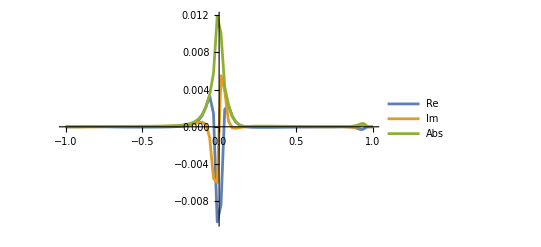

```mathematica
projTest=makeAngularProjector[-2,ellUse,mUse,NumY];

dataInt=angularIntegrandSamples[TTeukMinus2Compiled,projTest,Xmid];

ListLinePlot[{dataInt["Data"][[All,{1,2}]],dataInt["Data"][[All,{1,3}]],dataInt["Data"][[All,{1,4}]]},PlotLegends->{"Re","Im","Abs"},PlotRange->All]
```

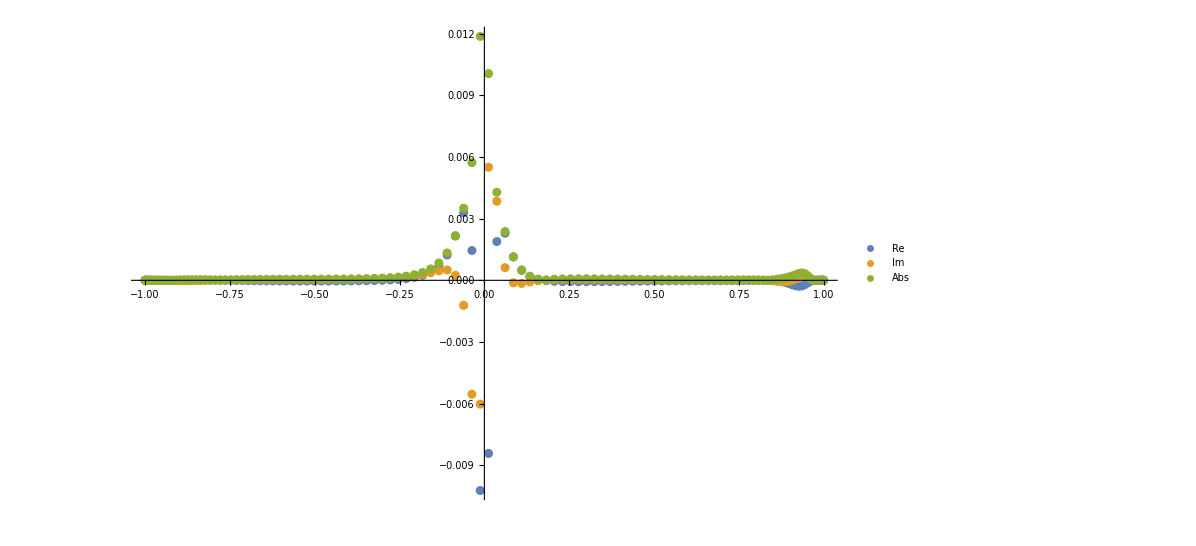

```mathematica
dataIntPoleCleanPlus=angularIntegrandSamples[TTeukMinus2PoleCleanPoint,projTest,Xmid];

ListPlot[{dataIntPoleCleanPlus["Data"][[All,{1,2}]],dataIntPoleCleanPlus["Data"][[All,{1,3}]],dataIntPoleCleanPlus["Data"][[All,{1,4}]]},PlotLegends->{"Re","Im","Abs"},PlotRange->All]
```

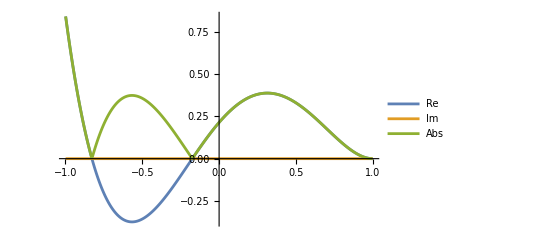

```mathematica
yPlotGrid=N[Subdivide[-0.999,0.999,400],60];

valsPlot=sphYDirect[sUse,ellUse,mUse,omegaUse,#,60]&/@yPlotGrid;

ListLinePlot[{Transpose[{yPlotGrid,Re/@valsPlot}],Transpose[{yPlotGrid,Im/@valsPlot}],Transpose[{yPlotGrid,Abs/@valsPlot}]},PlotLegends->{"Re","Im","Abs"},PlotRange->All]
```

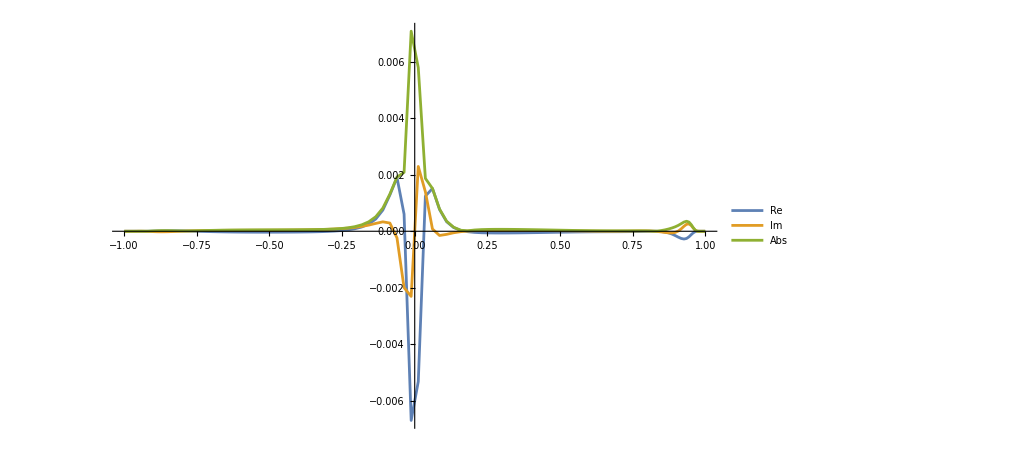

```mathematica
projTestMinus=makeAngularProjector[-2,ellUse,mUse,NumY];

dataHatMinus=angularIntegrandSamplesHat[TTeukMinus2PoleCleanHatPoint,-2,projTestMinus,Xmid];

ListLinePlot[{dataHatMinus["Data"][[All,{1,2}]],dataHatMinus["Data"][[All,{1,3}]],dataHatMinus["Data"][[All,{1,4}]]},PlotLegends->{"Re","Im","Abs"},PlotRange->All]
```

```mathematica
projTest=makeAngularProjector[-2,ellUse,mUse,24];

Keys[projTest]

{Min[projTest["yGrid"]],Max[projTest["yGrid"]],Min[projTest["YGrid"]],Max[projTest["YGrid"]]}
```

{s,ell,m,omega,yGrid,YGrid,Weights,SpheroidalValues,Projector}

{-0.995187,0.995187,-9.95187,9.95187}

```mathematica
ClearAll[Tspy];

Tspy[x_?NumericQ,Y_?NumericQ]:=Sow[Y];

Reap[projectTeukSourceAtXGL[Tspy,projTest][First[patchLeft["XGrid"]]]][[2,1]]//MinMax
```

{-9.95187,9.95187}

```mathematica
convMinus2Left=runAngularProjectionConvergence[TTeukMinus2Compiled,-2,ellUse,mUse,patchLeft["XGrid"],{24,32,48,64}];

vals24=convMinus2Left["ValuesByNY"][24];
vals32=convMinus2Left["ValuesByNY"][32];
vals48=convMinus2Left["ValuesByNY"][48];
vals64=convMinus2Left["ValuesByNY"][64];

convergencePairErrorsInterior[{vals24,vals32,vals48,vals64}]//MatrixForm
```

General::munfl: 1.7157×10^-8 (-1.58033×10^-301+1.26225×10^-300 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.7157×10^-8 (-1.56216×10^-301+1.2386×10^-300 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.7157×10^-8 (-1.51017×10^-301+1.17497×10^-300 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(0.00140807 | 0.429287
0.00265731 | 0.457866
0.00161365 | 0.22963)

```mathematica
nYListTest2={64,96,128,192};

convMinus2Left2=runAngularProjectionConvergence[TTeukMinus2Compiled,-2,ellUse,mUse,patchLeft["XGrid"],nYListTest2];

convMinus2Left2["PairwiseErrors"]
```

General::munfl: 1.7157×10^-8 (-1.58033×10^-301+1.26225×10^-300 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.7157×10^-8 (-1.56216×10^-301+1.2386×10^-300 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.7157×10^-8 (-1.51017×10^-301+1.17497×10^-300 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

<|{64,96}→<|MaxAbsDifference→0.00438079,RelativeMaxDifference→0.520928|>,{96,128}→<|MaxAbsDifference→0.00539105,RelativeMaxDifference→0.390874|>,{128,192}→<|MaxAbsDifference→0.00970251,RelativeMaxDifference→0.413125|>|>

```mathematica
(* exclude the radial endpoints *)
```

```mathematica
vals24=convMinus2Left["ValuesByNY"][24];
vals32=convMinus2Left["ValuesByNY"][32];
vals48=convMinus2Left["ValuesByNY"][48];
vals64=convMinus2Left["ValuesByNY"][64];

convergencePairErrorsInterior[{vals24,vals32,vals48,vals64}]
```

{{0.00140807,0.429287},{0.00265731,0.457866},{0.00161365,0.22963}}

```mathematica
pointwiseConvergenceTable[{vals24,vals32,vals48,vals64},patchLeft["XGrid"],{24,32,48,64},Range[1,6]]//MatrixForm
```

(<|Index→1,X→-1.,Values→<|24→-0.000201792+0.000160159 ⅈ,32→-0.000645174+0.000235015 ⅈ,48→-0.000853843+0.000282017 ⅈ,64→-0.000873215+0.000286017 ⅈ|>,SuccessiveAbsDiffs→{0.000449657,0.000213897,0.0000197802}|>
<|Index→2,X→-0.950484929106870051022419979242,Values→<|24→-0.0000374767+0.000147843 ⅈ,32→-0.000552056+0.000225086 ⅈ,48→-0.00082333+0.000282075 ⅈ,64→-0.000852078+0.0002879 ⅈ|>,SuccessiveAbsDiffs→{0.000520345,0.000277195,0.0000293322}|>
<|Index→3,X→-0.811746783480357471594849816978,Values→<|24→0.000563581+0.000125373 ⅈ,32→-0.000152899+0.000189125 ⅈ,48→-0.000698418+0.000277268 ⅈ,64→-0.0007865+0.000293174 ⅈ|>,SuccessiveAbsDiffs→{0.000719311,0.000552594,0.0000895063}|>
<|Index→4,X→-0.611264354373487420572429837736,Values→<|24→0.00177341+0.000180306 ⅈ,32→0.0010415+0.000142815 ⅈ,48→-0.000176114+0.000239701 ⅈ,64→-0.000591315+0.000290541 ⅈ|>,SuccessiveAbsDiffs→{0.000732875,0.00122146,0.000418302}|>
<|Index→5,X→-0.388745645626512579427570162264,Values→<|24→0.00274592+0.000450802 ⅈ,32→0.00326806+0.000279806 ⅈ,48→0.0022734+0.000172736 ⅈ,64→0.000874129+0.000219225 ⅈ|>,SuccessiveAbsDiffs→{0.00054943,0.00100041,0.00140004}|>
<|Index→6,X→-0.18826321651964252840515018302,Values→<|24→0.00172091+0.000595811 ⅈ,32→0.00312898+0.000598247 ⅈ,48→0.0057837+0.000481128 ⅈ,64→0.00701948+0.000328666 ⅈ|>,SuccessiveAbsDiffs→{0.00140807,0.00265731,0.00124514}|>)

### Quantify endpoint behaviour

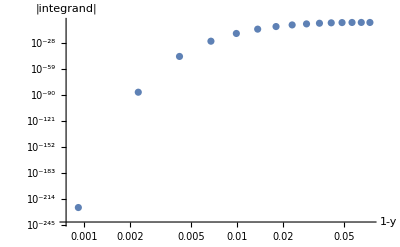

```mathematica
ClearAll[endpointScalingData];

endpointScalingData[data_Association,side_String:"Right",n_Integer:12]:=Module[{d},d=data["Data"];
Which[side==="Right",Transpose[{1-d[[-n;;,1]],d[[-n;;,4]]}],side==="Left",Transpose[{1+d[[1;;n,1]],d[[1;;n,4]]}]]];

rightScale=endpointScalingData[dataInt,"Right",16];

ListLogLogPlot[rightScale,PlotRange->All,AxesLabel->{"1-y","|integrand|"}]
```

```mathematica
convMinus2LeftCut=Association@Table[nY->projectTeukSourceOnXGridGL[TTeukMinus2Compiled,patchLeft["XGrid"],makeAngularProjectorCut[-2,ellUse,mUse,nY,10^-3]],{nY,{24,32,48,64}}];

convergencePairErrorsInterior[convMinus2LeftCut/@{24,32,48,64}]
```

{{0.00141018,0.429901},{0.00265759,0.45742},{0.00161668,0.230013}}

```mathematica
fitRight=LinearModelFit[Log[rightScale],x,x];

slopeRight=fitRight["BestFitParameters"][[2]];
pRight=-slopeRight;

{slopeRight,pRight}
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of LinearModelFit[{{-2.61414,-8.02688},{-2.7438,-7.94256},{-2.88277,-8.02793},{-3.03244,-8.35273},{-3.19454,-9.00964},«6»,{-4.99927,-59.327},{-5.47095,-101.137},{-6.08941,-199.125},{-6.98838,-515.108},{-8.65008,Indeterminate}},x,x][BestFitParameters] does not exist.

{LinearModelFit[{{-2.61414,-8.02688},{-2.7438,-7.94256},{-2.88277,-8.02793},{-3.03244,-8.35273},{-3.19454,-9.00964},{-3.37128,-10.1346},{-3.56549,-11.9385},{-3.78093,-14.7649},{-4.02274,-19.2001},{-4.29818,-26.3082},{-4.61803,-38.1742},{-4.99927,-59.327},{-5.47095,-101.137},{-6.08941,-199.125},{-6.98838,-515.108},{-8.65008,Indeterminate}},x,x][BestFitParameters]⟦2⟧,-LinearModelFit[{{-2.61414,-8.02688},{-2.7438,-7.94256},{-2.88277,-8.02793},{-3.03244,-8.35273},{-3.19454,-9.00964},{-3.37128,-10.1346},{-3.56549,-11.9385},{-3.78093,-14.7649},{-4.02274,-19.2001},{-4.29818,-26.3082},{-4.61803,-38.1742},{-4.99927,-59.327},{-5.47095,-101.137},{-6.08941,-199.125},{-6.98838,-515.108},{-8.65008,Indeterminate}},x,x][BestFitParameters]⟦2⟧}

```mathematica
convMinus2LeftCut=Association@Table[nY->projectTeukSourceOnXGridGL[TTeukMinus2Compiled,patchLeft["XGrid"],makeAngularProjectorCut[-2,ellUse,mUse,nY,10^-3]],{nY,{24,32,48,64}}];

convergencePairErrorsInterior[convMinus2LeftCut/@{24,32,48,64}]
```

{{0.00141018,0.429901},{0.00265759,0.45742},{0.00161668,0.230013}}

```mathematica
{{0.00016608578549158473,0.2297216591816104},{0.00017582672986160675,0.19584069657839617},{0.00006298209010347004,0.06559411706465064}}
```

{{0.000166086,0.229722},{0.000175827,0.195841},{0.0000629821,0.0655941}}

```mathematica
ClearAll[componentFfun];

componentFfun[key_String]:=Function[{x,Yval},TeffJetCompiled[key,mUse]["F"][x,Yval]];
```

```mathematica
componentPoleRegularityReport[keys_List,projector_Association,Xval_?NumericQ]:=Dataset@Table[Module[{q,f,right,left},q=componentSpinWeight[key];
f=componentFfun[key];
right=endpointPowerOfFunction[f,Xval,projector,"Right",16];
left=endpointPowerOfFunction[f,Xval,projector,"Left",16];
<|"component"->key,"spin q"->q,"expected right power"->expectedRightPower[mUse,q],"measured right power"->-right["PowerP"],"right divergence p"->right["PowerP"],"expected left power"->expectedLeftPower[mUse,q],"measured left power"->-left["PowerP"],"left divergence p"->left["PowerP"]|>],{key,keys}];
```

```mathematica
projDiag=makeAngularProjector[-2,ellUse,mUse,128];

componentPoleRegularityReport[{"nn","nmb","mbmb"},projDiag,Xmid]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of LinearModelFit[{{-2.61414,-7.77428},{-2.7438,-8.35947},{-2.88277,-9.12659},{-3.03244,-10.1414},{-3.19454,-11.4995},«6»,{-4.99927,-68.1125},{-5.47095,-111.393},{-6.08941,-211.279},{-6.98838,-529.987},{-8.65008,Indeterminate}},u,u][BestFitParameters] does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of LinearModelFit[{{-8.65008,Indeterminate},{-6.98838,-529.987},{-6.08941,-211.279},{-5.47095,-111.393},{-4.99927,-68.1125},«6»,{-3.19454,-11.4995},{-3.03244,-10.1414},{-2.88277,-9.12659},{-2.7438,-8.35947},{-2.61414,-7.77428}},u,u][BestFitParameters] does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

General::stop: Further output of LinearModelFit::desmat will be suppressed during this calculation.

Part::partw: Part 2 of LinearModelFit[{{-2.61414,-6.41767},{-2.7438,-6.95872},{-2.88277,-7.68631},{-3.03244,-8.66587},{-3.19454,-9.99261},«6»,{-4.99927,-66.4704},{-5.47095,-109.741},{-6.08941,-209.62},{-6.98838,-528.322},{-8.65008,Indeterminate}},u,u][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
ClearAll[TTeukMinus2PoleCleanTerms];

TTeukMinus2PoleCleanTerms[x_?NumericQ,Yval_?NumericQ]:=Module[{rawJets,hatJets,ops,t1,t2,t3,t4},rawJets=<|"nn"->evalCompiledJet2[TeffMinus2JetCompiled["nn"],x,Yval],"nmb"->evalCompiledJet2[TeffMinus2JetCompiled["nmb"],x,Yval],"mbmb"->evalCompiledJet2[TeffMinus2JetCompiled["mbmb"],x,Yval]|>;
hatJets=<|"nn"->hatJetFromRawJetNum[mUse,0,rawJets["nn"],Yval],"nmb"->hatJetFromRawJetNum[mUse,-1,rawJets["nmb"],Yval],"mbmb"->hatJetFromRawJetNum[mUse,-2,rawJets["mbmb"],Yval]|>;
ops=Association@KeyValueMap[Function[{key,op},key->evalCompiledOp[op,x,Yval]],Minus2ReducedOpsCompiled];
t1=applyTwoOpsToJet2Num[ops["M1"],ops["M2"],hatJets["nmb"]];
t2=-applyTwoOpsToJet2Num[ops["M1"],ops["M3"],hatJets["mbmb"]];
t3=applyTwoOpsToJet2Num[ops["M4"],ops["M5"],hatJets["nmb"]];
t4=-applyTwoOpsToJet2Num[ops["M4"],ops["M6"],hatJets["nn"]];
<|"M1M2_nmb"->poleWeightNum[mUse,-2,Yval] t1,"-M1M3_mbmb"->poleWeightNum[mUse,-2,Yval] t2,"M4M5_nmb"->poleWeightNum[mUse,-2,Yval] t3,"-M4M6_nn"->poleWeightNum[mUse,-2,Yval] t4,"Total"->poleWeightNum[mUse,-2,Yval] (t1+t2+t3+t4)|>];
```

```mathematica
ClearAll[termFunction,minus2TermPowerReport];

termFunction[name_String]:=Function[{x,Yval},TTeukMinus2PoleCleanTerms[x,Yval][name]];

minus2TermPowerReport[projector_Association,Xval_?NumericQ]:=Dataset@Table[Module[{f,right},f=termFunction[name];
right=endpointPowerOfFunction[f,Xval,projector,"Right",16];
<|"term"->name,"right endpoint p"->right["PowerP"],"right slope"->right["Slope"]|>],{name,{"M1M2_nmb","-M1M3_mbmb","M4M5_nmb","-M4M6_nn","Total"}}];
```

```mathematica
minus2TermPowerReport[projDiag,Xmid]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of LinearModelFit[{{-2.61414,-8.50453},{-2.7438,-8.77534},{-2.88277,-9.22835},{-3.03244,-9.92551},{-3.19454,-10.9584},«6»,{-4.99927,-64.5191},{-5.47095,-107.069},{-6.08941,-206.009},{-6.98838,-523.356},{-8.65008,Indeterminate}},u,u][BestFitParameters] does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of LinearModelFit[{{-2.61414,-11.661},{-2.7438,-12.2447},{-2.88277,-13.0099},{-3.03244,-14.0223},{-3.19454,-15.3772},«6»,{-4.99927,-71.9532},{-5.47095,-115.228},{-6.08941,-215.109},{-6.98838,-533.813},{-8.65008,Indeterminate}},u,u][BestF…eters] does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

General::stop: Further output of LinearModelFit::desmat will be suppressed during this calculation.

Part::partw: Part 2 of LinearModelFit[{{-2.61414,-9.35822},{-2.7438,-9.63361},{-2.88277,-10.0898},{-3.03244,-10.7893},{-3.19454,-11.8237},«6»,{-4.99927,-65.3881},{-5.47095,-107.938},{-6.08941,-206.878},{-6.98838,-524.225},{-8.65008,Indeterminate}},u,u][BestF…meters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

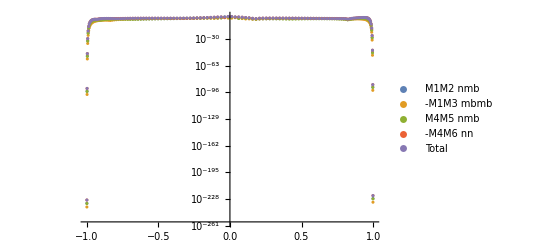

```mathematica
ClearAll[angularTermSamples];

angularTermSamples[projector_Association,Xval_?NumericQ,name_String]:=Module[{yGrid,YGrid,sph,vals},yGrid=projector["yGrid"];
YGrid=projector["YGrid"];
sph=projector["SpheroidalValues"];
vals=Table[Conjugate[sph[[j]]] termFunction[name][Xval,YGrid[[j]]],{j,Length[yGrid]}];
Transpose[{yGrid,Abs[vals]}]];

ListLogPlot[Table[angularTermSamples[projDiag,Xmid,name],{name,{"M1M2_nmb","-M1M3_mbmb","M4M5_nmb","-M4M6_nn","Total"}}],PlotLegends->{"M1M2 nmb","-M1M3 mbmb","M4M5 nmb","-M4M6 nn","Total"},PlotRange->All]
```

```mathematica
ClearAll[endpointPowerFitFromData];

endpointPowerFitFromData[data_List]:=Module[{logdata,fit,slope},logdata=Log/@data;
fit=LinearModelFit[logdata,u,u];
slope=fit["BestFitParameters"][[2]];
<|"Slope"->slope,"DivergencePower"->-slope,"Fit"->fit|>];

ClearAll[componentEndpointData,componentEndpointReport];

componentEndpointData[key_String,Xval_?NumericQ,projector_Association,side_String:"Right",n_Integer:16]:=Module[{yGrid,YGrid,inds,delta,vals},yGrid=projector["yGrid"];
YGrid=projector["YGrid"];
inds=If[side==="Right",Range[Length[yGrid]-n+1,Length[yGrid]],Range[1,n]];
delta=If[side==="Right",1-yGrid[[inds]],1+yGrid[[inds]]];
vals=Abs[Table[evalCompiledJet2[TeffMinus2JetCompiled[key],Xval,YGrid[[j]]]["F"],{j,inds}]];
Transpose[{delta,vals}]];

componentEndpointReport[key_String,q_Integer,Xval_?NumericQ,projector_Association]:=Module[{rightData,leftData,rightFit,leftFit},rightData=componentEndpointData[key,Xval,projector,"Right",16];
leftData=componentEndpointData[key,Xval,projector,"Left",16];
rightFit=endpointPowerFitFromData[rightData];
leftFit=endpointPowerFitFromData[leftData];
<|"Component"->key,"q"->q,"ExpectedRightVanishingPower"->Abs[mUse+q]/2,"MeasuredRightSlope"->rightFit["Slope"],"MeasuredRightDivergencePower"->rightFit["DivergencePower"],"ExpectedLeftVanishingPower"->Abs[mUse-q]/2,"MeasuredLeftSlope"->leftFit["Slope"],"MeasuredLeftDivergencePower"->leftFit["DivergencePower"]|>];
```

```mathematica
Dataset[{componentEndpointReport["nn",0,Xmid,projDiag],componentEndpointReport["nmb",-1,Xmid,projDiag],componentEndpointReport["mbmb",-2,Xmid,projDiag]}]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of LinearModelFit[{{-2.61414,-7.77428},{-2.7438,-8.35947},{-2.88277,-9.12659},{-3.03244,-10.1414},{-3.19454,-11.4995},«6»,{-4.99927,-68.1125},{-5.47095,-111.393},{-6.08941,-211.279},{-6.98838,-529.987},{-8.65008,Indeterminate}},u,u][BestFitParameters] does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of LinearModelFit[{{-8.65008,Indeterminate},{-6.98838,-529.987},{-6.08941,-211.279},{-5.47095,-111.393},{-4.99927,-68.1125},«6»,{-3.19454,-11.4995},{-3.03244,-10.1414},{-2.88277,-9.12659},{-2.7438,-8.35947},{-2.61414,-7.77428}},u,u][BestFitParameters] does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

General::stop: Further output of LinearModelFit::desmat will be suppressed during this calculation.

Part::partw: Part 2 of LinearModelFit[{{-2.61414,-6.41767},{-2.7438,-6.95872},{-2.88277,-7.68631},{-3.03244,-8.66587},{-3.19454,-9.99261},«6»,{-4.99927,-66.4704},{-5.47095,-109.741},{-6.08941,-209.62},{-6.98838,-528.322},{-8.65008,Indeterminate}},u,u][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

#### Smoothing at the poles (only needed for display)

```mathematica
ClearAll[smoothCompactBump,angularWindowY];

smoothCompactBump[u_?NumericQ]:=If[Abs[u]<1,Exp[-1/(1-u^2)],0];

angularWindowY[Y_?NumericQ,Ymax_?NumericQ]:=smoothCompactBump[Y/Ymax]/smoothCompactBump[0];

YmaxTest=0.9r0val;

TTeukMinus2Windowed[x_?NumericQ,Y_?NumericQ]:=TTeukMinus2Compiled[x,Y] angularWindowY[Y,YmaxTest];
```

```mathematica
convMinus2LeftWindowed=runAngularProjectionConvergence[TTeukMinus2Windowed,-2,ellUse,mUse,patchLeft["XGrid"],{24,32,48,64}];

convMinus2LeftWindowed["PairwiseErrors"]
```

<|{24,32}→<|MaxAbsDifference→0.00140468,RelativeMaxDifference→0.412045|>,{32,48}→<|MaxAbsDifference→0.00265724,RelativeMaxDifference→0.448347|>,{48,64}→<|MaxAbsDifference→0.00161334,RelativeMaxDifference→0.225499|>|>

```mathematica
ClearAll[smoothStep01,angularPlateauWindowY];

smoothStep01[u_?NumericQ]:=Module[{a,b},Which[u<=0,0,u>=1,1,True,a=Exp[-1/u];
b=Exp[-1/(1-u)];
a/(a+b)]];

angularPlateauWindowY[Y_?NumericQ,Yin_?NumericQ,Yout_?NumericQ]:=Module[{a=Abs[Y]},1-smoothStep01[(a-Yin)/(Yout-Yin)]];
```

```mathematica
Yin=0.6 r0val;
Yout=0.9 r0val;

TTeukMinus2YWindowed[x_?NumericQ,Y_?NumericQ]:=TTeukMinus2Compiled[x,Y] angularPlateauWindowY[Y,Yin,Yout];
```

```mathematica
convMinus2LeftWindowed=runAngularProjectionConvergence[TTeukMinus2Windowed,-2,ellUse,mUse,patchLeft["XGrid"],{24,32,48,64,72}];

convMinus2LeftWindowed["PairwiseErrors"]
```

<|{24,32}→<|MaxAbsDifference→0.00140468,RelativeMaxDifference→0.412045|>,{32,48}→<|MaxAbsDifference→0.00265724,RelativeMaxDifference→0.448347|>,{48,64}→<|MaxAbsDifference→0.00161334,RelativeMaxDifference→0.225499|>,{64,72}→<|MaxAbsDifference→0.000957579,RelativeMaxDifference→0.133871|>|>

## Parallelize projections

```mathematica
ParallelEvaluate[Needs["NumericalDifferentialEquationAnalysis`"]];
```

```mathematica
(* ============================================================*)
(*Fast projection using precomputed projector*)
(* ============================================================*)
ClearAll[projectAtXFast,projectOnXGridFast];

projectAtXFast[Tfun_,projector_Association,Xval_?NumericQ]:=Module[{YGrid,projWeights,vals},YGrid=projector["YGrid"];
projWeights=projector["Projector"];
vals=Table[Tfun[Xval,YGrid[[j]]],{j,Length[YGrid]}];
If[!VectorQ[vals,NumericQ],Print["Non-numeric values at X = ",Xval];
Print[Short[vals,3]];
Abort[];];
Total[projWeights vals]];

projectOnXGridFast[Tfun_,projector_Association,XGrid_List]:=Table[projectAtXFast[Tfun,projector,X],{X,XGrid}];
```

```mathematica
(* ============================================================*)
(*Build+2 tasks with projectors precomputed on master kernel*)
(* ============================================================*)
ClearAll[makePlus2ProjectionTasksMain];

makePlus2ProjectionTasksMain[ellMax_Integer,m_Integer,nY_Integer,patchAssoc_Association]:=Module[{ellMin,ellList,projectors,tasks},ellMin=Max[Abs[m],2];
ellList=Range[ellMin,ellMax];
Print["Building projectors on master kernel..."];
projectors=Association@Table[ell->makeAngularProjector[+2,ell,m,nY],{ell,ellList}];
tasks=Flatten[Table[<|"s"->+2,"ell"->ell,"m"->m,"nY"->nY,"Patch"->patchName,"XGrid"->patchAssoc[patchName],"Projector"->projectors[ell]|>,{ell,ellList},{patchName,Keys[patchAssoc]}],1];
tasks];
```

```mathematica
(* ============================================================*)
(*One parallel task: project one ell on one patch*)
(* ============================================================*)
ClearAll[runPlus2ProjectionTaskNoProjector];

runPlus2ProjectionTaskNoProjector[task_Association]:=Module[
{ell,m,nY,patchName,XGrid,projector,timing,vals},
ell=task["ell"];
m=task["m"];
nY=task["nY"];
patchName=task["Patch"];
XGrid=task["XGrid"];
projector=task["Projector"];
timing=AbsoluteTiming[
vals=projectOnXGridFast[TTeukPlus2Compiled,projector,XGrid];
];
{+2,ell,patchName}->
<|"s"->+2,"ell"->ell,"m"->m,"Patch"->patchName,"nY"->nY,"XGrid"->XGrid,"Values"->vals,"TimeSeconds"->timing[[1]],"SourceBuild"->"windowed-at-perturbation-level"|>];
```

```mathematica
(* ============================================================*)
(*Parallel+2 projections,projectors built on master kernel*)
(* ============================================================*)
ClearAll[runPlus2ProjectionsParallelMainProjectors];

runPlus2ProjectionsParallelMainProjectors[ellMax_Integer:15,nY_Integer:128]:=
Module[
{m,patchAssoc,tasks,results},
m=Round[mModeval];
patchAssoc=<|"Left"->patchLeft["XGrid"],"Right"->patchRight["XGrid"]|>;
tasks=makePlus2ProjectionTasksMain[ellMax,m,nY,patchAssoc];
Print["Number of tasks: ",Length[tasks]];
Print["ell range: ",Range[Max[Abs[m],2],ellMax]];
Print["nY = ",nY];
(*Only distribute numerical projection machinery.Do NOT distribute makeAngularProjector;projectors are already built.*)DistributeDefinitions[TTeukPlus2Compiled,projectAtXFast,projectOnXGridFast,runPlus2ProjectionTaskNoProjector];
results=ParallelMap[runPlus2ProjectionTaskNoProjector,tasks,Method->"CoarsestGrained"];
Association[results]];
```

```mathematica
ellMaxPlus=15;
nYProd=128;

plus2ProjectionResults=runPlus2ProjectionsParallelMainProjectors[ellMaxPlus,nYProd];
```

Building projectors on master kernel...

SpinWeightedSpheroidalHarmonicS::prec: Spin-weighted spheroidal harmonic cannot be computed using "Leaver" method with the given working precision. To obtain an accurate result either provide a higher precision input spheroidicity or use the "SphericalExpansion" method instead.

Number of tasks: 28

ell range: {2,3,4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

```mathematica
Keys[plus2ProjectionResults]

plus2ProjectionResults[{+2,ellUse,"Left"}]["Values"]
plus2ProjectionResults[{+2,ellUse,"Right"}]["Values"]
```

{{2,2,Left},{2,2,Right},{2,3,Left},{2,3,Right},{2,4,Left},{2,4,Right},{2,5,Left},{2,5,Right},{2,6,Left},{2,6,Right},{2,7,Left},{2,7,Right},{2,8,Left},{2,8,Right},{2,9,Left},{2,9,Right},{2,10,Left},{2,10,Right},{2,11,Left},{2,11,Right},{2,12,Left},{2,12,Right},{2,13,Left},{2,13,Right},{2,14,Left},{2,14,Right},{2,15,Left},{2,15,Right}}

{-0.00592983-0.000858523 ⅈ,-0.00592187-0.000859793 ⅈ,-0.00589811-0.000863607 ⅈ,-0.00585886-0.000869975 ⅈ,-0.00580467-0.000878908 ⅈ,-0.00573626-0.000890415 ⅈ,-0.00565456-0.000904495 ⅈ,-0.00556066-0.000921125 ⅈ,-0.0054558-0.000940258 ⅈ,-0.00534133-0.000961802 ⅈ,-0.00521875-0.000985619 ⅈ,-0.00508957-0.00101151 ⅈ,-0.00495533-0.0010392 ⅈ,-0.00481737-0.00106829 ⅈ,-0.0046762-0.00109818 ⅈ,-0.00452952-0.00112763 ⅈ,-0.0043655-0.00115376 ⅈ,-0.00414086-0.00116888 ⅈ,-0.00371434-0.00115281 ⅈ,-0.0026612-0.00105686 ⅈ,0.0001824-0.000779721 ⅈ,0.00765216-0.000158666 ⅈ,0.0256123+0.000935262 ⅈ,0.0632483+0.00220552 ⅈ,0.127316+0.00213597 ⅈ,0.20507-0.00230283 ⅈ,0.252656-0.0130185 ⅈ,0.231309-0.0264922 ⅈ,0.159284-0.0362208 ⅈ,0.0866211-0.0400212 ⅈ,0.0414492-0.0403797 ⅈ,0.0269804-0.0401499 ⅈ}

{0.0268696-0.0401474 ⅈ,0.0129524-0.0397436 ⅈ,-0.024243-0.0375654 ⅈ,-0.0666817-0.0313805 ⅈ,-0.0833383-0.0203543 ⅈ,-0.0589465-0.00813352 ⅈ,-0.0190072-0.00019925 ⅈ,0.00466235+0.0022877 ⅈ,0.00896797+0.00198204 ⅈ,0.0053514+0.00117417 ⅈ,0.001381+0.000623945 ⅈ,-0.00101008+0.00033992 ⅈ,-0.00213391+0.000194426 ⅈ,-0.00258657+0.000103644 ⅈ,-0.002746+0.0000317904 ⅈ,-0.00279043-0.000032848 ⅈ,-0.00279195-0.0000931272 ⅈ,-0.00277728-0.000149332 ⅈ,-0.00275603-0.000201219 ⅈ,-0.00273184-0.000248565 ⅈ,-0.0027063-0.000291263 ⅈ,-0.00268038-0.000329325 ⅈ,-0.0026548-0.000362852 ⅈ,-0.0026302-0.000392009 ⅈ,-0.00260713-0.000417003 ⅈ,-0.0025861-0.00043806 ⅈ,-0.00256755-0.000455411 ⅈ,-0.00255187-0.000469272 ⅈ,-0.00253935-0.000479835 ⅈ,-0.00253023-0.000487261 ⅈ,-0.0025247-0.000491668 ⅈ,-0.00252284-0.000493129 ⅈ}

```mathematica
(*DumpSave["TTeukPlus2_ell2to15_m2_windowed_nY128.mx",plus2ProjectionResults];*)
```

```mathematica
ClearAll[runPlus2ProjectionsParallelWithPatches];

runPlus2ProjectionsParallelWithPatches[ellMax_Integer:15,nY_Integer:128,patchAssoc_Association]:=Module[{m,tasks,results},m=Round[mModeval];
tasks=makePlus2ProjectionTasksMain[ellMax,m,nY,patchAssoc];
Print["Number of tasks: ",Length[tasks]];
Print["ell range: ",Range[Max[Abs[m],2],ellMax]];
Print["nY = ",nY];
Print["radial grid sizes: ",Map[Length,patchAssoc]];
DistributeDefinitions[TTeukPlus2Compiled,projectAtXFast,projectOnXGridFast,runPlus2ProjectionTaskNoProjector];
results=ParallelMap[runPlus2ProjectionTaskNoProjector,tasks,Method->"CoarsestGrained"];
Association[results]];
```

```mathematica
ellMaxPlus=15;
nYProd=128;

plus2ProjectionResults=runPlus2ProjectionsParallelMainProjectors[ellMaxPlus,nYProd];
```

Building projectors on master kernel...

SpinWeightedSpheroidalHarmonicS::prec: Spin-weighted spheroidal harmonic cannot be computed using "Leaver" method with the given working precision. To obtain an accurate result either provide a higher precision input spheroidicity or use the "SphericalExpansion" method instead.

Number of tasks: 28

ell range: {2,3,4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

```mathematica
patchAssocProd=<|"Left"->patchLeftProd["XGrid"],"Right"->patchRightProd["XGrid"]|>;

ellMaxPlus=15;
nYProd=128;
```

```mathematica
plus2ProjectionResultsNX128=runPlus2ProjectionsParallelWithPatches[ellMaxPlus,nYProd,patchAssocProd];
```

Building projectors on master kernel...

SpinWeightedSpheroidalHarmonicS::prec: Spin-weighted spheroidal harmonic cannot be computed using "Leaver" method with the given working precision. To obtain an accurate result either provide a higher precision input spheroidicity or use the "SphericalExpansion" method instead.

Number of tasks: 28

ell range: {2,3,4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

```mathematica
plus2ProjectionResultsNX128
```

```mathematica
(*DumpSave["TTeukPlus2_ell2to15_run2_windowed_nY128_nX128perSide.mx",plus2ProjectionResultsNX128];*)
```

## Parallelize over all m

```mathematica
(* ============================================================*)(*Per-m plus-2 projection driver*)(* ============================================================*)ClearAll[ellListForM,makePlus2ProjectionTasksForM,runPlus2ProjectionTaskNoProjector,runPlus2ProjectionsForM];

ellListForM[s_Integer,ellMax_Integer,m_Integer]:=Range[Max[Abs[m],Abs[s]],ellMax];


makePlus2ProjectionTasksForM[ellMax_Integer,m_Integer,nY_Integer,patchAssoc_Association,Tfun_]:=Module[{ellList,projectors,tasks},ellList=ellListForM[+2,ellMax,m];
Print["Building projectors on master kernel for m = ",m,"..."];
projectors=Association@Table[ell->makeAngularProjector[+2,ell,m,nY],{ell,ellList}];
tasks=Flatten[Table[<|"s"->+2,"ell"->ell,"m"->m,"nY"->nY,"Patch"->patchName,"XGrid"->patchAssoc[patchName],"Projector"->projectors[ell],"Tfun"->Tfun|>,{ell,ellList},{patchName,Keys[patchAssoc]}],1];
tasks];
```

```mathematica
runPlus2ProjectionTaskNoProjector[task_Association]:=Module[{ell,m,nY,patchName,XGrid,projector,Tfun,timing,vals},ell=task["ell"];
m=task["m"];
nY=task["nY"];
patchName=task["Patch"];
XGrid=task["XGrid"];
projector=task["Projector"];
Tfun=task["Tfun"];
timing=AbsoluteTiming[vals=projectOnXGridFast[Tfun,projector,XGrid];];
{+2,m,ell,patchName}-><|"s"->+2,"ell"->ell,"m"->m,"Patch"->patchName,"nY"->nY,"XGrid"->XGrid,"Values"->vals,"TimeSeconds"->timing[[1]],"SourceBuild"->"windowed-at-perturbation-level"|>];
```

```mathematica
runPlus2ProjectionsForM[m_Integer,ellMax_Integer:15,nY_Integer:128,patchAssoc_Association,Tfun_]:=Module[{tasks,results},tasks=makePlus2ProjectionTasksForM[ellMax,m,nY,patchAssoc,Tfun];
Print["m = ",m];
Print["Number of tasks: ",Length[tasks]];
Print["ell range: ",ellListForM[+2,ellMax,m]];
Print["nY = ",nY];
Print["radial grid sizes: ",Map[Length,patchAssoc]];
DistributeDefinitions[projectAtXFast,projectOnXGridFast,runPlus2ProjectionTaskNoProjector];
results=ParallelMap[runPlus2ProjectionTaskNoProjector,tasks,Method->"CoarsestGrained"];
Association[results]];
```

```mathematica
(* ============================================================*)(*Result cache helpers*)(* ============================================================*)ClearAll[ensureDirectory,safeName,writeMXObject,readMXObject,plus2MCacheFile];

ensureDirectory[dir_String]:=If[!DirectoryQ[dir],CreateDirectory[dir,CreateIntermediateDirectories->True]];

safeName[x_]:=StringReplace[ToString[x,InputForm],RegularExpression["[^A-Za-z0-9_-]"]->"_"];

ClearAll[$TeffMXObject];

writeMXObject[file_String,obj_]:=Module[{dir,tmp},dir=DirectoryName[file];
ensureDirectory[dir];
tmp=FileNameJoin[{dir,"."<>FileBaseName[file]<>"-"<>CreateUUID[]<>".mx"}];
Clear[$TeffMXObject];
$TeffMXObject=obj;
DumpSave[tmp,$TeffMXObject];
If[FileExistsQ[file],DeleteFile[file]];
RenameFile[tmp,file];
Clear[$TeffMXObject];
file];

readMXObject[file_String]:=Module[{},Clear[$TeffMXObject];
Get[file];
$TeffMXObject];

plus2MCacheFile[root_String,ellMax_Integer,nY_Integer,m_Integer]:=FileNameJoin[{root,"Plus2Projections","ellMax"<>ToString[ellMax],"nY"<>ToString[nY],"m"<>ToString[m]<>".mx"}];

(* ============================================================*)
(*All-m plus-2 projection driver*)
(* ============================================================*)
ClearAll[runPlus2ProjectionsAllM];

Options[runPlus2ProjectionsAllM]={"MList"->Automatic,"CacheRoot"->FileNameJoin[{NotebookDirectory[],"TeffProjectionCache"}],"Overwrite"->False};

runPlus2ProjectionsAllM[ellMax_Integer:15,nY_Integer:128,patchAssoc_Association,TfunBuilder_,OptionsPattern[]]:=Module[{mList,cacheRoot,overwrite,allResults,m,file,Tfun,res},mList=OptionValue["MList"];
If[mList===Automatic,mList=Range[-ellMax,ellMax]];
cacheRoot=OptionValue["CacheRoot"];
overwrite=TrueQ[OptionValue["Overwrite"]];
ensureDirectory[cacheRoot];
allResults=<||>;
Do[file=plus2MCacheFile[cacheRoot,ellMax,nY,m];
If[FileExistsQ[file]&&!overwrite,Print["Loading cached plus-2 projection for m = ",m];
res=readMXObject[file];,Print["Computing plus-2 projection for m = ",m];
Tfun=TfunBuilder[m];
res=runPlus2ProjectionsForM[m,ellMax,nY,patchAssoc,Tfun];
writeMXObject[file,res];];
allResults[m]=res;,{m,mList}];
allResults];
```

```mathematica
ClearAll[plus2TfunOfM];

plus2TfunOfM[m_Integer]:=plus2TfunOfM[m]=Module[{mUse=m},(*Replace this line by your existing m-dependent compiled source builder.*)TTeukPlus2CompiledForM[m]];
```

```mathematica
ClearAll[plus2TfunOfM];

plus2TfunOfM[m_Integer]:=plus2TfunOfM[m]=Module[{},mUse=m;
mModeval=m;
(*Rebuild the m-dependent source here.Use your existing build cell/function.*)buildTTeukPlus2CompiledForCurrentM[];
TTeukPlus2Compiled];
```

```mathematica
patchAssocProd=<|"Left"->patchLeftProd["XGrid"],"Right"->patchRightProd["XGrid"]|>;

ellMaxPlus=15;
nYProd=128;

plus2AllMResults=runPlus2ProjectionsAllM[ellMaxPlus,nYProd,patchAssocProd,plus2TfunOfM,"MList"->Range[-ellMaxPlus,ellMaxPlus],"Overwrite"->False];
```

Computing plus-2 projection for m = -15

Building projectors on master kernel for m = -15...

m = -15

Number of tasks: 2

ell range: {15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -14

Building projectors on master kernel for m = -14...

m = -14

Number of tasks: 4

ell range: {14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -13

Building projectors on master kernel for m = -13...

m = -13

Number of tasks: 6

ell range: {13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -12

Building projectors on master kernel for m = -12...

m = -12

Number of tasks: 8

ell range: {12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -11

Building projectors on master kernel for m = -11...

m = -11

Number of tasks: 10

ell range: {11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -10

Building projectors on master kernel for m = -10...

m = -10

Number of tasks: 12

ell range: {10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -9

Building projectors on master kernel for m = -9...

m = -9

Number of tasks: 14

ell range: {9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -8

Building projectors on master kernel for m = -8...

m = -8

Number of tasks: 16

ell range: {8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -7

Building projectors on master kernel for m = -7...

m = -7

Number of tasks: 18

ell range: {7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -6

Building projectors on master kernel for m = -6...

m = -6

Number of tasks: 20

ell range: {6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -5

Building projectors on master kernel for m = -5...

m = -5

Number of tasks: 22

ell range: {5,6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -4

Building projectors on master kernel for m = -4...

SpinWeightedSpheroidalHarmonicS::prec: Spin-weighted spheroidal harmonic cannot be computed using "Leaver" method with the given working precision. To obtain an accurate result either provide a higher precision input spheroidicity or use the "SphericalExpansion" method instead.

General::stop: Further output of SpinWeightedSpheroidalHarmonicS::prec will be suppressed during this calculation.

m = -4

Number of tasks: 24

ell range: {4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -3

Building projectors on master kernel for m = -3...

m = -3

Number of tasks: 26

ell range: {3,4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -2

Building projectors on master kernel for m = -2...

m = -2

Number of tasks: 28

ell range: {2,3,4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -1

Building projectors on master kernel for m = -1...

m = -1

Number of tasks: 28

ell range: {2,3,4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 0

Building projectors on master kernel for m = 0...

m = 0

Number of tasks: 28

ell range: {2,3,4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 1

Building projectors on master kernel for m = 1...

m = 1

Number of tasks: 28

ell range: {2,3,4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 2

Building projectors on master kernel for m = 2...

m = 2

Number of tasks: 28

ell range: {2,3,4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 3

Building projectors on master kernel for m = 3...

m = 3

Number of tasks: 26

ell range: {3,4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 4

Building projectors on master kernel for m = 4...

m = 4

Number of tasks: 24

ell range: {4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 5

Building projectors on master kernel for m = 5...

m = 5

Number of tasks: 22

ell range: {5,6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 6

Building projectors on master kernel for m = 6...

m = 6

Number of tasks: 20

ell range: {6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 7

Building projectors on master kernel for m = 7...

m = 7

Number of tasks: 18

ell range: {7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 8

Building projectors on master kernel for m = 8...

m = 8

Number of tasks: 16

ell range: {8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 9

Building projectors on master kernel for m = 9...

m = 9

Number of tasks: 14

ell range: {9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 10

Building projectors on master kernel for m = 10...

m = 10

Number of tasks: 12

ell range: {10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 11

Building projectors on master kernel for m = 11...

m = 11

Number of tasks: 10

ell range: {11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 12

Building projectors on master kernel for m = 12...

m = 12

Number of tasks: 8

ell range: {12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 13

Building projectors on master kernel for m = 13...

m = 13

Number of tasks: 6

ell range: {13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 14

Building projectors on master kernel for m = 14...

m = 14

Number of tasks: 4

ell range: {14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 15

Building projectors on master kernel for m = 15...

m = 15

Number of tasks: 2

ell range: {15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

### Spherical Harmonic Y Projections

```mathematica
ClearAll[projectTeff$mMode$y];

Options[projectTeff$mMode$y]=
{
"EndpointCutoff"->0,
WorkingPrecision->MP,
AccuracyGoal->Automatic,
PrecisionGoal->Automatic,
MaxRecursion->12
};

projectTeff$mMode$y[s_,l_,m_][TeffHead_][X_?NumericQ,opts:OptionsPattern[]]:=
Module[
{eps,wp,acc,prec,maxrec,θ},
eps=OptionValue["EndpointCutoff"];
wp=OptionValue[WorkingPrecision];
acc=OptionValue[AccuracyGoal];
prec=OptionValue[PrecisionGoal];
maxrec=OptionValue[MaxRecursion];
(* Nintegration local adapative *)
2 Pi NIntegrate[
TeffHead[m][X,-r0val y]*
Conjugate[SpinWeightedSphericalHarmonicY[s,l,m,ArcCos[y],N64@0]],
{y,-1+eps,1-eps},
Method->{"LocalAdaptive","SymbolicProcessing"->0},
WorkingPrecision->wp,
AccuracyGoal->acc,
PrecisionGoal->prec,
MaxRecursion->maxrec]
];
```

```mathematica
projectTeff$mModerθ[0,0,0][Teffmmb$MMode$XY$numeric][10.3]
```

projectTeff$mModerθ[0,0,0][Teffmmb$MMode$XY$numeric][10.3]

## Projection plots

```mathematica
(* ============================================================*)
(*Basic inspection of+2 projected source data*)
(* ============================================================*)
resPlus=plus2ProjectionResultsNX128;

Keys[resPlus]

Dataset[Values[resPlus][[All,{"s","ell","m","Patch","nY","TimeSeconds"}]]]
```

{{2,2,Left},{2,2,Right},{2,3,Left},{2,3,Right},{2,4,Left},{2,4,Right},{2,5,Left},{2,5,Right},{2,6,Left},{2,6,Right},{2,7,Left},{2,7,Right},{2,8,Left},{2,8,Right},{2,9,Left},{2,9,Right},{2,10,Left},{2,10,Right},{2,11,Left},{2,11,Right},{2,12,Left},{2,12,Right},{2,13,Left},{2,13,Right},{2,14,Left},{2,14,Right},{2,15,Left},{2,15,Right}}

```mathematica
ClearAll[projectionEntryCheck];

projectionEntryCheck[res_Association]:=Dataset@KeyValueMap[Function[{key,entry},<|"Key"->key,"nX"->Length[entry["XGrid"]],"nVals"->Length[entry["Values"]],"All numeric"->VectorQ[entry["Values"],NumericQ],"MaxAbs"->Max[Abs[entry["Values"]]],"MinAbs"->Min[Abs[entry["Values"]]]|>],res];

projectionEntryCheck[resPlus]
```

```mathematica
ClearAll[getProjData,getJoinedProjData,plotProjectedMode];

getProjData[res_Association,s_Integer,ell_Integer,patch_String]:=Module[{entry,X,vals},entry=res[{s,ell,patch}];
X=entry["XGrid"];
vals=entry["Values"];
<|"X"->X,"Values"->vals,"ReData"->Transpose[{X,Re[vals]}],"ImData"->Transpose[{X,Im[vals]}],"AbsData"->Transpose[{X,Abs[vals]}]|>];

getJoinedProjData[res_Association,s_Integer,ell_Integer]:=Module[{left,right,X,vals,order},left=getProjData[res,s,ell,"Left"];
right=getProjData[res,s,ell,"Right"];
X=Join[left["X"],right["X"]];
vals=Join[left["Values"],right["Values"]];
order=Ordering[X];
<|"X"->X[[order]],"Values"->vals[[order]],"ReData"->Transpose[{X[[order]],Re[vals[[order]]]}],"ImData"->Transpose[{X[[order]],Im[vals[[order]]]}],"AbsData"->Transpose[{X[[order]],Abs[vals[[order]]]}]|>];

plotProjectedMode[res_Association,s_Integer,ell_Integer]:=Module[{data},data=getJoinedProjData[res,s,ell];
ListLinePlot[{data["ReData"],data["ImData"],data["AbsData"]},PlotLegends->{"Re","Im","Abs"},PlotRange->All,AxesLabel->{"X",Row[{"TTeuk, s = ",s,", ell = ",ell,", m = ",mUse}]},ImageSize->Large]];
```

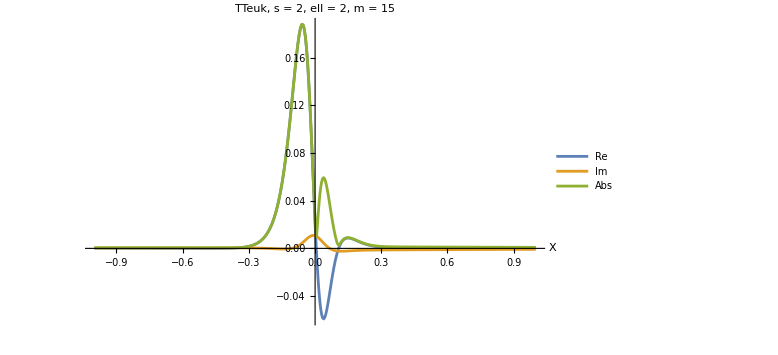

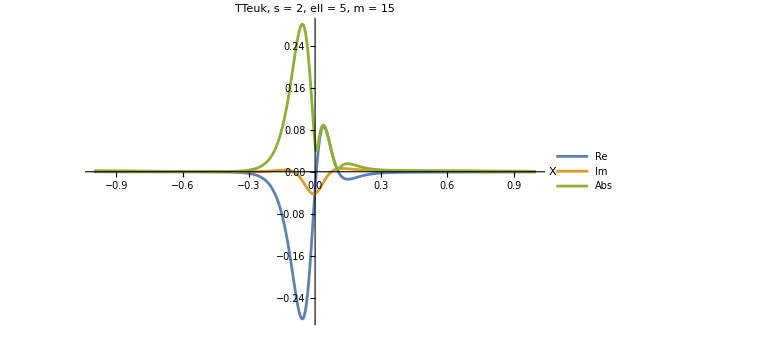

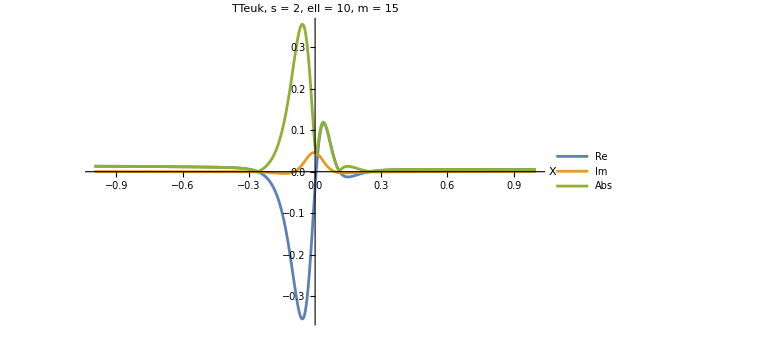

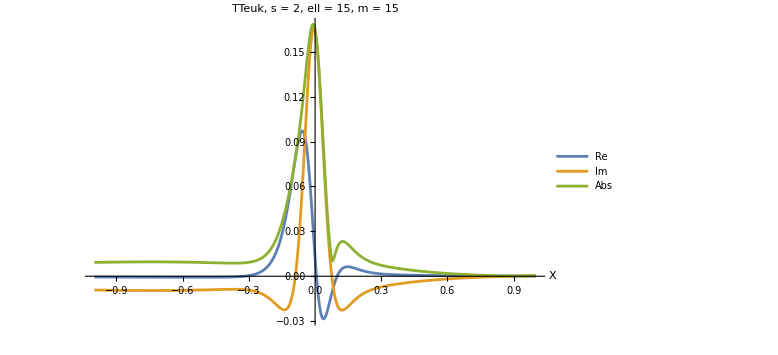

```mathematica
plotProjectedMode[resPlus,+2,2]
plotProjectedMode[resPlus,+2,5]
plotProjectedMode[resPlus,+2,10]
plotProjectedMode[resPlus,+2,15]
```

```mathematica
ellListPlus=Range[Max[Abs[mUse],2],15];
```

```mathematica
ClearAll[patchEdgeCheck];

patchEdgeCheck[res_Association,s_Integer,ell_Integer]:=Module[{left,right},left=getProjData[res,s,ell,"Left"];
right=getProjData[res,s,ell,"Right"];
<|"ell"->ell,"X left closest to 0"->Last[left["X"]],"Value left closest to 0"->Last[left["Values"]],"X right closest to 0"->First[right["X"]],"Value right closest to 0"->First[right["Values"]],"Jump estimate"->First[right["Values"]]-Last[left["Values"]],"Abs jump"->Abs[First[right["Values"]]-Last[left["Values"]]]|>];

Dataset[Table[patchEdgeCheck[resPlus,+2,ell],{ell,ellListPlus}]]
```

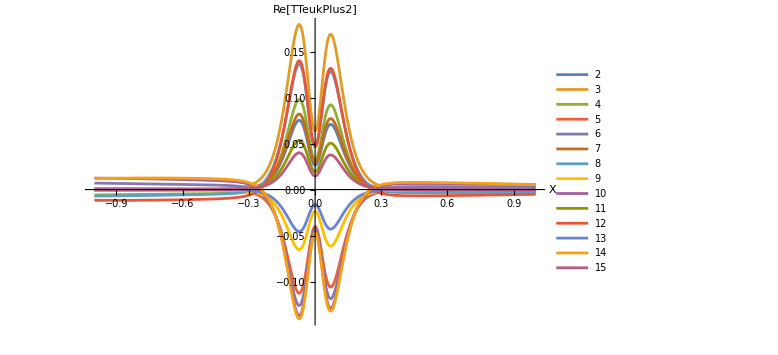

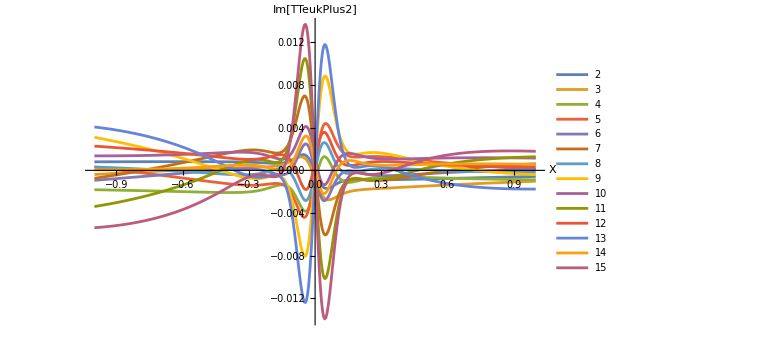

```mathematica
reCurvesPlus=Table[getJoinedProjData[resPlus,+2,ell]["ReData"],{ell,ellListPlus}];

imCurvesPlus=Table[getJoinedProjData[resPlus,+2,ell]["ImData"],{ell,ellListPlus}];

ListLinePlot[reCurvesPlus,PlotLegends->Placed[ellListPlus,Right],PlotRange->All,AxesLabel->{"X","Re[TTeukPlus2]"},ImageSize->Large]

ListLinePlot[imCurvesPlus,PlotLegends->Placed[ellListPlus,Right],PlotRange->All,AxesLabel->{"X","Im[TTeukPlus2]"},ImageSize->Large]
```

## C++ code Generator

```mathematica
ClearAll[componentIDs,patchIDs,yStorageIDs,magicBytes,teffFuncs,flattenComplexInterleaved,buildComponentMatrix,exportBinaryComponentFile,exportPatchBinaryFiles,exportTwoPatchModeBinaryFiles,flagBits,normalizeMetricSignature,buildFlags];

componentIDs=<|"ll"->0,"ln"->1,"lm"->2,"lmb"->3,"nn"->4,"nm"->5,"nmb"->6,"mm"->7,"mmb"->8|>;

patchIDs=<|"left"->0,"right"->1|>;

yStorageIDs=<|"Full"->0,"HalfWithEvenReflection"->1|>;

magicBytes=Join[ToCharacterCode["GHZSRC1"],{0}];

(*flag bit masks*)
flagBits=<|"NegativeMIsConjugate"->1,(*bit 0*)"MostlyPlusSignature"->2    (*bit 1*)|>;

normalizeMetricSignature[s_]:=Which[s==="MostlyMinus"||s==="-+++"||s==="minus","MostlyMinus",s==="MostlyPlus"||s==="+---"||s==="plus","MostlyPlus",True,$Failed];

buildFlags[negM_,metricSig_]:=Module[{flags=0,sig=normalizeMetricSignature[metricSig]},If[sig===$Failed,Return[$Failed]];
If[TrueQ[negM],flags=BitOr[flags,flagBits["NegativeMIsConjugate"]]];
If[sig==="MostlyPlus",flags=BitOr[flags,flagBits["MostlyPlusSignature"]]];
flags];

teffFuncs=<|"ll"->Teffll$MMode$XY$numeric,"ln"->Teffln$MMode$XY$numeric,"lm"->Tefflm$MMode$XY$numeric,"lmb"->Tefflmb$MMode$XY$numeric,"nn"->Teffnn$MMode$XY$numeric,"nm"->Teffnm$MMode$XY$numeric,"nmb"->Teffnmb$MMode$XY$numeric,"mm"->Teffmm$MMode$XY$numeric,"mmb"->Teffmmb$MMode$XY$numeric|>;

flattenComplexInterleaved[data_?MatrixQ]:=Flatten[({Re[#],Im[#]}&)/@Flatten[data]];

buildComponentMatrix[fun_,m_Integer?NonNegative,XGrid_List,YGrid_List]:=Table[fun[m][x,y],{x,XGrid},{y,YGrid}];

Options[exportBinaryComponentFile]={"YStorage"->"Full","NegativeMIsConjugate"->True,"MetricSignature"->"MostlyMinus"};

exportBinaryComponentFile[file_String,component_String,m_Integer?NonNegative,patch_String,XGrid_List,YGrid_List,data_?MatrixQ,rp_,B_,OptionsPattern[]]:=Module[{nx,ny,stream,flat,patchID,yStorageID,flags,metricSig},nx=Length[XGrid];
ny=Length[YGrid];
If[!KeyExistsQ[componentIDs,component],Return[$Failed]];
If[!KeyExistsQ[patchIDs,patch],Return[$Failed]];
If[!KeyExistsQ[yStorageIDs,OptionValue["YStorage"]],Return[$Failed]];
If[Dimensions[data]=!={nx,ny},Print["Dimension mismatch in exportBinaryComponentFile for ",file];
Return[$Failed];];
metricSig=normalizeMetricSignature[OptionValue["MetricSignature"]];
If[metricSig===$Failed,Print["Invalid MetricSignature option in exportBinaryComponentFile for ",file];
Return[$Failed];];
patchID=patchIDs[patch];
yStorageID=yStorageIDs[OptionValue["YStorage"]];
flags=buildFlags[OptionValue["NegativeMIsConjugate"],metricSig];
If[flags===$Failed,Return[$Failed]];
flat=N15[flattenComplexInterleaved[data]];
stream=OpenWrite[file,BinaryFormat->True];
BinaryWrite[stream,magicBytes,"Byte"];
BinaryWrite[stream,1,"UnsignedInteger32"];(*layout unchanged*)BinaryWrite[stream,m,"Integer32"];
BinaryWrite[stream,componentIDs[component],"UnsignedInteger32"];
BinaryWrite[stream,patchID,"UnsignedInteger32"];
BinaryWrite[stream,yStorageID,"UnsignedInteger32"];
BinaryWrite[stream,flags,"UnsignedInteger32"];
BinaryWrite[stream,N15[rp],"Real64"];
BinaryWrite[stream,N15[B],"Real64"];
BinaryWrite[stream,nx,"UnsignedInteger64"];
BinaryWrite[stream,ny,"UnsignedInteger64"];
BinaryWrite[stream,N15[XGrid],"Real64"];
BinaryWrite[stream,N15[YGrid],"Real64"];
BinaryWrite[stream,flat,"Real64"];
Close[stream];
file];

Options[exportPatchBinaryFiles]={"Prefix"->"Teff","YStorage"->"Full","NegativeMIsConjugate"->True,"MetricSignature"->"MostlyMinus","Verbose"->False};

exportPatchBinaryFiles[dir_String,m_Integer?NonNegative,patch_String,XGrid_List,YGrid_List,rp_,B_,OptionsPattern[]]:=Module[{prefix,yStorage,negm,metricSig,verbose,data,file},prefix=OptionValue["Prefix"];
yStorage=OptionValue["YStorage"];
negm=OptionValue["NegativeMIsConjugate"];
metricSig=OptionValue["MetricSignature"];
verbose=TrueQ[OptionValue["Verbose"]];
If[!MemberQ[{"left","right"},patch],Return[$Failed]];
CreateDirectory[dir,CreateIntermediateDirectories->True];
KeyValueMap[(If[verbose,Print["Writing ",#1,"  m=",m,"  patch=",patch,"  signature=",metricSig]];
data=buildComponentMatrix[#2,m,XGrid,YGrid];
file=FileNameJoin[{dir,StringTemplate["``_``_m``_``.bin"][prefix,#1,m,patch]}];
exportBinaryComponentFile[file,#1,m,patch,XGrid,YGrid,data,rp,B,"YStorage"->yStorage,"NegativeMIsConjugate"->negm,"MetricSignature"->metricSig])&,teffFuncs]];

Options[exportTwoPatchModeBinaryFiles]=Options[exportPatchBinaryFiles];

exportTwoPatchModeBinaryFiles[dir_String,m_Integer?NonNegative,XLeftGrid_List,XRightGrid_List,YGrid_List,rp_,B_,OptionsPattern[]]:=Module[{prefix,yStorage,negm,metricSig,verbose},prefix=OptionValue["Prefix"];
yStorage=OptionValue["YStorage"];
negm=OptionValue["NegativeMIsConjugate"];
metricSig=OptionValue["MetricSignature"];
verbose=TrueQ[OptionValue["Verbose"]];
If[verbose,Print["=== Exporting mode m = ",m,"  signature=",metricSig," ==="]];
exportPatchBinaryFiles[dir,m,"left",XLeftGrid,YGrid,rp,B,"Prefix"->prefix,"YStorage"->yStorage,"NegativeMIsConjugate"->negm,"MetricSignature"->metricSig,"Verbose"->verbose];
exportPatchBinaryFiles[dir,m,"right",XRightGrid,YGrid,rp,B,"Prefix"->prefix,"YStorage"->yStorage,"NegativeMIsConjugate"->negm,"MetricSignature"->metricSig,"Verbose"->verbose];];
```

```mathematica
(* usage exportTwoPatchModeBinaryFiles[dir,m,XLeftGrid,XRightGrid,YGrid,rp,B,"MetricSignature"->"MostlyPlus","Verbose"->True] *)
```

```mathematica
XLeftGrid={-2.,-1.};
XRightGrid={1.,2.};
YHalfGrid={0.,1.,2.};

Do[exportTwoPatchModeBinaryFiles["TeffBinary",m,XLeftGrid,XRightGrid,YHalfGrid,r0val,ℬ,"Prefix"->"Teff","YStorage"->"HalfWithEvenReflection","NegativeMIsConjugate"->True,"MetricSignature"->"MostlyPlus","Verbose"->True],{m,0,30}];
```

=== Exporting mode m = 0  signature=MostlyPlus ===

CreateDirectory::eexist: /Users/antares/TeffBinary already exists.

Writing ll  m=0  patch=left  signature=MostlyPlus

BinaryWrite::nocoerce: Re[Teffll$MMode$XY$numeric[0][-2.,0.]] cannot be coerced to the specified format.

Writing ln  m=0  patch=left  signature=MostlyPlus

BinaryWrite::nocoerce: Re[Teffln$MMode$XY$numeric[0][-2.,0.]] cannot be coerced to the specified format.

Writing lm  m=0  patch=left  signature=MostlyPlus

BinaryWrite::nocoerce: Re[Tefflm$MMode$XY$numeric[0][-2.,0.]] cannot be coerced to the specified format.

General::stop: Further output of BinaryWrite::nocoerce will be suppressed during this calculation.

Writing lmb  m=0  patch=left  signature=MostlyPlus

Writing nn  m=0  patch=left  signature=MostlyPlus

Writing nm  m=0  patch=left  signature=MostlyPlus

Writing nmb  m=0  patch=left  signature=MostlyPlus

Writing mm  m=0  patch=left  signature=MostlyPlus

Writing mmb  m=0  patch=left  signature=MostlyPlus

CreateDirectory::eexist: /Users/antares/TeffBinary already exists.

Writing ll  m=0  patch=right  signature=MostlyPlus

Writing ln  m=0  patch=right  signature=MostlyPlus

Writing lm  m=0  patch=right  signature=MostlyPlus

Writing lmb  m=0  patch=right  signature=MostlyPlus

Writing nn  m=0  patch=right  signature=MostlyPlus

Writing nm  m=0  patch=right  signature=MostlyPlus

Writing nmb  m=0  patch=right  signature=MostlyPlus

Writing mm  m=0  patch=right  signature=MostlyPlus

Writing mmb  m=0  patch=right  signature=MostlyPlus

=== Exporting mode m = 1  signature=MostlyPlus ===

CreateDirectory::eexist: /Users/antares/TeffBinary already exists.

General::stop: Further output of CreateDirectory::eexist will be suppressed during this calculation.

Writing ll  m=1  patch=left  signature=MostlyPlus

Writing ln  m=1  patch=left  signature=MostlyPlus

Writing lm  m=1  patch=left  signature=MostlyPlus

Writing lmb  m=1  patch=left  signature=MostlyPlus

Writing nn  m=1  patch=left  signature=MostlyPlus

Writing nm  m=1  patch=left  signature=MostlyPlus

Writing nmb  m=1  patch=left  signature=MostlyPlus

Writing mm  m=1  patch=left  signature=MostlyPlus

Writing mmb  m=1  patch=left  signature=MostlyPlus

Writing ll  m=1  patch=right  signature=MostlyPlus

Writing ln  m=1  patch=right  signature=MostlyPlus

Writing lm  m=1  patch=right  signature=MostlyPlus

Writing lmb  m=1  patch=right  signature=MostlyPlus

Writing nn  m=1  patch=right  signature=MostlyPlus

Writing nm  m=1  patch=right  signature=MostlyPlus

Writing nmb  m=1  patch=right  signature=MostlyPlus

Writing mm  m=1  patch=right  signature=MostlyPlus

Writing mmb  m=1  patch=right  signature=MostlyPlus

=== Exporting mode m = 2  signature=MostlyPlus ===

Writing ll  m=2  patch=left  signature=MostlyPlus

Writing ln  m=2  patch=left  signature=MostlyPlus

Writing lm  m=2  patch=left  signature=MostlyPlus

Writing lmb  m=2  patch=left  signature=MostlyPlus

Writing nn  m=2  patch=left  signature=MostlyPlus

Writing nm  m=2  patch=left  signature=MostlyPlus

Writing nmb  m=2  patch=left  signature=MostlyPlus

Writing mm  m=2  patch=left  signature=MostlyPlus

Writing mmb  m=2  patch=left  signature=MostlyPlus

Writing ll  m=2  patch=right  signature=MostlyPlus

Writing ln  m=2  patch=right  signature=MostlyPlus

Writing lm  m=2  patch=right  signature=MostlyPlus

Writing lmb  m=2  patch=right  signature=MostlyPlus

Writing nn  m=2  patch=right  signature=MostlyPlus

Writing nm  m=2  patch=right  signature=MostlyPlus

Writing nmb  m=2  patch=right  signature=MostlyPlus

Writing mm  m=2  patch=right  signature=MostlyPlus

Writing mmb  m=2  patch=right  signature=MostlyPlus

=== Exporting mode m = 3  signature=MostlyPlus ===

Writing ll  m=3  patch=left  signature=MostlyPlus

Writing ln  m=3  patch=left  signature=MostlyPlus

Writing lm  m=3  patch=left  signature=MostlyPlus

Writing lmb  m=3  patch=left  signature=MostlyPlus

Writing nn  m=3  patch=left  signature=MostlyPlus

Writing nm  m=3  patch=left  signature=MostlyPlus

Writing nmb  m=3  patch=left  signature=MostlyPlus

Writing mm  m=3  patch=left  signature=MostlyPlus

Writing mmb  m=3  patch=left  signature=MostlyPlus

Writing ll  m=3  patch=right  signature=MostlyPlus

Writing ln  m=3  patch=right  signature=MostlyPlus

Writing lm  m=3  patch=right  signature=MostlyPlus

Writing lmb  m=3  patch=right  signature=MostlyPlus

Writing nn  m=3  patch=right  signature=MostlyPlus

Writing nm  m=3  patch=right  signature=MostlyPlus

Writing nmb  m=3  patch=right  signature=MostlyPlus

Writing mm  m=3  patch=right  signature=MostlyPlus

Writing mmb  m=3  patch=right  signature=MostlyPlus

=== Exporting mode m = 4  signature=MostlyPlus ===

Writing ll  m=4  patch=left  signature=MostlyPlus

Writing ln  m=4  patch=left  signature=MostlyPlus

Writing lm  m=4  patch=left  signature=MostlyPlus

Writing lmb  m=4  patch=left  signature=MostlyPlus

Writing nn  m=4  patch=left  signature=MostlyPlus

Writing nm  m=4  patch=left  signature=MostlyPlus

Writing nmb  m=4  patch=left  signature=MostlyPlus

Writing mm  m=4  patch=left  signature=MostlyPlus

Writing mmb  m=4  patch=left  signature=MostlyPlus

Writing ll  m=4  patch=right  signature=MostlyPlus

Writing ln  m=4  patch=right  signature=MostlyPlus

Writing lm  m=4  patch=right  signature=MostlyPlus

Writing lmb  m=4  patch=right  signature=MostlyPlus

Writing nn  m=4  patch=right  signature=MostlyPlus

Writing nm  m=4  patch=right  signature=MostlyPlus

Writing nmb  m=4  patch=right  signature=MostlyPlus

Writing mm  m=4  patch=right  signature=MostlyPlus

Writing mmb  m=4  patch=right  signature=MostlyPlus

=== Exporting mode m = 5  signature=MostlyPlus ===

Writing ll  m=5  patch=left  signature=MostlyPlus

Writing ln  m=5  patch=left  signature=MostlyPlus

Writing lm  m=5  patch=left  signature=MostlyPlus

Writing lmb  m=5  patch=left  signature=MostlyPlus

Writing nn  m=5  patch=left  signature=MostlyPlus

Writing nm  m=5  patch=left  signature=MostlyPlus

Writing nmb  m=5  patch=left  signature=MostlyPlus

Writing mm  m=5  patch=left  signature=MostlyPlus

Writing mmb  m=5  patch=left  signature=MostlyPlus

Writing ll  m=5  patch=right  signature=MostlyPlus

Writing ln  m=5  patch=right  signature=MostlyPlus

Writing lm  m=5  patch=right  signature=MostlyPlus

Writing lmb  m=5  patch=right  signature=MostlyPlus

Writing nn  m=5  patch=right  signature=MostlyPlus

Writing nm  m=5  patch=right  signature=MostlyPlus

Writing nmb  m=5  patch=right  signature=MostlyPlus

Writing mm  m=5  patch=right  signature=MostlyPlus

Writing mmb  m=5  patch=right  signature=MostlyPlus

=== Exporting mode m = 6  signature=MostlyPlus ===

Writing ll  m=6  patch=left  signature=MostlyPlus

Writing ln  m=6  patch=left  signature=MostlyPlus

Writing lm  m=6  patch=left  signature=MostlyPlus

Writing lmb  m=6  patch=left  signature=MostlyPlus

Writing nn  m=6  patch=left  signature=MostlyPlus

Writing nm  m=6  patch=left  signature=MostlyPlus

Writing nmb  m=6  patch=left  signature=MostlyPlus

Writing mm  m=6  patch=left  signature=MostlyPlus

Writing mmb  m=6  patch=left  signature=MostlyPlus

Writing ll  m=6  patch=right  signature=MostlyPlus

Writing ln  m=6  patch=right  signature=MostlyPlus

Writing lm  m=6  patch=right  signature=MostlyPlus

Writing lmb  m=6  patch=right  signature=MostlyPlus

Writing nn  m=6  patch=right  signature=MostlyPlus

Writing nm  m=6  patch=right  signature=MostlyPlus

Writing nmb  m=6  patch=right  signature=MostlyPlus

Writing mm  m=6  patch=right  signature=MostlyPlus

Writing mmb  m=6  patch=right  signature=MostlyPlus

=== Exporting mode m = 7  signature=MostlyPlus ===

Writing ll  m=7  patch=left  signature=MostlyPlus

Writing ln  m=7  patch=left  signature=MostlyPlus

Writing lm  m=7  patch=left  signature=MostlyPlus

Writing lmb  m=7  patch=left  signature=MostlyPlus

Writing nn  m=7  patch=left  signature=MostlyPlus

Writing nm  m=7  patch=left  signature=MostlyPlus

Writing nmb  m=7  patch=left  signature=MostlyPlus

Writing mm  m=7  patch=left  signature=MostlyPlus

Writing mmb  m=7  patch=left  signature=MostlyPlus

Writing ll  m=7  patch=right  signature=MostlyPlus

Writing ln  m=7  patch=right  signature=MostlyPlus

Writing lm  m=7  patch=right  signature=MostlyPlus

Writing lmb  m=7  patch=right  signature=MostlyPlus

Writing nn  m=7  patch=right  signature=MostlyPlus

Writing nm  m=7  patch=right  signature=MostlyPlus

Writing nmb  m=7  patch=right  signature=MostlyPlus

Writing mm  m=7  patch=right  signature=MostlyPlus

Writing mmb  m=7  patch=right  signature=MostlyPlus

=== Exporting mode m = 8  signature=MostlyPlus ===

Writing ll  m=8  patch=left  signature=MostlyPlus

Writing ln  m=8  patch=left  signature=MostlyPlus

Writing lm  m=8  patch=left  signature=MostlyPlus

Writing lmb  m=8  patch=left  signature=MostlyPlus

Writing nn  m=8  patch=left  signature=MostlyPlus

Writing nm  m=8  patch=left  signature=MostlyPlus

Writing nmb  m=8  patch=left  signature=MostlyPlus

Writing mm  m=8  patch=left  signature=MostlyPlus

Writing mmb  m=8  patch=left  signature=MostlyPlus

Writing ll  m=8  patch=right  signature=MostlyPlus

Writing ln  m=8  patch=right  signature=MostlyPlus

Writing lm  m=8  patch=right  signature=MostlyPlus

Writing lmb  m=8  patch=right  signature=MostlyPlus

Writing nn  m=8  patch=right  signature=MostlyPlus

Writing nm  m=8  patch=right  signature=MostlyPlus

Writing nmb  m=8  patch=right  signature=MostlyPlus

Writing mm  m=8  patch=right  signature=MostlyPlus

Writing mmb  m=8  patch=right  signature=MostlyPlus

=== Exporting mode m = 9  signature=MostlyPlus ===

Writing ll  m=9  patch=left  signature=MostlyPlus

Writing ln  m=9  patch=left  signature=MostlyPlus

Writing lm  m=9  patch=left  signature=MostlyPlus

Writing lmb  m=9  patch=left  signature=MostlyPlus

Writing nn  m=9  patch=left  signature=MostlyPlus

Writing nm  m=9  patch=left  signature=MostlyPlus

Writing nmb  m=9  patch=left  signature=MostlyPlus

Writing mm  m=9  patch=left  signature=MostlyPlus

Writing mmb  m=9  patch=left  signature=MostlyPlus

Writing ll  m=9  patch=right  signature=MostlyPlus

Writing ln  m=9  patch=right  signature=MostlyPlus

Writing lm  m=9  patch=right  signature=MostlyPlus

Writing lmb  m=9  patch=right  signature=MostlyPlus

Writing nn  m=9  patch=right  signature=MostlyPlus

Writing nm  m=9  patch=right  signature=MostlyPlus

Writing nmb  m=9  patch=right  signature=MostlyPlus

Writing mm  m=9  patch=right  signature=MostlyPlus

Writing mmb  m=9  patch=right  signature=MostlyPlus

=== Exporting mode m = 10  signature=MostlyPlus ===

Writing ll  m=10  patch=left  signature=MostlyPlus

Writing ln  m=10  patch=left  signature=MostlyPlus

Writing lm  m=10  patch=left  signature=MostlyPlus

Writing lmb  m=10  patch=left  signature=MostlyPlus

Writing nn  m=10  patch=left  signature=MostlyPlus

Writing nm  m=10  patch=left  signature=MostlyPlus

Writing nmb  m=10  patch=left  signature=MostlyPlus

Writing mm  m=10  patch=left  signature=MostlyPlus

Writing mmb  m=10  patch=left  signature=MostlyPlus

Writing ll  m=10  patch=right  signature=MostlyPlus

Writing ln  m=10  patch=right  signature=MostlyPlus

Writing lm  m=10  patch=right  signature=MostlyPlus

Writing lmb  m=10  patch=right  signature=MostlyPlus

Writing nn  m=10  patch=right  signature=MostlyPlus

Writing nm  m=10  patch=right  signature=MostlyPlus

Writing nmb  m=10  patch=right  signature=MostlyPlus

Writing mm  m=10  patch=right  signature=MostlyPlus

Writing mmb  m=10  patch=right  signature=MostlyPlus

=== Exporting mode m = 11  signature=MostlyPlus ===

Writing ll  m=11  patch=left  signature=MostlyPlus

Writing ln  m=11  patch=left  signature=MostlyPlus

Writing lm  m=11  patch=left  signature=MostlyPlus

Writing lmb  m=11  patch=left  signature=MostlyPlus

Writing nn  m=11  patch=left  signature=MostlyPlus

Writing nm  m=11  patch=left  signature=MostlyPlus

Writing nmb  m=11  patch=left  signature=MostlyPlus

Writing mm  m=11  patch=left  signature=MostlyPlus

Writing mmb  m=11  patch=left  signature=MostlyPlus

Writing ll  m=11  patch=right  signature=MostlyPlus

Writing ln  m=11  patch=right  signature=MostlyPlus

Writing lm  m=11  patch=right  signature=MostlyPlus

Writing lmb  m=11  patch=right  signature=MostlyPlus

Writing nn  m=11  patch=right  signature=MostlyPlus

Writing nm  m=11  patch=right  signature=MostlyPlus

Writing nmb  m=11  patch=right  signature=MostlyPlus

Writing mm  m=11  patch=right  signature=MostlyPlus

Writing mmb  m=11  patch=right  signature=MostlyPlus

=== Exporting mode m = 12  signature=MostlyPlus ===

Writing ll  m=12  patch=left  signature=MostlyPlus

Writing ln  m=12  patch=left  signature=MostlyPlus

Writing lm  m=12  patch=left  signature=MostlyPlus

Writing lmb  m=12  patch=left  signature=MostlyPlus

Writing nn  m=12  patch=left  signature=MostlyPlus

Writing nm  m=12  patch=left  signature=MostlyPlus

Writing nmb  m=12  patch=left  signature=MostlyPlus

Writing mm  m=12  patch=left  signature=MostlyPlus

Writing mmb  m=12  patch=left  signature=MostlyPlus

Writing ll  m=12  patch=right  signature=MostlyPlus

Writing ln  m=12  patch=right  signature=MostlyPlus

Writing lm  m=12  patch=right  signature=MostlyPlus

Writing lmb  m=12  patch=right  signature=MostlyPlus

Writing nn  m=12  patch=right  signature=MostlyPlus

Writing nm  m=12  patch=right  signature=MostlyPlus

Writing nmb  m=12  patch=right  signature=MostlyPlus

Writing mm  m=12  patch=right  signature=MostlyPlus

Writing mmb  m=12  patch=right  signature=MostlyPlus

=== Exporting mode m = 13  signature=MostlyPlus ===

Writing ll  m=13  patch=left  signature=MostlyPlus

Writing ln  m=13  patch=left  signature=MostlyPlus

Writing lm  m=13  patch=left  signature=MostlyPlus

Writing lmb  m=13  patch=left  signature=MostlyPlus

Writing nn  m=13  patch=left  signature=MostlyPlus

Writing nm  m=13  patch=left  signature=MostlyPlus

Writing nmb  m=13  patch=left  signature=MostlyPlus

Writing mm  m=13  patch=left  signature=MostlyPlus

Writing mmb  m=13  patch=left  signature=MostlyPlus

Writing ll  m=13  patch=right  signature=MostlyPlus

Writing ln  m=13  patch=right  signature=MostlyPlus

Writing lm  m=13  patch=right  signature=MostlyPlus

Writing lmb  m=13  patch=right  signature=MostlyPlus

Writing nn  m=13  patch=right  signature=MostlyPlus

Writing nm  m=13  patch=right  signature=MostlyPlus

Writing nmb  m=13  patch=right  signature=MostlyPlus

Writing mm  m=13  patch=right  signature=MostlyPlus

Writing mmb  m=13  patch=right  signature=MostlyPlus

=== Exporting mode m = 14  signature=MostlyPlus ===

Writing ll  m=14  patch=left  signature=MostlyPlus

Writing ln  m=14  patch=left  signature=MostlyPlus

Writing lm  m=14  patch=left  signature=MostlyPlus

Writing lmb  m=14  patch=left  signature=MostlyPlus

Writing nn  m=14  patch=left  signature=MostlyPlus

Writing nm  m=14  patch=left  signature=MostlyPlus

Writing nmb  m=14  patch=left  signature=MostlyPlus

Writing mm  m=14  patch=left  signature=MostlyPlus

Writing mmb  m=14  patch=left  signature=MostlyPlus

Writing ll  m=14  patch=right  signature=MostlyPlus

Writing ln  m=14  patch=right  signature=MostlyPlus

Writing lm  m=14  patch=right  signature=MostlyPlus

Writing lmb  m=14  patch=right  signature=MostlyPlus

Writing nn  m=14  patch=right  signature=MostlyPlus

Writing nm  m=14  patch=right  signature=MostlyPlus

Writing nmb  m=14  patch=right  signature=MostlyPlus

Writing mm  m=14  patch=right  signature=MostlyPlus

Writing mmb  m=14  patch=right  signature=MostlyPlus

=== Exporting mode m = 15  signature=MostlyPlus ===

Writing ll  m=15  patch=left  signature=MostlyPlus

Writing ln  m=15  patch=left  signature=MostlyPlus

Writing lm  m=15  patch=left  signature=MostlyPlus

Writing lmb  m=15  patch=left  signature=MostlyPlus

Writing nn  m=15  patch=left  signature=MostlyPlus

Writing nm  m=15  patch=left  signature=MostlyPlus

Writing nmb  m=15  patch=left  signature=MostlyPlus

Writing mm  m=15  patch=left  signature=MostlyPlus

Writing mmb  m=15  patch=left  signature=MostlyPlus

Writing ll  m=15  patch=right  signature=MostlyPlus

Writing ln  m=15  patch=right  signature=MostlyPlus

Writing lm  m=15  patch=right  signature=MostlyPlus

Writing lmb  m=15  patch=right  signature=MostlyPlus

Writing nn  m=15  patch=right  signature=MostlyPlus

Writing nm  m=15  patch=right  signature=MostlyPlus

Writing nmb  m=15  patch=right  signature=MostlyPlus

Writing mm  m=15  patch=right  signature=MostlyPlus

Writing mmb  m=15  patch=right  signature=MostlyPlus

=== Exporting mode m = 16  signature=MostlyPlus ===

Writing ll  m=16  patch=left  signature=MostlyPlus

Writing ln  m=16  patch=left  signature=MostlyPlus

Writing lm  m=16  patch=left  signature=MostlyPlus

Writing lmb  m=16  patch=left  signature=MostlyPlus

Writing nn  m=16  patch=left  signature=MostlyPlus

Writing nm  m=16  patch=left  signature=MostlyPlus

Writing nmb  m=16  patch=left  signature=MostlyPlus

Writing mm  m=16  patch=left  signature=MostlyPlus

Writing mmb  m=16  patch=left  signature=MostlyPlus

Writing ll  m=16  patch=right  signature=MostlyPlus

Writing ln  m=16  patch=right  signature=MostlyPlus

Writing lm  m=16  patch=right  signature=MostlyPlus

Writing lmb  m=16  patch=right  signature=MostlyPlus

Writing nn  m=16  patch=right  signature=MostlyPlus

Writing nm  m=16  patch=right  signature=MostlyPlus

Writing nmb  m=16  patch=right  signature=MostlyPlus

Writing mm  m=16  patch=right  signature=MostlyPlus

Writing mmb  m=16  patch=right  signature=MostlyPlus

=== Exporting mode m = 17  signature=MostlyPlus ===

Writing ll  m=17  patch=left  signature=MostlyPlus

Writing ln  m=17  patch=left  signature=MostlyPlus

Writing lm  m=17  patch=left  signature=MostlyPlus

Writing lmb  m=17  patch=left  signature=MostlyPlus

Writing nn  m=17  patch=left  signature=MostlyPlus

Writing nm  m=17  patch=left  signature=MostlyPlus

Writing nmb  m=17  patch=left  signature=MostlyPlus

Writing mm  m=17  patch=left  signature=MostlyPlus

Writing mmb  m=17  patch=left  signature=MostlyPlus

Writing ll  m=17  patch=right  signature=MostlyPlus

Writing ln  m=17  patch=right  signature=MostlyPlus

Writing lm  m=17  patch=right  signature=MostlyPlus

Writing lmb  m=17  patch=right  signature=MostlyPlus

Writing nn  m=17  patch=right  signature=MostlyPlus

Writing nm  m=17  patch=right  signature=MostlyPlus

Writing nmb  m=17  patch=right  signature=MostlyPlus

Writing mm  m=17  patch=right  signature=MostlyPlus

Writing mmb  m=17  patch=right  signature=MostlyPlus

=== Exporting mode m = 18  signature=MostlyPlus ===

Writing ll  m=18  patch=left  signature=MostlyPlus

Writing ln  m=18  patch=left  signature=MostlyPlus

Writing lm  m=18  patch=left  signature=MostlyPlus

Writing lmb  m=18  patch=left  signature=MostlyPlus

Writing nn  m=18  patch=left  signature=MostlyPlus

Writing nm  m=18  patch=left  signature=MostlyPlus

Writing nmb  m=18  patch=left  signature=MostlyPlus

Writing mm  m=18  patch=left  signature=MostlyPlus

Writing mmb  m=18  patch=left  signature=MostlyPlus

Writing ll  m=18  patch=right  signature=MostlyPlus

Writing ln  m=18  patch=right  signature=MostlyPlus

Writing lm  m=18  patch=right  signature=MostlyPlus

Writing lmb  m=18  patch=right  signature=MostlyPlus

Writing nn  m=18  patch=right  signature=MostlyPlus

Writing nm  m=18  patch=right  signature=MostlyPlus

Writing nmb  m=18  patch=right  signature=MostlyPlus

Writing mm  m=18  patch=right  signature=MostlyPlus

Writing mmb  m=18  patch=right  signature=MostlyPlus

=== Exporting mode m = 19  signature=MostlyPlus ===

Writing ll  m=19  patch=left  signature=MostlyPlus

Writing ln  m=19  patch=left  signature=MostlyPlus

Writing lm  m=19  patch=left  signature=MostlyPlus

Writing lmb  m=19  patch=left  signature=MostlyPlus

Writing nn  m=19  patch=left  signature=MostlyPlus

Writing nm  m=19  patch=left  signature=MostlyPlus

Writing nmb  m=19  patch=left  signature=MostlyPlus

Writing mm  m=19  patch=left  signature=MostlyPlus

Writing mmb  m=19  patch=left  signature=MostlyPlus

Writing ll  m=19  patch=right  signature=MostlyPlus

Writing ln  m=19  patch=right  signature=MostlyPlus

Writing lm  m=19  patch=right  signature=MostlyPlus

Writing lmb  m=19  patch=right  signature=MostlyPlus

Writing nn  m=19  patch=right  signature=MostlyPlus

Writing nm  m=19  patch=right  signature=MostlyPlus

Writing nmb  m=19  patch=right  signature=MostlyPlus

Writing mm  m=19  patch=right  signature=MostlyPlus

Writing mmb  m=19  patch=right  signature=MostlyPlus

=== Exporting mode m = 20  signature=MostlyPlus ===

Writing ll  m=20  patch=left  signature=MostlyPlus

Writing ln  m=20  patch=left  signature=MostlyPlus

Writing lm  m=20  patch=left  signature=MostlyPlus

Writing lmb  m=20  patch=left  signature=MostlyPlus

Writing nn  m=20  patch=left  signature=MostlyPlus

Writing nm  m=20  patch=left  signature=MostlyPlus

Writing nmb  m=20  patch=left  signature=MostlyPlus

Writing mm  m=20  patch=left  signature=MostlyPlus

Writing mmb  m=20  patch=left  signature=MostlyPlus

Writing ll  m=20  patch=right  signature=MostlyPlus

Writing ln  m=20  patch=right  signature=MostlyPlus

Writing lm  m=20  patch=right  signature=MostlyPlus

Writing lmb  m=20  patch=right  signature=MostlyPlus

Writing nn  m=20  patch=right  signature=MostlyPlus

Writing nm  m=20  patch=right  signature=MostlyPlus

Writing nmb  m=20  patch=right  signature=MostlyPlus

Writing mm  m=20  patch=right  signature=MostlyPlus

Writing mmb  m=20  patch=right  signature=MostlyPlus

=== Exporting mode m = 21  signature=MostlyPlus ===

Writing ll  m=21  patch=left  signature=MostlyPlus

Writing ln  m=21  patch=left  signature=MostlyPlus

Writing lm  m=21  patch=left  signature=MostlyPlus

Writing lmb  m=21  patch=left  signature=MostlyPlus

Writing nn  m=21  patch=left  signature=MostlyPlus

Writing nm  m=21  patch=left  signature=MostlyPlus

Writing nmb  m=21  patch=left  signature=MostlyPlus

Writing mm  m=21  patch=left  signature=MostlyPlus

Writing mmb  m=21  patch=left  signature=MostlyPlus

Writing ll  m=21  patch=right  signature=MostlyPlus

Writing ln  m=21  patch=right  signature=MostlyPlus

Writing lm  m=21  patch=right  signature=MostlyPlus

Writing lmb  m=21  patch=right  signature=MostlyPlus

Writing nn  m=21  patch=right  signature=MostlyPlus

Writing nm  m=21  patch=right  signature=MostlyPlus

Writing nmb  m=21  patch=right  signature=MostlyPlus

Writing mm  m=21  patch=right  signature=MostlyPlus

Writing mmb  m=21  patch=right  signature=MostlyPlus

=== Exporting mode m = 22  signature=MostlyPlus ===

Writing ll  m=22  patch=left  signature=MostlyPlus

Writing ln  m=22  patch=left  signature=MostlyPlus

Writing lm  m=22  patch=left  signature=MostlyPlus

Writing lmb  m=22  patch=left  signature=MostlyPlus

Writing nn  m=22  patch=left  signature=MostlyPlus

Writing nm  m=22  patch=left  signature=MostlyPlus

Writing nmb  m=22  patch=left  signature=MostlyPlus

Writing mm  m=22  patch=left  signature=MostlyPlus

Writing mmb  m=22  patch=left  signature=MostlyPlus

Writing ll  m=22  patch=right  signature=MostlyPlus

Writing ln  m=22  patch=right  signature=MostlyPlus

Writing lm  m=22  patch=right  signature=MostlyPlus

Writing lmb  m=22  patch=right  signature=MostlyPlus

Writing nn  m=22  patch=right  signature=MostlyPlus

Writing nm  m=22  patch=right  signature=MostlyPlus

Writing nmb  m=22  patch=right  signature=MostlyPlus

Writing mm  m=22  patch=right  signature=MostlyPlus

Writing mmb  m=22  patch=right  signature=MostlyPlus

=== Exporting mode m = 23  signature=MostlyPlus ===

Writing ll  m=23  patch=left  signature=MostlyPlus

Writing ln  m=23  patch=left  signature=MostlyPlus

Writing lm  m=23  patch=left  signature=MostlyPlus

Writing lmb  m=23  patch=left  signature=MostlyPlus

Writing nn  m=23  patch=left  signature=MostlyPlus

Writing nm  m=23  patch=left  signature=MostlyPlus

Writing nmb  m=23  patch=left  signature=MostlyPlus

Writing mm  m=23  patch=left  signature=MostlyPlus

Writing mmb  m=23  patch=left  signature=MostlyPlus

Writing ll  m=23  patch=right  signature=MostlyPlus

Writing ln  m=23  patch=right  signature=MostlyPlus

Writing lm  m=23  patch=right  signature=MostlyPlus

Writing lmb  m=23  patch=right  signature=MostlyPlus

Writing nn  m=23  patch=right  signature=MostlyPlus

Writing nm  m=23  patch=right  signature=MostlyPlus

Writing nmb  m=23  patch=right  signature=MostlyPlus

Writing mm  m=23  patch=right  signature=MostlyPlus

Writing mmb  m=23  patch=right  signature=MostlyPlus

=== Exporting mode m = 24  signature=MostlyPlus ===

Writing ll  m=24  patch=left  signature=MostlyPlus

Writing ln  m=24  patch=left  signature=MostlyPlus

Writing lm  m=24  patch=left  signature=MostlyPlus

Writing lmb  m=24  patch=left  signature=MostlyPlus

Writing nn  m=24  patch=left  signature=MostlyPlus

Writing nm  m=24  patch=left  signature=MostlyPlus

Writing nmb  m=24  patch=left  signature=MostlyPlus

Writing mm  m=24  patch=left  signature=MostlyPlus

Writing mmb  m=24  patch=left  signature=MostlyPlus

Writing ll  m=24  patch=right  signature=MostlyPlus

Writing ln  m=24  patch=right  signature=MostlyPlus

Writing lm  m=24  patch=right  signature=MostlyPlus

Writing lmb  m=24  patch=right  signature=MostlyPlus

Writing nn  m=24  patch=right  signature=MostlyPlus

Writing nm  m=24  patch=right  signature=MostlyPlus

Writing nmb  m=24  patch=right  signature=MostlyPlus

Writing mm  m=24  patch=right  signature=MostlyPlus

Writing mmb  m=24  patch=right  signature=MostlyPlus

=== Exporting mode m = 25  signature=MostlyPlus ===

Writing ll  m=25  patch=left  signature=MostlyPlus

Writing ln  m=25  patch=left  signature=MostlyPlus

Writing lm  m=25  patch=left  signature=MostlyPlus

Writing lmb  m=25  patch=left  signature=MostlyPlus

Writing nn  m=25  patch=left  signature=MostlyPlus

Writing nm  m=25  patch=left  signature=MostlyPlus

Writing nmb  m=25  patch=left  signature=MostlyPlus

Writing mm  m=25  patch=left  signature=MostlyPlus

Writing mmb  m=25  patch=left  signature=MostlyPlus

Writing ll  m=25  patch=right  signature=MostlyPlus

Writing ln  m=25  patch=right  signature=MostlyPlus

Writing lm  m=25  patch=right  signature=MostlyPlus

Writing lmb  m=25  patch=right  signature=MostlyPlus

Writing nn  m=25  patch=right  signature=MostlyPlus

Writing nm  m=25  patch=right  signature=MostlyPlus

Writing nmb  m=25  patch=right  signature=MostlyPlus

Writing mm  m=25  patch=right  signature=MostlyPlus

Writing mmb  m=25  patch=right  signature=MostlyPlus

=== Exporting mode m = 26  signature=MostlyPlus ===

Writing ll  m=26  patch=left  signature=MostlyPlus

Writing ln  m=26  patch=left  signature=MostlyPlus

Writing lm  m=26  patch=left  signature=MostlyPlus

Writing lmb  m=26  patch=left  signature=MostlyPlus

Writing nn  m=26  patch=left  signature=MostlyPlus

Writing nm  m=26  patch=left  signature=MostlyPlus

Writing nmb  m=26  patch=left  signature=MostlyPlus

Writing mm  m=26  patch=left  signature=MostlyPlus

Writing mmb  m=26  patch=left  signature=MostlyPlus

Writing ll  m=26  patch=right  signature=MostlyPlus

Writing ln  m=26  patch=right  signature=MostlyPlus

Writing lm  m=26  patch=right  signature=MostlyPlus

Writing lmb  m=26  patch=right  signature=MostlyPlus

Writing nn  m=26  patch=right  signature=MostlyPlus

Writing nm  m=26  patch=right  signature=MostlyPlus

Writing nmb  m=26  patch=right  signature=MostlyPlus

Writing mm  m=26  patch=right  signature=MostlyPlus

Writing mmb  m=26  patch=right  signature=MostlyPlus

=== Exporting mode m = 27  signature=MostlyPlus ===

Writing ll  m=27  patch=left  signature=MostlyPlus

Writing ln  m=27  patch=left  signature=MostlyPlus

Writing lm  m=27  patch=left  signature=MostlyPlus

Writing lmb  m=27  patch=left  signature=MostlyPlus

Writing nn  m=27  patch=left  signature=MostlyPlus

Writing nm  m=27  patch=left  signature=MostlyPlus

Writing nmb  m=27  patch=left  signature=MostlyPlus

Writing mm  m=27  patch=left  signature=MostlyPlus

Writing mmb  m=27  patch=left  signature=MostlyPlus

Writing ll  m=27  patch=right  signature=MostlyPlus

Writing ln  m=27  patch=right  signature=MostlyPlus

Writing lm  m=27  patch=right  signature=MostlyPlus

Writing lmb  m=27  patch=right  signature=MostlyPlus

Writing nn  m=27  patch=right  signature=MostlyPlus

Writing nm  m=27  patch=right  signature=MostlyPlus

Writing nmb  m=27  patch=right  signature=MostlyPlus

Writing mm  m=27  patch=right  signature=MostlyPlus

Writing mmb  m=27  patch=right  signature=MostlyPlus

=== Exporting mode m = 28  signature=MostlyPlus ===

Writing ll  m=28  patch=left  signature=MostlyPlus

Writing ln  m=28  patch=left  signature=MostlyPlus

Writing lm  m=28  patch=left  signature=MostlyPlus

Writing lmb  m=28  patch=left  signature=MostlyPlus

Writing nn  m=28  patch=left  signature=MostlyPlus

Writing nm  m=28  patch=left  signature=MostlyPlus

Writing nmb  m=28  patch=left  signature=MostlyPlus

Writing mm  m=28  patch=left  signature=MostlyPlus

Writing mmb  m=28  patch=left  signature=MostlyPlus

Writing ll  m=28  patch=right  signature=MostlyPlus

Writing ln  m=28  patch=right  signature=MostlyPlus

Writing lm  m=28  patch=right  signature=MostlyPlus

Writing lmb  m=28  patch=right  signature=MostlyPlus

Writing nn  m=28  patch=right  signature=MostlyPlus

Writing nm  m=28  patch=right  signature=MostlyPlus

Writing nmb  m=28  patch=right  signature=MostlyPlus

Writing mm  m=28  patch=right  signature=MostlyPlus

Writing mmb  m=28  patch=right  signature=MostlyPlus

=== Exporting mode m = 29  signature=MostlyPlus ===

Writing ll  m=29  patch=left  signature=MostlyPlus

Writing ln  m=29  patch=left  signature=MostlyPlus

Writing lm  m=29  patch=left  signature=MostlyPlus

Writing lmb  m=29  patch=left  signature=MostlyPlus

Writing nn  m=29  patch=left  signature=MostlyPlus

Writing nm  m=29  patch=left  signature=MostlyPlus

Writing nmb  m=29  patch=left  signature=MostlyPlus

Writing mm  m=29  patch=left  signature=MostlyPlus

Writing mmb  m=29  patch=left  signature=MostlyPlus

Writing ll  m=29  patch=right  signature=MostlyPlus

Writing ln  m=29  patch=right  signature=MostlyPlus

Writing lm  m=29  patch=right  signature=MostlyPlus

Writing lmb  m=29  patch=right  signature=MostlyPlus

Writing nn  m=29  patch=right  signature=MostlyPlus

Writing nm  m=29  patch=right  signature=MostlyPlus

Writing nmb  m=29  patch=right  signature=MostlyPlus

Writing mm  m=29  patch=right  signature=MostlyPlus

Writing mmb  m=29  patch=right  signature=MostlyPlus

=== Exporting mode m = 30  signature=MostlyPlus ===

Writing ll  m=30  patch=left  signature=MostlyPlus

Writing ln  m=30  patch=left  signature=MostlyPlus

Writing lm  m=30  patch=left  signature=MostlyPlus

Writing lmb  m=30  patch=left  signature=MostlyPlus

Writing nn  m=30  patch=left  signature=MostlyPlus

Writing nm  m=30  patch=left  signature=MostlyPlus

Writing nmb  m=30  patch=left  signature=MostlyPlus

Writing mm  m=30  patch=left  signature=MostlyPlus

Writing mmb  m=30  patch=left  signature=MostlyPlus

Writing ll  m=30  patch=right  signature=MostlyPlus

Writing ln  m=30  patch=right  signature=MostlyPlus

Writing lm  m=30  patch=right  signature=MostlyPlus

Writing lmb  m=30  patch=right  signature=MostlyPlus

Writing nn  m=30  patch=right  signature=MostlyPlus

Writing nm  m=30  patch=right  signature=MostlyPlus

Writing nmb  m=30  patch=right  signature=MostlyPlus

Writing mm  m=30  patch=right  signature=MostlyPlus

Writing mmb  m=30  patch=right  signature=MostlyPlus

```mathematica
teffSourceSymbols={Teffll$MMode$XY$numeric,Teffln$MMode$XY$numeric,Tefflm$MMode$XY$numeric,Tefflmb$MMode$XY$numeric,Teffnn$MMode$XY$numeric,Teffnm$MMode$XY$numeric,Teffnmb$MMode$XY$numeric,Teffmm$MMode$XY$numeric,Teffmmb$MMode$XY$numeric};

generatorSymbols={componentIDs,patchIDs,yStorageIDs,magicBytes,teffFuncs,flattenComplexInterleaved,buildComponentMatrix,exportBinaryComponentFile,exportPatchBinaryFiles,exportTwoPatchModeBinaryFiles};Save["TeffSources.wl",teffSourceSymbols];
Save["TeffBinaryGenerator.wl",generatorSymbols];
```

```mathematica
DumpSave["TeffSources.mx",{Teffll$MMode$XY$numeric,Teffln$MMode$XY$numeric,Tefflm$MMode$XY$numeric,Tefflmb$MMode$XY$numeric,Teffnn$MMode$XY$numeric,Teffnm$MMode$XY$numeric,Teffnmb$MMode$XY$numeric,Teffmm$MMode$XY$numeric,Teffmmb$MMode$XY$numeric}]
```

{Teffll$MMode$XY$numeric,Teffln$MMode$XY$numeric,Tefflm$MMode$XY$numeric,Tefflmb$MMode$XY$numeric,Teffnn$MMode$XY$numeric,Teffnm$MMode$XY$numeric,Teffnmb$MMode$XY$numeric,Teffmm$MMode$XY$numeric,Teffmmb$MMode$XY$numeric}

```mathematica
Save["TeffBinaryGenerator.wl",{componentIDs,patchIDs,yStorageIDs,magicBytes,teffFuncs,flattenComplexInterleaved,buildComponentMatrix,exportBinaryComponentFile,exportPatchBinaryFiles,exportTwoPatchModeBinaryFiles}]
```

```mathematica
Save["TeffBinaryGeneratorWithSources.wl",{componentIDs,patchIDs,yStorageIDs,magicBytes,teffFuncs,flattenComplexInterleaved,buildComponentMatrix,exportBinaryComponentFile,exportPatchBinaryFiles,exportTwoPatchModeBinaryFiles,Teffll$MMode$XY$numeric,Teffln$MMode$XY$numeric,Tefflm$MMode$XY$numeric,Tefflmb$MMode$XY$numeric,Teffnn$MMode$XY$numeric,Teffnm$MMode$XY$numeric,Teffnmb$MMode$XY$numeric,Teffmm$MMode$XY$numeric,Teffmmb$MMode$XY$numeric}]
```